# 7-qubit Steane Code

Source of the experiment : www.nature.com/articles/s41586-022-04592-6

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"16"]*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink. Now it works as well directly using the default pre-compiled binary. But it usea only single core.

```mathematica
Import["~/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../../../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz
Length unit: μm

Accepts 2 or 3 dimensional coordinate format

## Device configuration

```mathematica
Options[RydbergHub]={
QubitNum-> 7,
AtomLocations-><|6->{0,1},5->{1,1},2->{2,1},1->{4,1},4->{2,0},0->{4,0},3->{5,0}|>,
T2->1.5*10^6,
VacLifeTime->48*10^6,
RabiFreq->1,
ProbBFRot-><|10->0.001, 01->0.03|>,
UnitLattice->3,
BlockadeRadius->1,
ProbLeakInit->0.001,
DurInit->5*10^5,
DurMove->100,
HeatFactor->10,
FidMeas-> 0.975,
DurMeas-> 10,
ProbLossMeas-> 0.0001,
ProbLeakCZ-><|01->0.01,11->0.0001|>
};
```

## Modules

```mathematica
(* 
List of stabilizers
*)
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];

(* 
returns indices of the involved stabilizers 
*)
stabindex[stab_]:=Level[stab,1]/.Subscript[_,j_]:>j 


(*
Run the simulation on steane code stabilizer measurements

expres = experimental results, {stabilizer_result, logical_result} 
*)
SimulateSteane[ρ_,ρinit_,ρwork_,ρstore_,nshots_,expres_,options_:{}]:=Module[{xmeascirc,zmeascirc,circ0,circ1,circ2,circ3,circ4,circ5,stabx,stabz,stabxid,stabzid,xlogic,zlogic,steanecirc,measz={},measx={},hposz,hposx,outeig,sxcount,szcount,meas,sign,zidx,sxideal,szideal,logiccount,logic,res},

(*hadamard positions in implementing measurements*)
hposz={0,3,4};
hposx={1,2,5,6};

circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]}};
meas=Subscript[M, #]&/@Range[0,6];
steanecirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
zmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposz,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
xmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposx,meas},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
(*x and z stabilizer *)
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
(* logical pauli-x and pauli-z *)
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];

stabxid=stabindex[#]&/@stabx;
stabzid=stabindex[#]&/@stabz;

CloneQureg[ρ,ρinit];
ApplyCircuit[ρ,steanecirc];
CloneQureg[ρstore,ρ];
Table[
(* Note that this is okay because we don't have any function that depends on the absolute time.*)
(* z measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measz,Flatten@ApplyCircuit[ρ,zmeascirc]];
(* x measurements*)
CloneQureg[ρ,ρstore];
AppendTo[measx,Flatten@ApplyCircuit[ρ,xmeascirc]];
,{nshots}];

logiccount=<|"x"->0,"z"->0|>;
(* Extract from z measurements *)
szcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposz,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
szcount[i]+=Times@@(outeig[[#+1]]&/@stabzid[[i+1]]);
,{i,Keys@szcount}];

logiccount["z"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measz}];

(* Extract from x measurements *)
sxcount=<|0->0,1->0,2->0|>;
Table[
outeig=Table[
If[MemberQ[hposx,k-1],
out[[k]]/.{0:>-1},(*flip*)
out[[k]]/.{1:>-1,0:>1}
],{k,Length@out}];

Table[
(* +1 - -1 *)
sxcount[i]+=Times@@(outeig[[#+1]]&/@stabxid[[i+1]]);
,{i,Keys@sxcount}];

logiccount["x"]+=Times@@(outeig[[#+1]]&/@{0,1,3})
,{out,measx}];

(* no-SPAM stabilizer measurement *)
circ0={Subscript[Ry, #][π/2]&/@Range[0,6]};
steanecirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[InitZeroState@ρ,steanecirc];
CloneQureg[ρstore,ρ];

xmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposx},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[ρ,xmeascirc];
sxideal=CalcExpecPauliString[ρ,#,ρwork]&/@stabx;

CloneQureg[ρ,ρstore];
zmeascirc=DeleteElements[ExtractCircuit[InsertCircuitNoise[{Subscript[Ry, #][π/2]&/@hposz},RydbergHub[Sequence@@options]]],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
ApplyCircuit[ρ,zmeascirc];
szideal=Table[
zidx=stabindex[s];
sign=If[EvenQ[Length[Intersection[hposz,zidx]]],+1,-1];
sign*CalcExpecPauliString[ρ,s,ρwork],{s,stabz}];
(* flip the logical Z because odd number of flip from Ry*)
logic=<|"x"->CalcExpecPauliString[ρ,xlogic,ρwork],"z"->-CalcExpecPauliString[ρ,zlogic,ρwork]|>;
res=<|"opt"->options,"outx"->measx,"outz"->measz,"sxcount"->sxcount,"szcount"->szcount,"sxideal"->sxideal,"szideal"->szideal,"logiccount"->logiccount,"logicideal"->logic,"options"->RydbergHub[Sequence@@options][OptionsUsed]|>;
res
]


(*
Plot the charts
*)
steaneCharts[res_,expstabs_,explogic_]:=With[
{
sxcount=res["sxcount"],
szcount=res["szcount"],
nshots=Length@res["outx"],
sxideal=res["sxideal"],
szideal=res["szideal"],
logiccount=res["logiccount"],
logicideal=res["logicideal"],
cols={RGBColor[0.3881893059227455, 0.5310037952810274, 0.49489914553171],RGBColor[0.93, 0.6, 0.15]},
size=200
},
Row@{
Show[
		BarChart[
Flatten@{Values@sxcount/nshots,Values@szcount/nshots},ChartLabels->(ToString[Subscript["S", #],TraditionalForm]&/@Range[0,5]),Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->2.5,ChartStyle->Flatten@{ConstantArray[cols[[1]],3],ConstantArray[cols[[2]],3]},
PlotRange->{Automatic,{-0.05,1}},Background->White,ImageSize->{Automatic,size},ImagePadding->{{30,0},{30,10}},BaseStyle->{16,FontFamily->"Serif"}],
ListPlot[{Join[sxideal,szideal],Join[sxideal,szideal]},Joined->True,PlotMarkers->{"■",15},PlotStyle->RGBColor[0.6913629326773305, 0.22460288235842985, 0.347286180798712]],
BarChart[Flatten@expstabs,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]]
],
Show[
BarChart[Values@logiccount/nshots,ChartLabels->{"X_L","Z_L"},Frame->True,FrameStyle->Directive[Black,Thick],AspectRatio->5,ChartStyle->cols,PlotRange->{{0.,3},{-0.05,1}},FrameTicks->{Automatic,Automatic},BaseStyle->{16,FontFamily->"Serif"}],
BarChart[explogic,ChartStyle->Directive[Opacity[0],EdgeForm[{Dashed,Thick}]]],
Background->White,ImageSize->{Automatic,size},ImagePadding->{{0,0},{30,10}}
]
}
]


(* 
sumarise the result
*)
steaneResults[res_,expstabs_,explogic_]:=With[{dev=RydbergHub[Sequence@@res[["opt"]]],nshots=res["outx"]//Length},
<|
"nshots"->nshots,
"charts"->steaneCharts[res,expstabs,explogic],
"avgstab"-><|"x"->N@Mean@Values@res["sxcount"]/nshots,"z"->N@Mean@Values@res["szcount"]/nshots,"xl"->N[res["logiccount"]["x"]/nshots],"zl"->N[res["logiccount"]["z"]/nshots]|>,
"errmaxstab"-><|"x"->N@Max@Abs[res["sxcount"]/nshots-First@expstabs],"z"->N@Max@Abs[res["szcount"]/nshots-Last@expstabs]|>,
"erravgstab"-><|"x"->N@Mean@Abs[Values@res["sxcount"]/nshots-First@expstabs],"z"->N@Mean@Abs[Values@res["szcount"]/nshots-Last@expstabs]|>,
"benchmarkstab"-><|"x"->Table[Between[res[["sxcount"]][j-1]/nshots,Sort[First[expstabs][[j]][[1]]+{1,-1}*First[expstabs][[j]][[2]]]],{j,Length@First@expstabs}],"z"->Table[Between[res[["szcount"]][j-1]/nshots,Sort[Last[expstabs][[j]][[1]]+{1,-1}*Last[expstabs][[j]][[2]]]],{j,Length@Last@expstabs}]|>,
"benchmarklogic"-><|"x"->Between[res[["logiccount"]]["x"]/nshots,Sort[explogic[[1]][[1]]+{1,-1}*explogic[[1]][[2]]]],
"z"->Between[res[["logiccount"]]["z"]/nshots,Sort[explogic[[2]][[1]]+{1,-1}*explogic[[2]][[2]]]]|>,
"errlogic"-><|"x"->Abs[res["logiccount"]["x"]/nshots-First@explogic],"z"->Abs[res["logiccount"]["z"]/nshots-Last@explogic]|>,
"idealavg"-><|"x"->Mean@res["sxideal"],"z"->Mean@res["szideal"],"xl"->res["logicideal"]["x"],"zl"->res["logicideal"]["z"]|>,
"chart"->steaneCharts[res,expstabs,explogic]
|>
]
```

## Plots and drawings

```mathematica
devst=RydbergHub[];
```

```mathematica
ClearAll[showst]
showst[title_:"",opt_:{}]:=PlotAtoms[devst,Sequence@@opt,ImageSize->600,ShowBlockade->Range[0,6],LabelStyle->Directive[Italic, 15,Black],BaseStyle->{17,FontFamily->"Serif"},PlotRange->{{-8,16},{-1.3,4.3}},Epilog->Inset[Style[title,{Purple,Italic}],Scaled[{0.2,0.1}]],Frame->True,FrameStyle->Directive[Black,Thick],Axes->False];
```

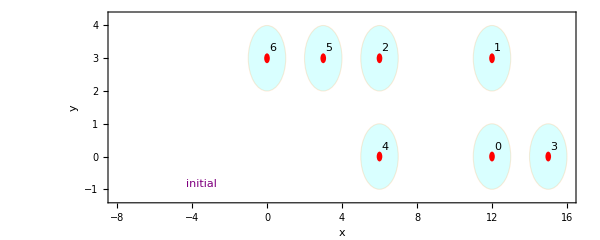

```mathematica
move0=showst["initial",{ImagePadding->{{20,18},{0,18}}}]
```

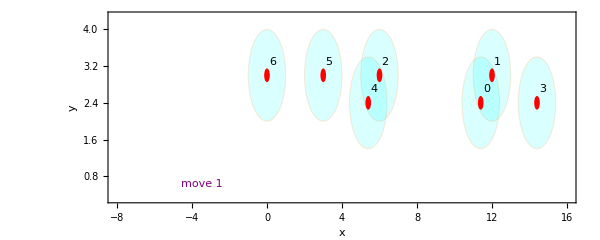

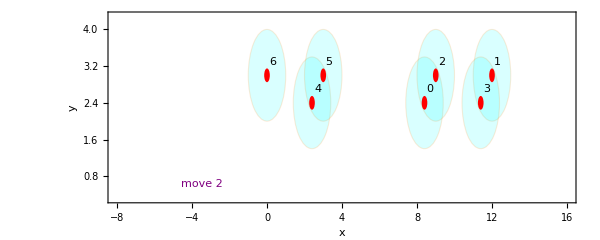

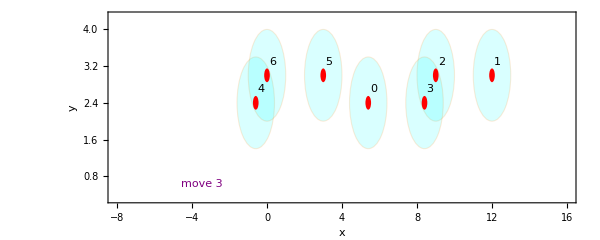

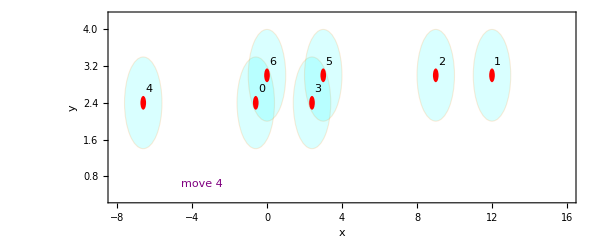

```mathematica
devst=RydbergHub[];
circ0={Subscript[Init, #]&/@Range[0,6],Subscript[Ry, #][π/2]&/@Range[0,6]};
circ1={{Subscript[ShiftLoc, 4,0,3][{-0.2,0.8}]},{Subscript[C, 2][Subscript[Z, 4]],Subscript[C, 0][Subscript[Z, 1]]}};
circ2={{Subscript[ShiftLoc, 2][{1,0}],Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 5]],Subscript[C, 2][Subscript[Z, 0]],Subscript[C, 1][Subscript[Z, 3]]}};
circ3={{Subscript[ShiftLoc, 4,0,3][{-1,0}]},{Subscript[C, 4][Subscript[Z, 6]],Subscript[C, 2][Subscript[Z, 3]]}};
circ4={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{0,3,4}};
circ5={{Subscript[ShiftLoc, 4,0,3][{-2,0}]},{Subscript[C, 0][Subscript[Z, 6]],Subscript[C, 3][Subscript[Z, 5]]},Subscript[Ry, #][π/2]&/@{1,2,5,6}};
InsertCircuitNoise[circ1,devst];
move1=showst["move 1",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ2,devst];
move2=showst["move 2",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ3,devst];
move3=showst["move 3",{ImagePadding->{{20,18},{0,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
InsertCircuitNoise[circ4,devst];
move4=showst["move 4",{ImagePadding->{{20,18},{18,0}},PlotRange->{{-8,16},{0.3,4.3}}}]
```

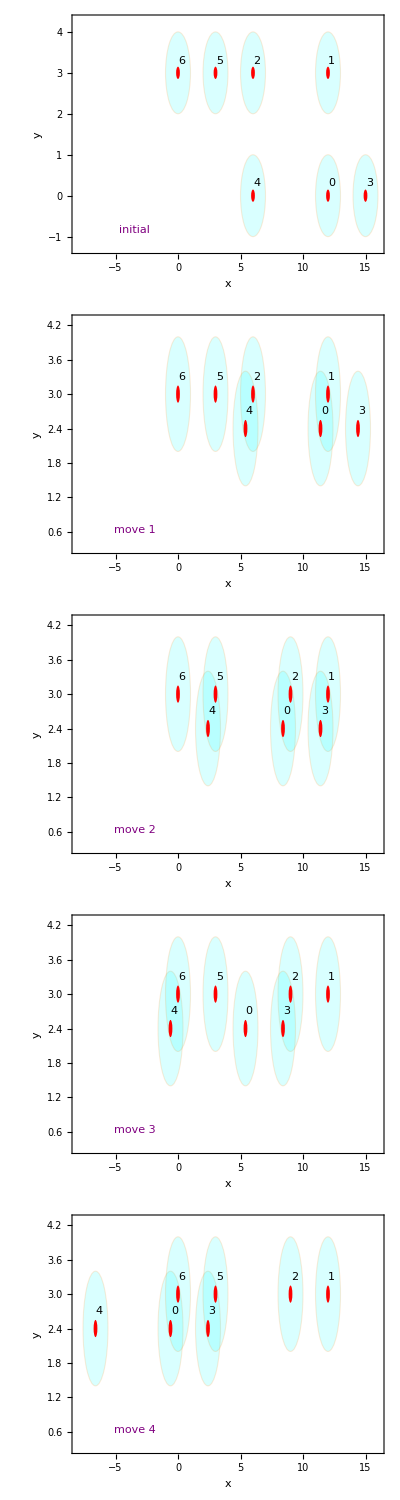

```mathematica
Column[{move0,move1,move2,move3,move4},Spacings->-0.1]
(*Export["/home/cica/vqd/img/rydberg_steane.pdf",%]*)
```

Entire simulation

```mathematica
stabx={Subscript[X, 0] Subscript[X, 1] Subscript[X, 2] Subscript[X, 6],Subscript[X, 2] Subscript[X, 4] Subscript[X, 5] Subscript[X, 6],Subscript[X, 1] Subscript[X, 2] Subscript[X, 3] Subscript[X, 5]};
stabz={Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 6],Subscript[Z, 2] Subscript[Z, 4] Subscript[Z, 5] Subscript[Z, 6],Subscript[Z, 1] Subscript[Z, 2] Subscript[Z, 3] Subscript[Z, 5]};
xlogic=Subscript[X, 0] Subscript[X, 1] Subscript[X, 3];
zlogic=Subscript[Z, 0] Subscript[Z, 1] Subscript[Z, 3];
(* returns indices of the involved stabilizers *)
stabindex[stab_]:=Level[stab,1]/.Subscript[_,j_]:>j
```

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork}=CreateDensityQuregs[7,3];
```

```mathematica
noisycirc=InsertCircuitNoise[Join[circ0,circ1,circ2,circ3,circ4],RydbergHub[]];
(*simplify, and remove zero-parameterised operations *)
simpncirc=DeleteElements[ExtractCircuit[noisycirc],{Subscript[Depol, __][0.],Subscript[Deph, __][0.],Subscript[Damp, __][0.]}];
```

Logical |+>

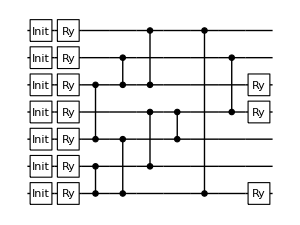

```mathematica
DrawCircuit@DeleteElements[Flatten@Join[circ0,circ1,circ2,circ3,circ4],{Subscript[ShiftLoc, __][_]}]
```

```mathematica
ApplyCircuit[SetQuregMatrix[ρ,IdentityMatrix[2^7]/2^7],simpncirc]
```

{}

```mathematica
(*list of some graph layouts*)
gl={"Automatic","CircularEmbedding","RandomEmbedding","SpiralEmbedding","GridEmbedding","SpringElectricalEmbedding","SpringEmbedding","HighDimensionalEmbedding","LayeredEmbedding","MultipartiteEmbedding","LayeredDigraphEmbedding","LayeredDrawing","RadialEmbedding","BipartiteEmbedding","BalloonEmbedding","TutteEmbedding","PlanarEmbedding","KamadaKawaiEmbedding","DavidsonHarelEmbedding"};
```

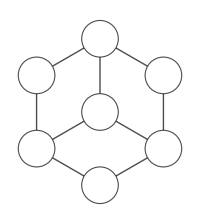

```mathematica
Graph[{2<->4,0<->1,4<->5,2<->0,1<->3,4<->6,2<->3,0<->6,3<->5},
VertexSize->0.5,VertexStyle->Directive[White,EdgeForm[Thick]],BaseStyle->{19,FontFamily->"Serif"},ImageSize->200,EdgeStyle->Directive[Black,Thick],VertexLabels->Placed[Automatic,Center],GraphLayout->"TutteEmbedding"]
(*Export["~/vqd/img/graphsteane.pdf",%]*)
```

## Experimental results to compare

-Graphics-

```mathematica
steanemean={0.5246212121212122,0.4924242424242424,0.5170454545454546,0.7329545454545454,0.7045454545454546,0.7462121212121211};
steaneminus={0.5,0.46780303030303033,0.4905303030303031,0.7121212121212122,0.6799242424242425,0.7234848484848485};
steaneplus={0.5454545454545455,0.5151515151515151,0.5378787878787878,0.7518939393939393,0.7234848484848485,0.7651515151515151};
```

```mathematica
lsteanemean={0.7134502923976608,-0.015594541910331362};
lsteaneminus={0.6939571150097467,-0.050682261208577};
lsteaneplus={0.7290448343079922,0.009746588693957212};
```

```mathematica
steane=Partition[Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{steanemean,steaneminus,steaneplus}],3]
lsteane=Around[#[[1]],#[[2;;]]-#[[1]]]&/@Transpose[{lsteanemean,lsteaneminus,lsteaneplus}]
```

{{0.5250.0250.021,0.4920.0250.023,0.5170.0270.021},{0.7330.0210.019,0.7050.0250.019,0.7460.0230.019}}

{0.7130.0190.016,-0.0160.0350.025}

```mathematica
(*stabsteane={{0.52,0.49,0.51},{0.732,0.7,0.75}};*)
logsteane={0.71,-0.02};
cols={RGBColor[0.3881893059227455, 0.5310037952810274, 0.49489914553171],RGBColor[0.93, 0.6, 0.15]};
```

## Run the simulation

### Prepare the state and memory

```mathematica
DestroyAllQuregs[]
{ρ,ρinit,ρwork,ρstore}=CreateDensityQuregs[7,4];
SetQuregMatrix[ρinit,RandomMixState[7]];
```

### Manual search to estimate the range of error parameters

```mathematica
Options@RydbergHub
```

{QubitNum→7,AtomLocations→<|6→{0,1},5→{1,1},2→{2,1},1→{4,1},4→{2,0},0→{4,0},3→{5,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.001,1→0.03|>,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.001,DurInit→500000,DurMove→100,HeatFactor→10,FidMeas→0.975,DurMeas→10,ProbLossMeas→0.0001,ProbLeakCZ→<|1→0.01,11→0.0001|>}

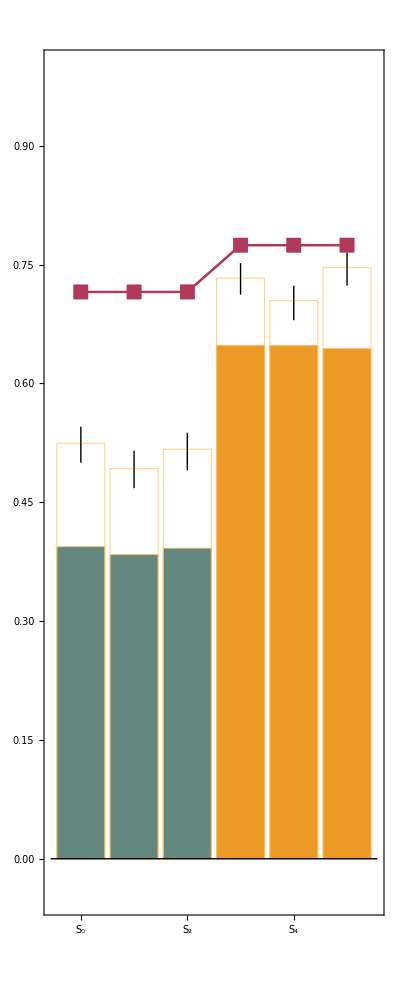
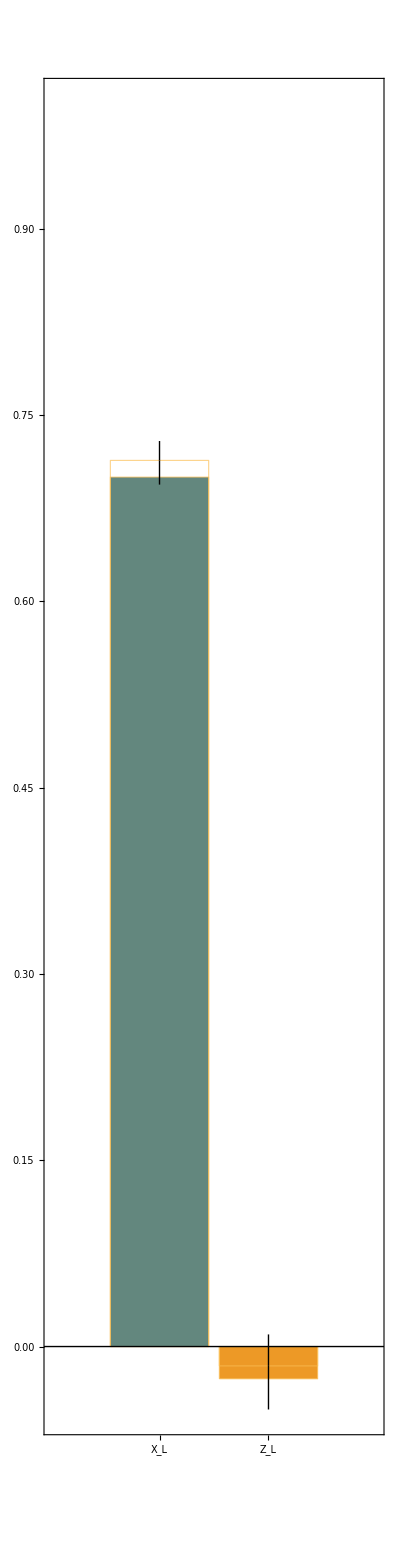
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

```mathematica
nshots=1000;
opt={
ProbBFRot-><|10->0.15,01->0.0005|>,
ProbLeakCZ-><|10->0.1,11->0.001|>,
HeatFactor->10
};
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
Print@Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
```

### Brute force many config of errors

```mathematica
Options@RydbergHub
```

{QubitNum→7,AtomLocations→<|6→{0,1},5→{1,1},2→{2,1},1→{4,1},4→{2,0},0→{4,0},3→{5,0}|>,T2→1.5×10^6,VacLifeTime→48000000,RabiFreq→1,ProbBFRot→<|10→0.001,1→0.03|>,UnitLattice→3,BlockadeRadius→1,ProbLeakInit→0.001,DurInit→500000,DurMove→100,HeatFactor→10,FidMeas→0.975,DurMeas→10,ProbLossMeas→0.0001,ProbLeakCZ→<|1→0.01,11→0.0001|>}

```mathematica
(* try some combinations of error parameters *)
bfrot=Flatten@Table[<|10->i,01->j|>,{i,{0.1,0.08,0.01}},{j,{0.001,0.01,0.03}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.02,0.03,0.04}},{j,{0.001,0.0001}}];
heat={10,50,100};
options=Flatten[Table[{ProbBFRot->i,ProbLeakCZ->k,HeatFactor->l},{i,bfrot},{k,probleakcz},{l,heat}],2];
Length@options
```

162

```mathematica
steane7={};
```

```mathematica
nshots=10000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[2]],Values@out[[3]]],Break[]]
];
```

```mathematica
opt={
ProbBFRot-><|10->0.15,01->0.0005|>,
ProbLeakCZ-><|10->0.1,11->0.001|>,
HeatFactor->10
};
```

```mathematica
(* try some combinations of error parameters *)
bfrot=Flatten@Table[<|10->i,01->j|>,{i,{0.1,0.12,0.13}},{j,{0.0005,0.0001}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.1}},{j,{0.0001,0.001,0.005}}];
heat={10,100};
options=Flatten[Table[{ProbBFRot->i,ProbLeakCZ->k,HeatFactor->l},{i,bfrot},{k,probleakcz},{l,heat}],2];
Length@options
```

36

Trial 1: {ProbBFRot→<|10→0.1,1→0.001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→10}

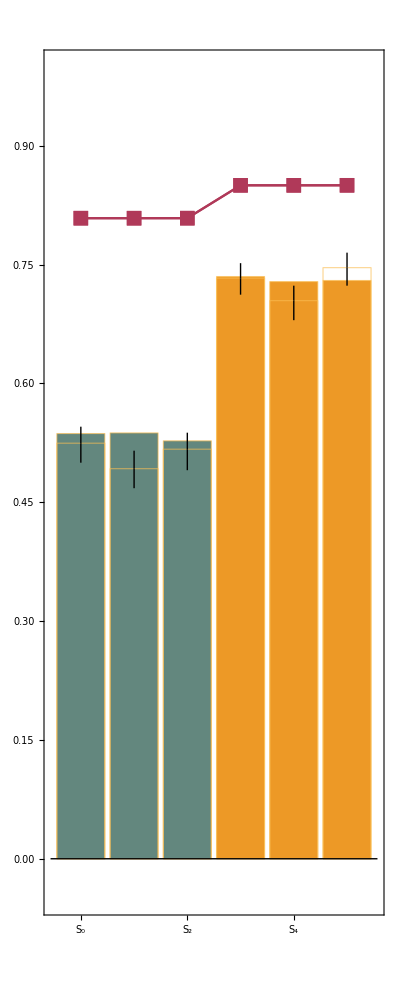
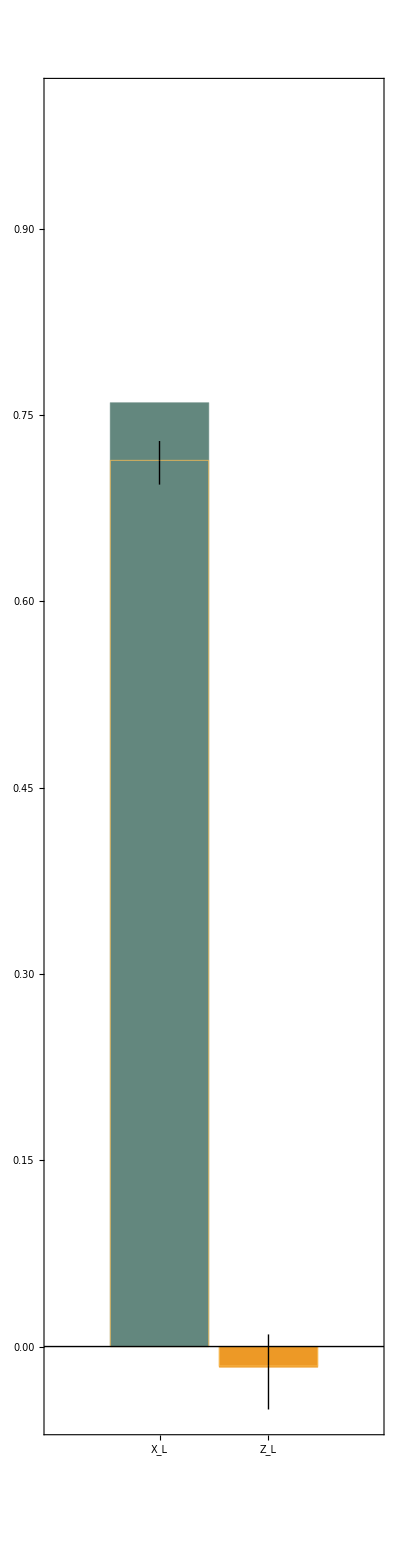
{-Graphics--Graphics-,<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 2: {ProbBFRot→<|10→0.1,1→0.001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→100}

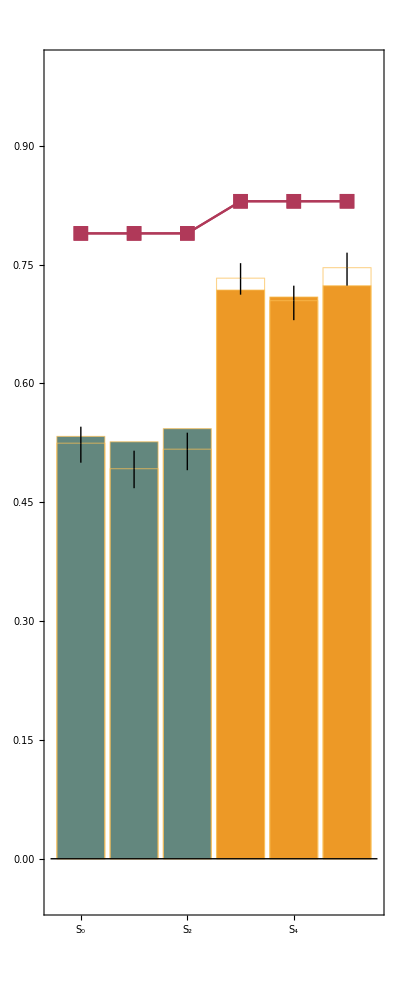
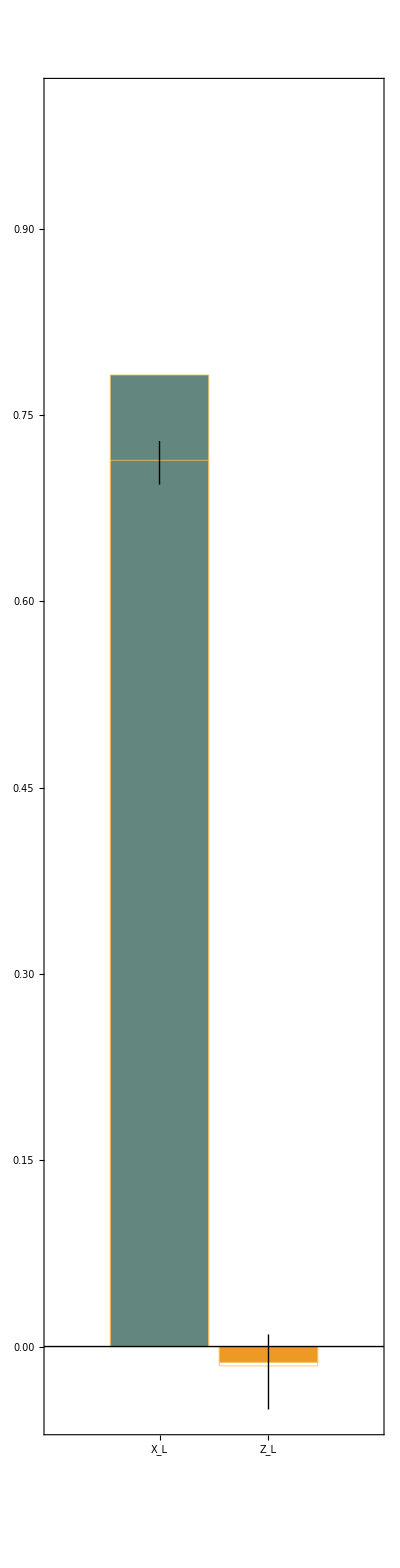
{-Graphics--Graphics-,<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 3: {ProbBFRot→<|10→0.1,1→0.001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→10}

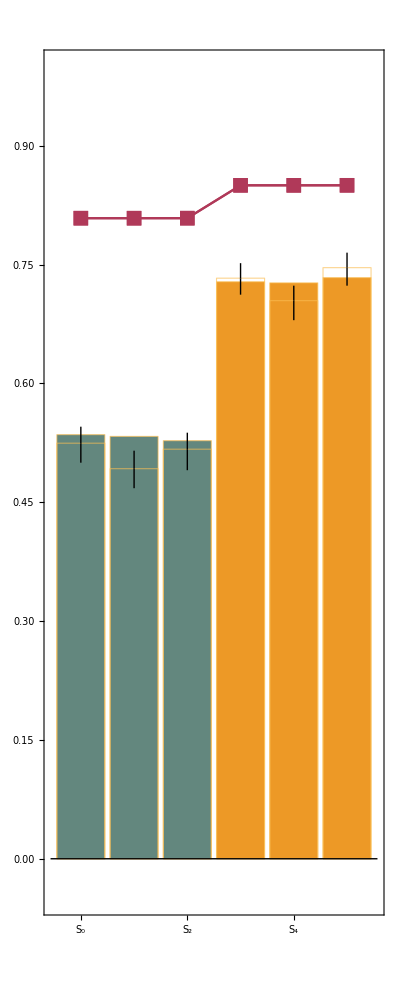
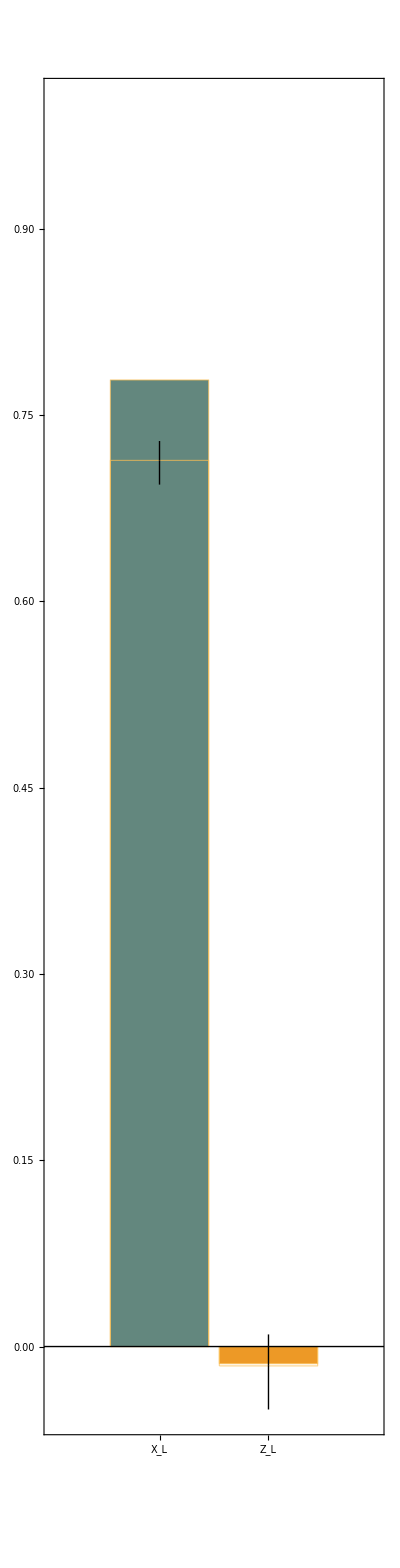
{-Graphics--Graphics-,<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 4: {ProbBFRot→<|10→0.1,1→0.001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→100}

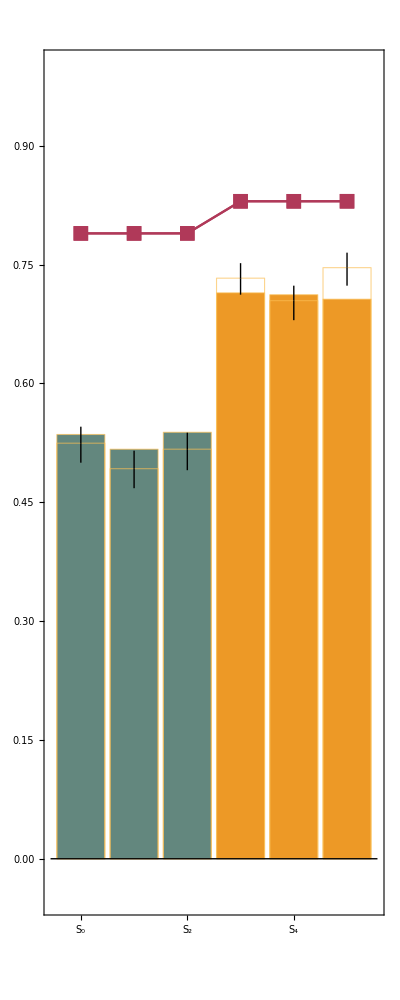
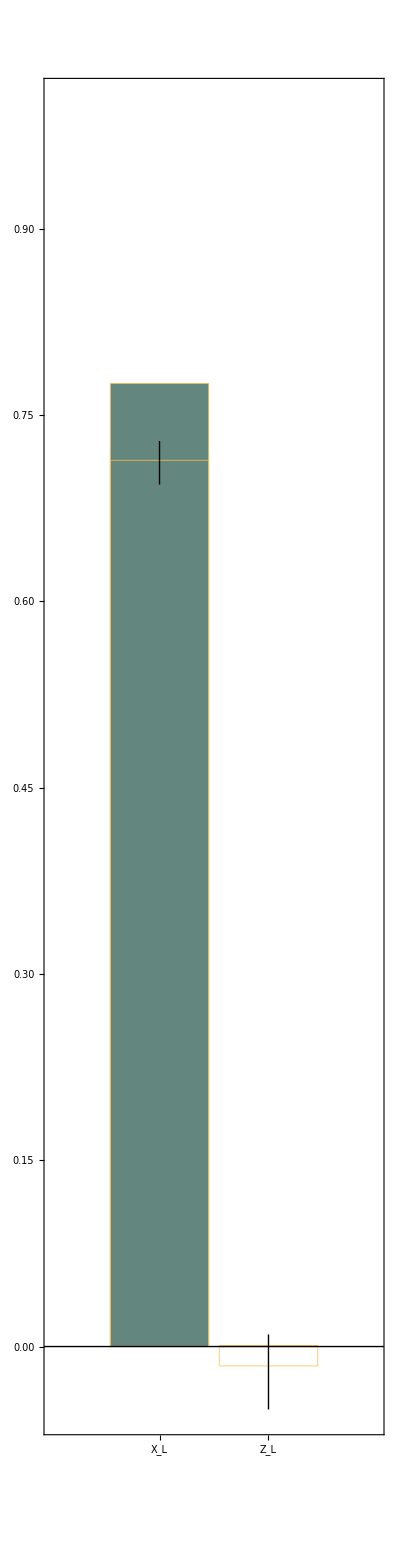
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 5: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→10}

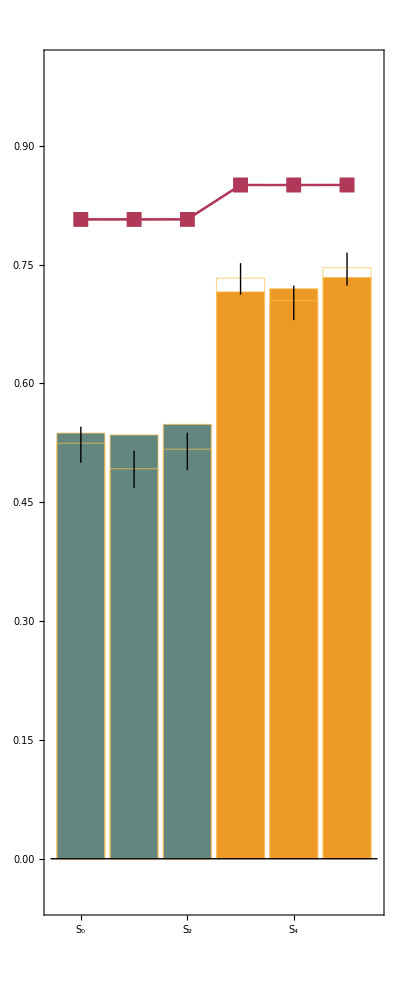
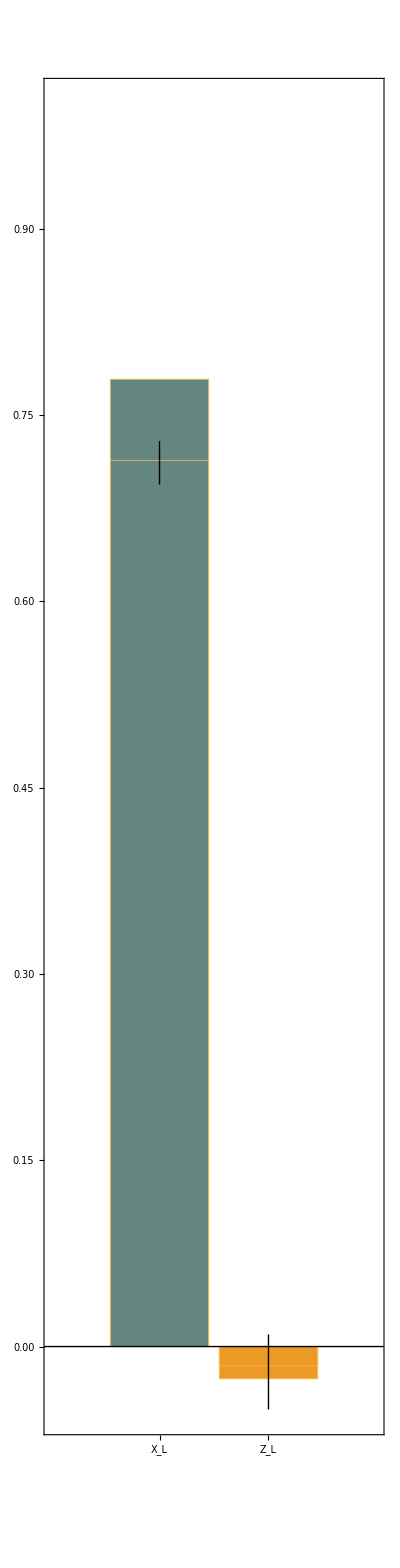
{-Graphics--Graphics-,<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 6: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→100}

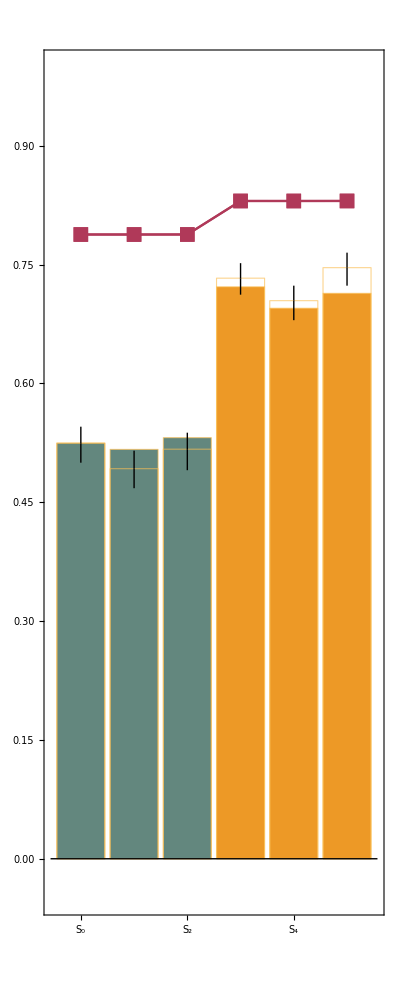
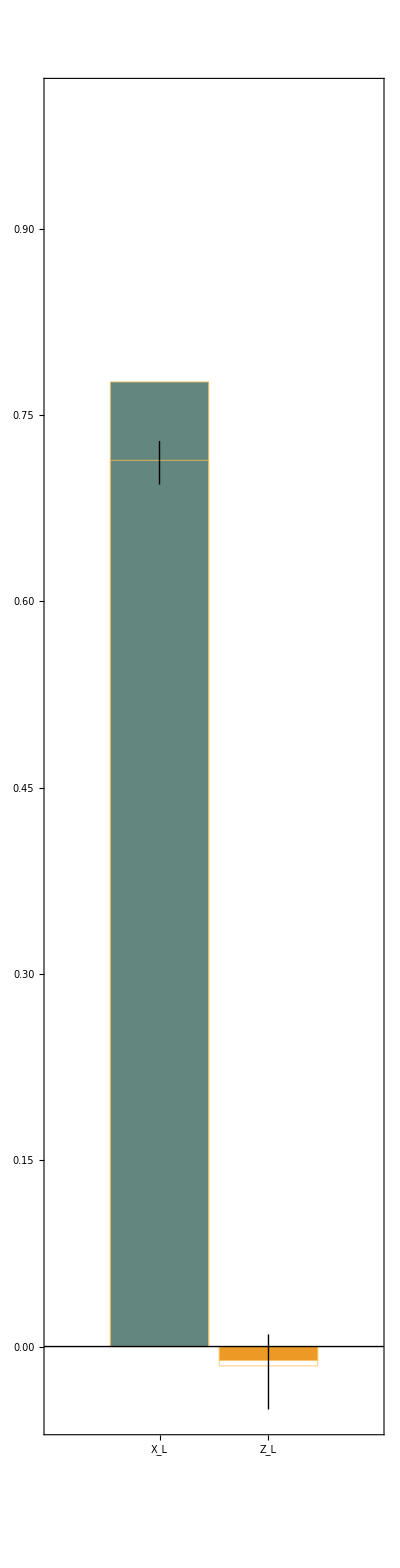
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 7: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→10}

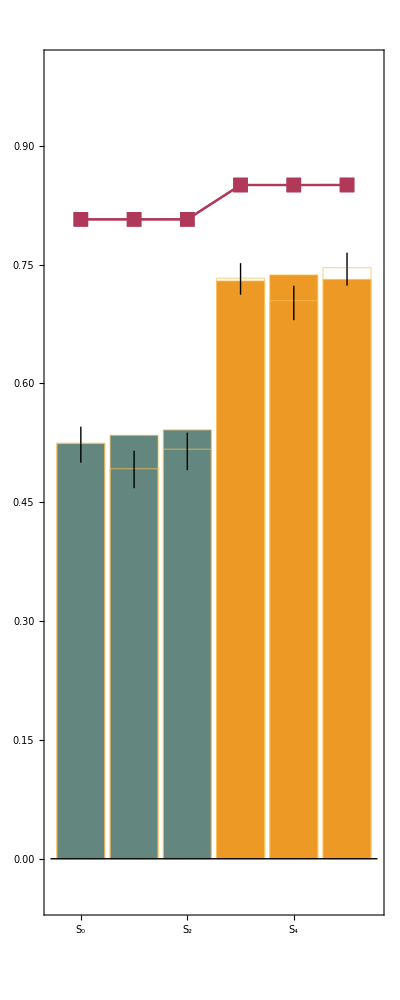
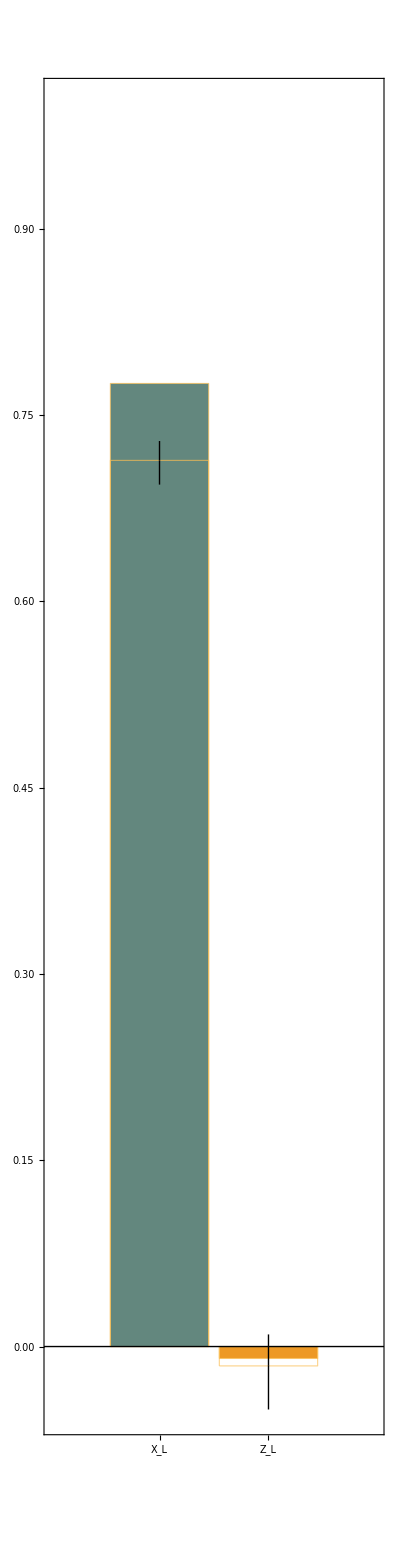
{-Graphics--Graphics-,<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 8: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→100}

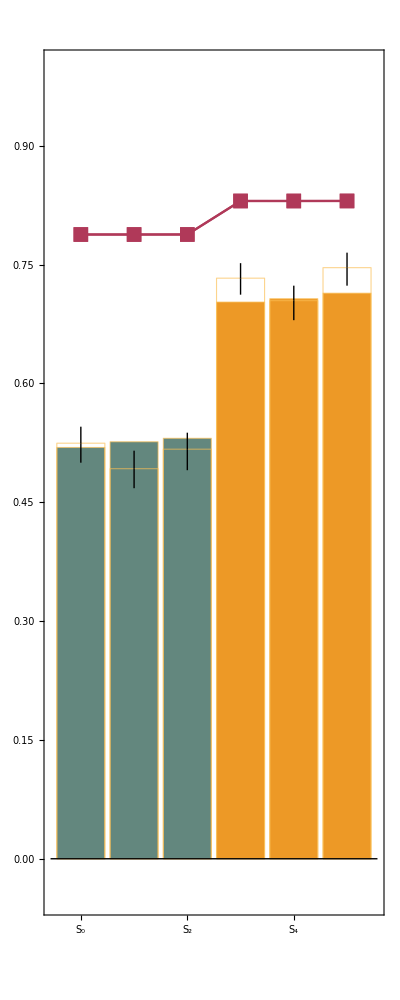
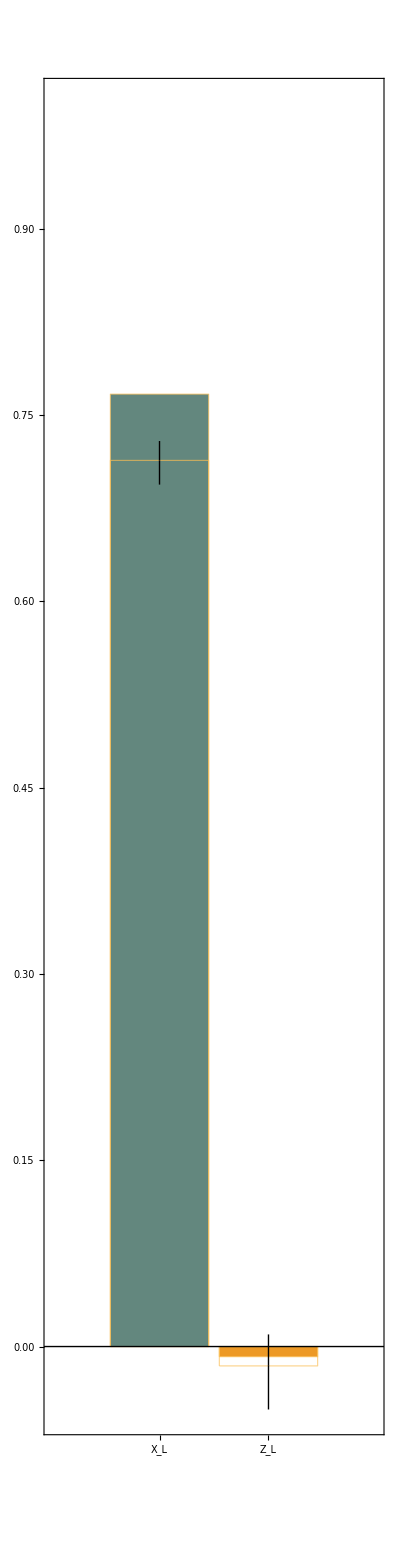
{-Graphics--Graphics-,<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 9: {ProbBFRot→<|10→0.15,1→0.001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→10}

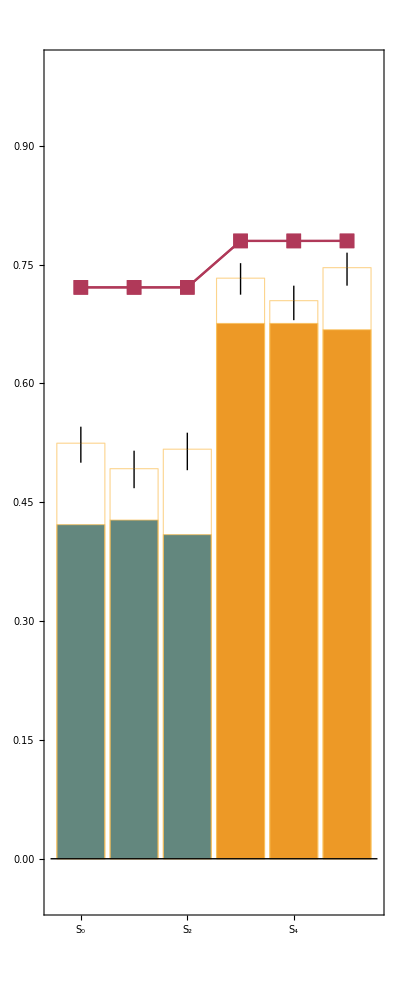
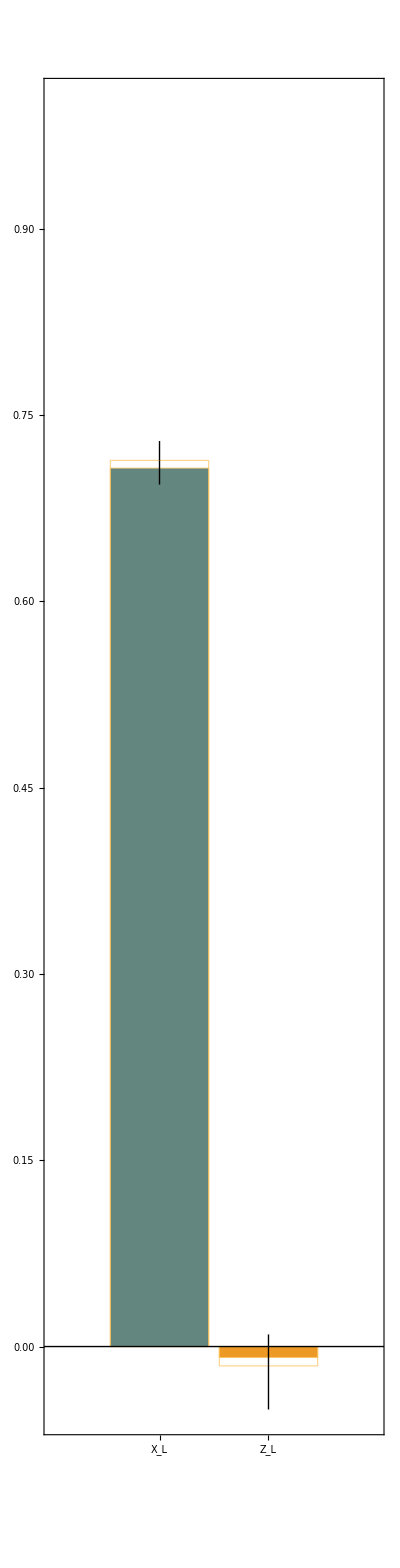
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 10: {ProbBFRot→<|10→0.15,1→0.001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→100}

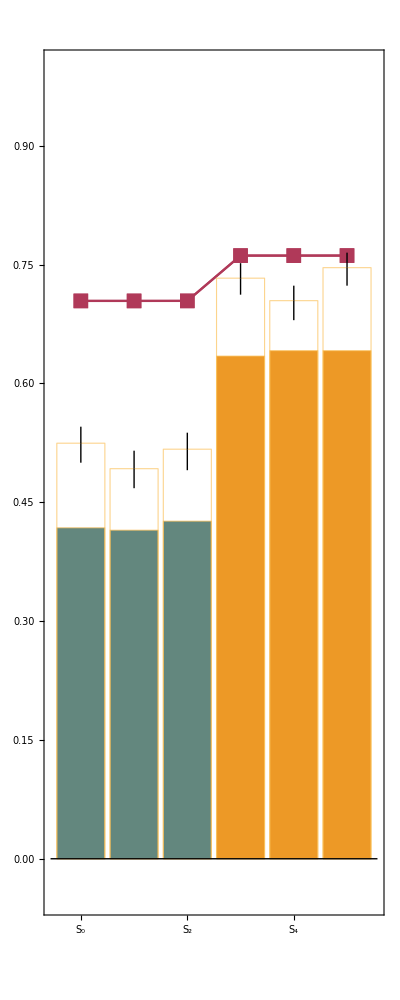
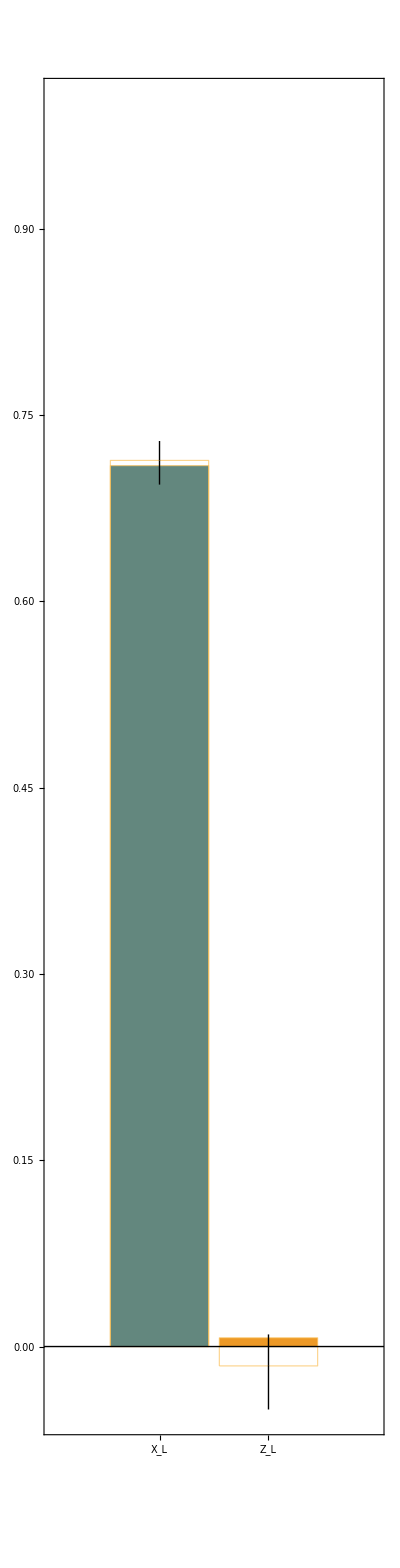
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 11: {ProbBFRot→<|10→0.15,1→0.001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→10}

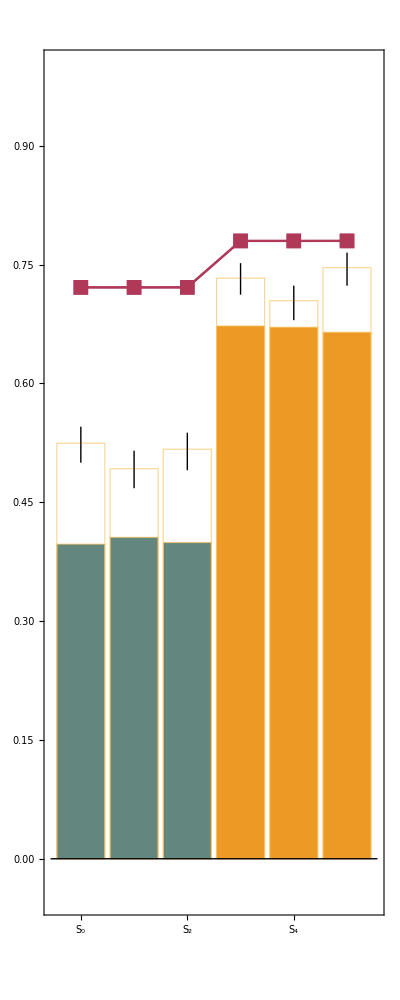
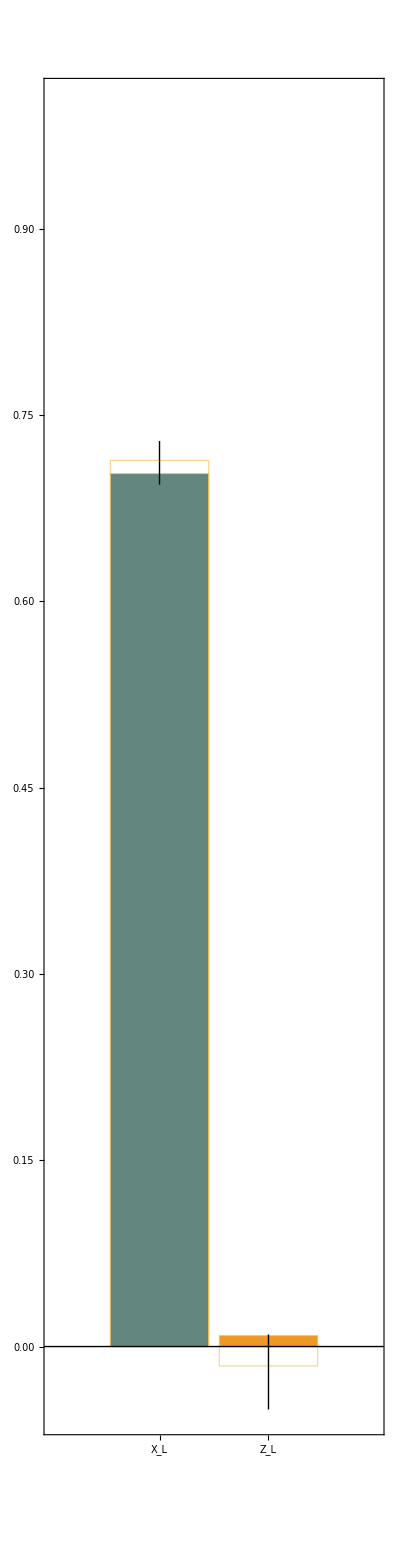
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 12: {ProbBFRot→<|10→0.15,1→0.001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→100}

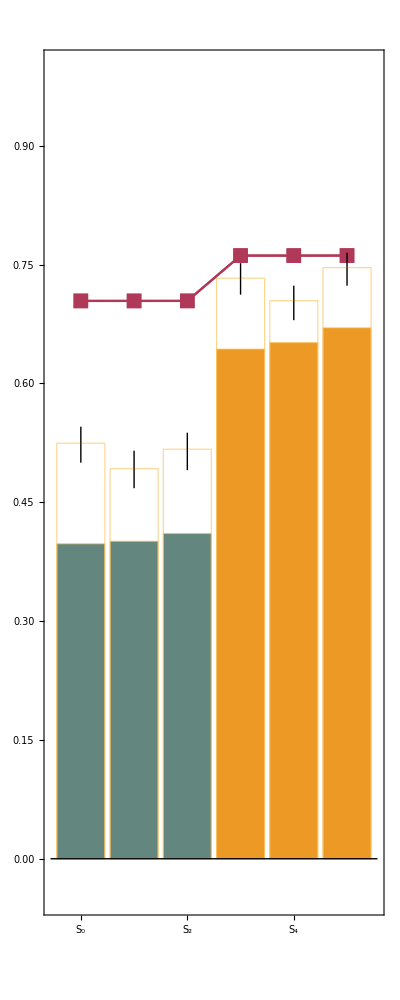
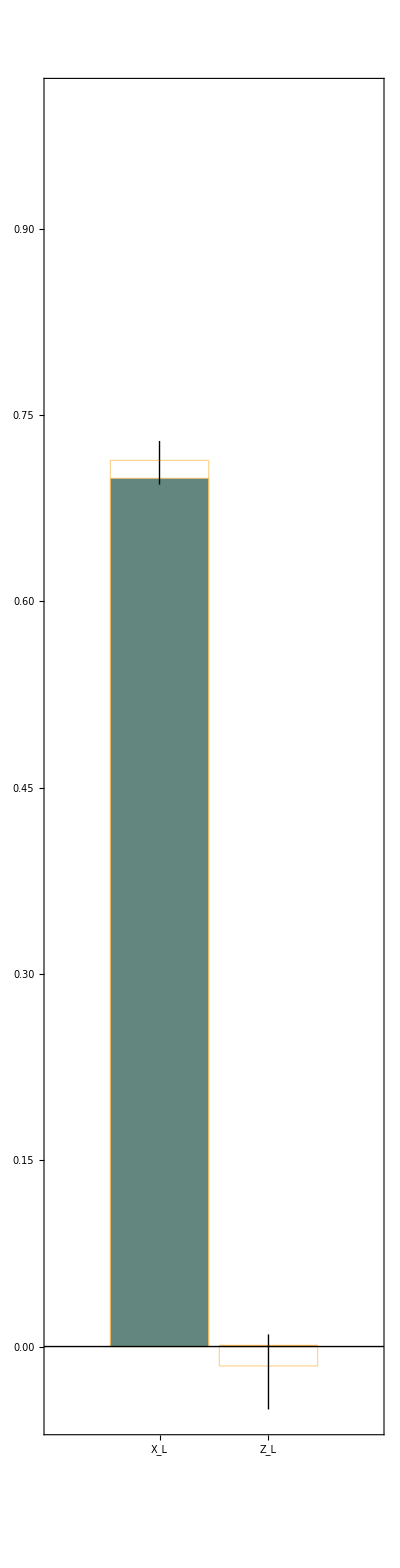
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 13: {ProbBFRot→<|10→0.15,1→0.0001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→10}

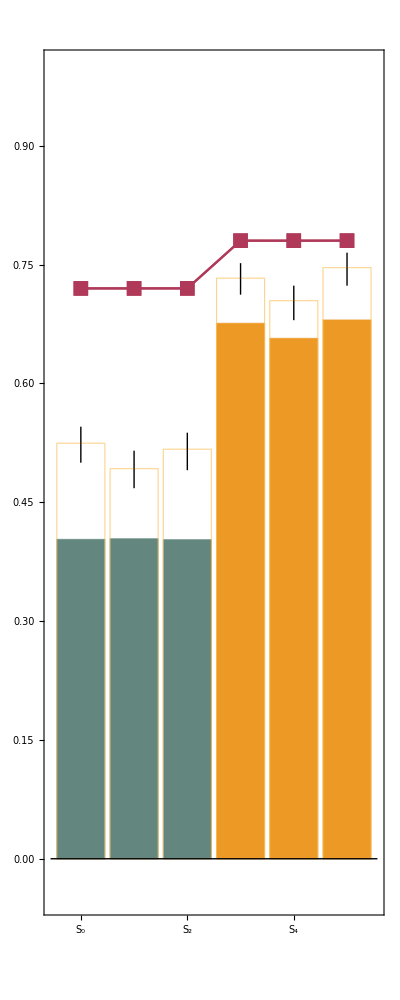
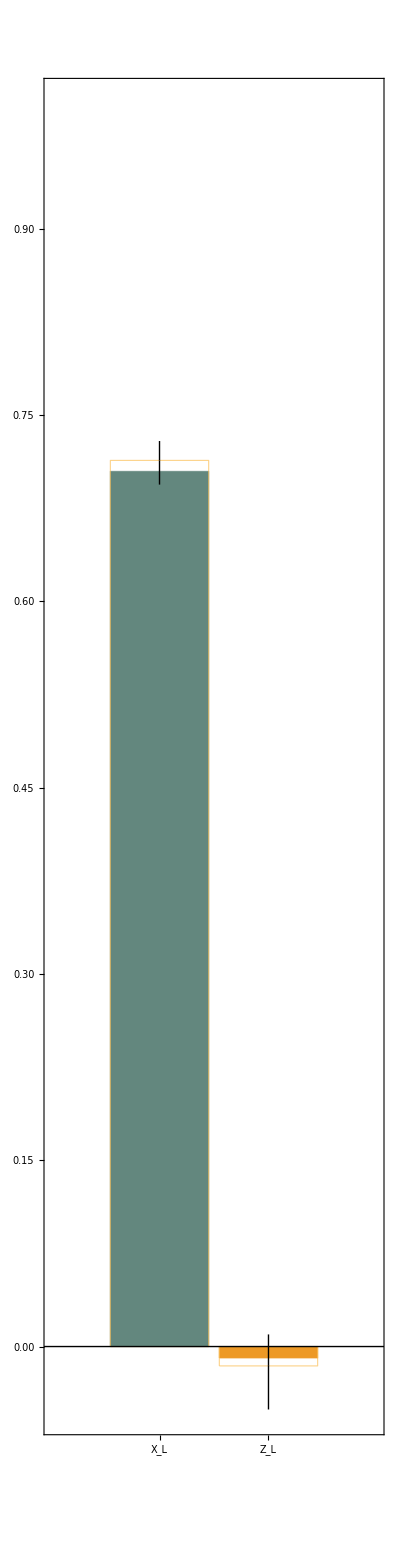
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 14: {ProbBFRot→<|10→0.15,1→0.0001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→100}

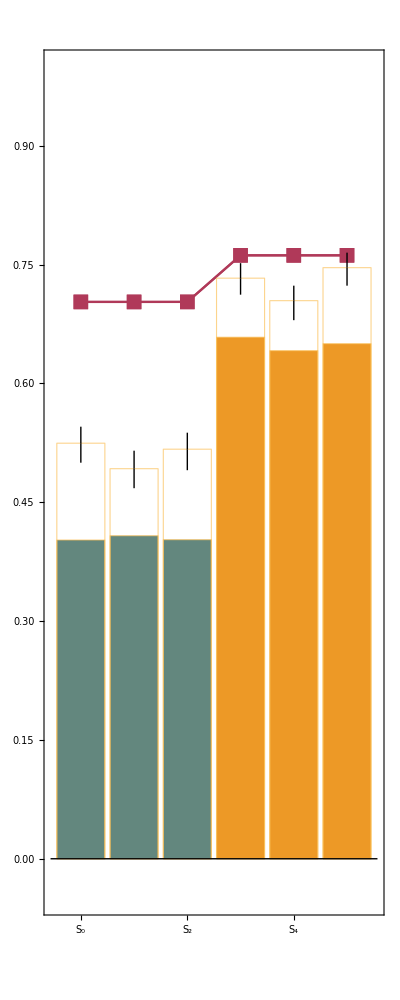
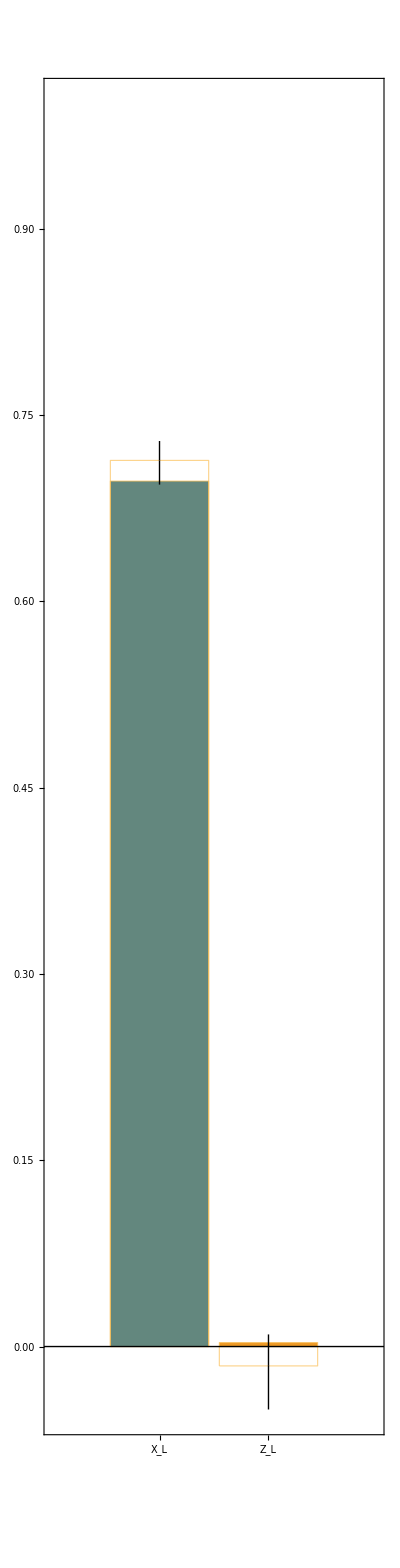
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 15: {ProbBFRot→<|10→0.15,1→0.0001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→10}

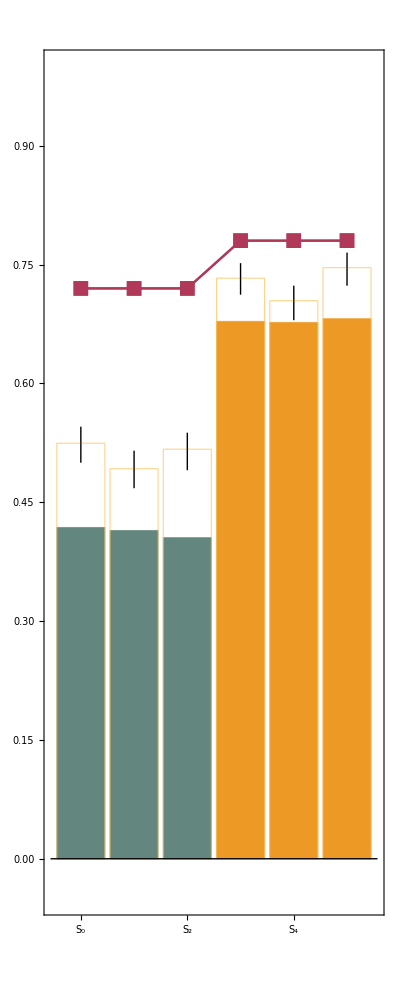
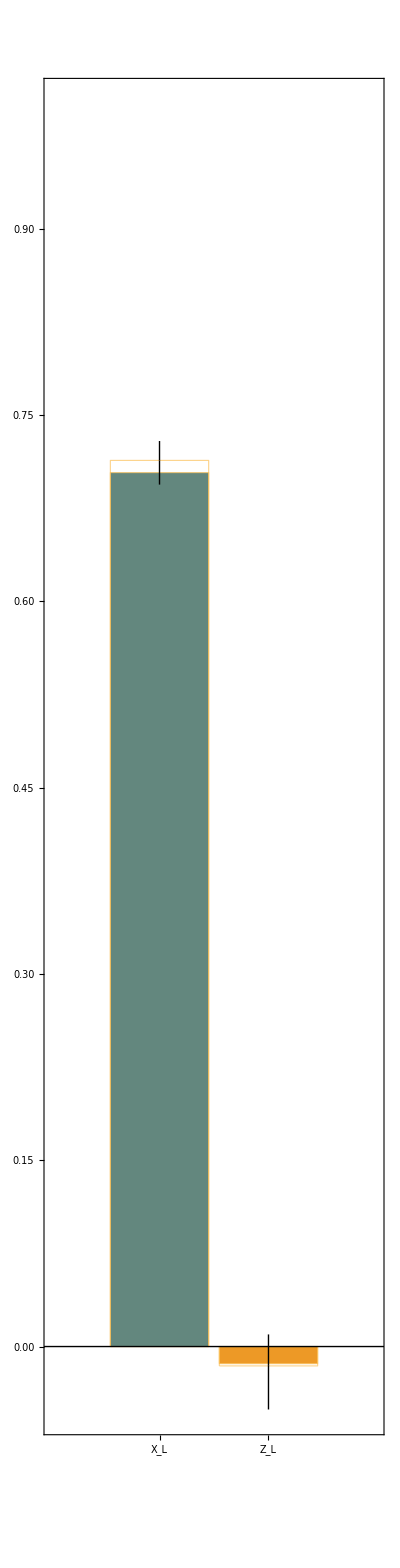
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 16: {ProbBFRot→<|10→0.15,1→0.0001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→100}

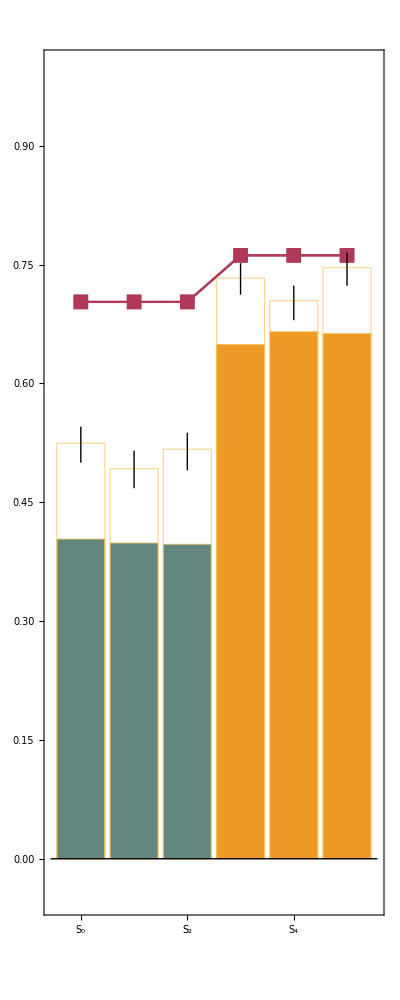
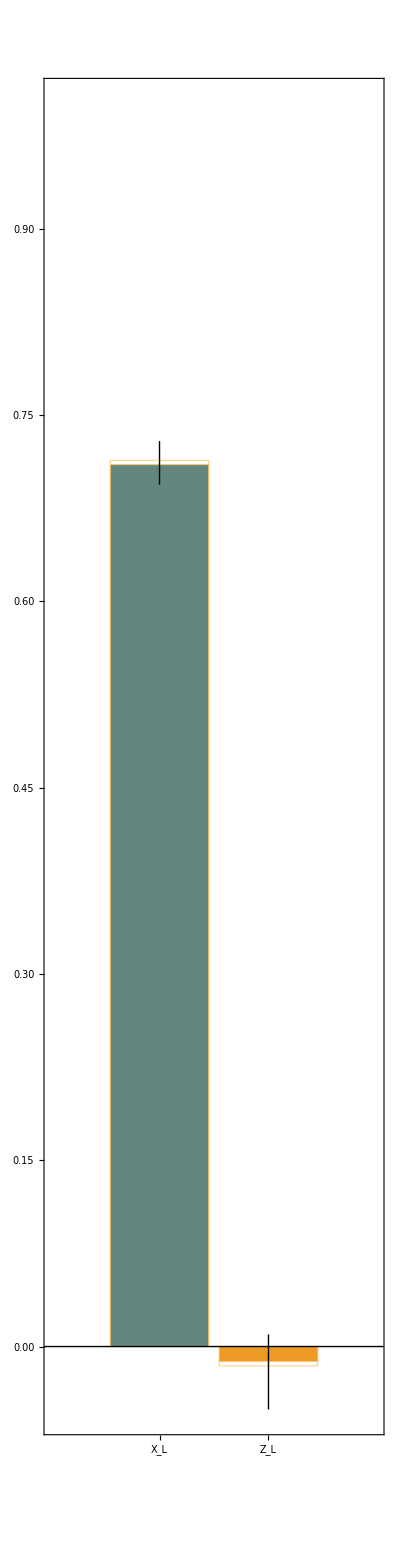
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 17: {ProbBFRot→<|10→0.2,1→0.001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→10}

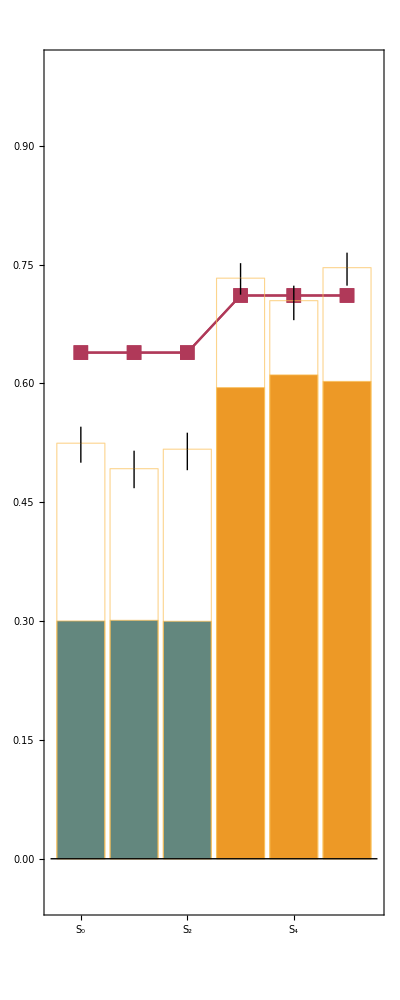
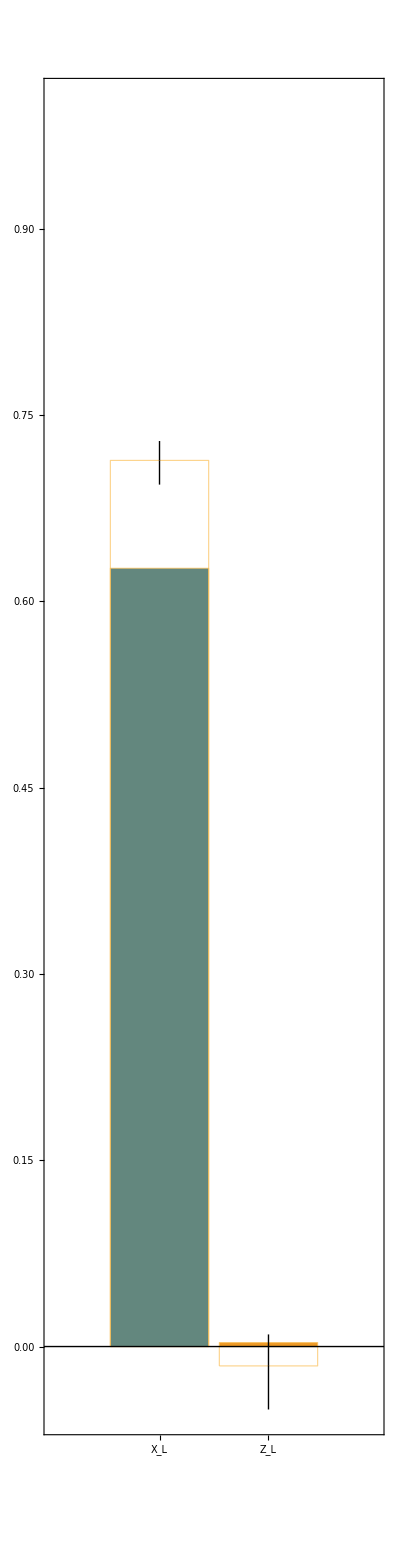
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 18: {ProbBFRot→<|10→0.2,1→0.001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→100}

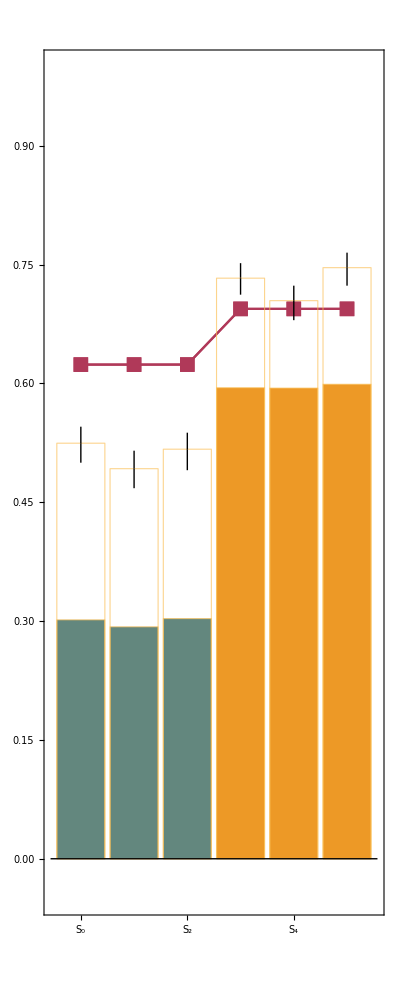
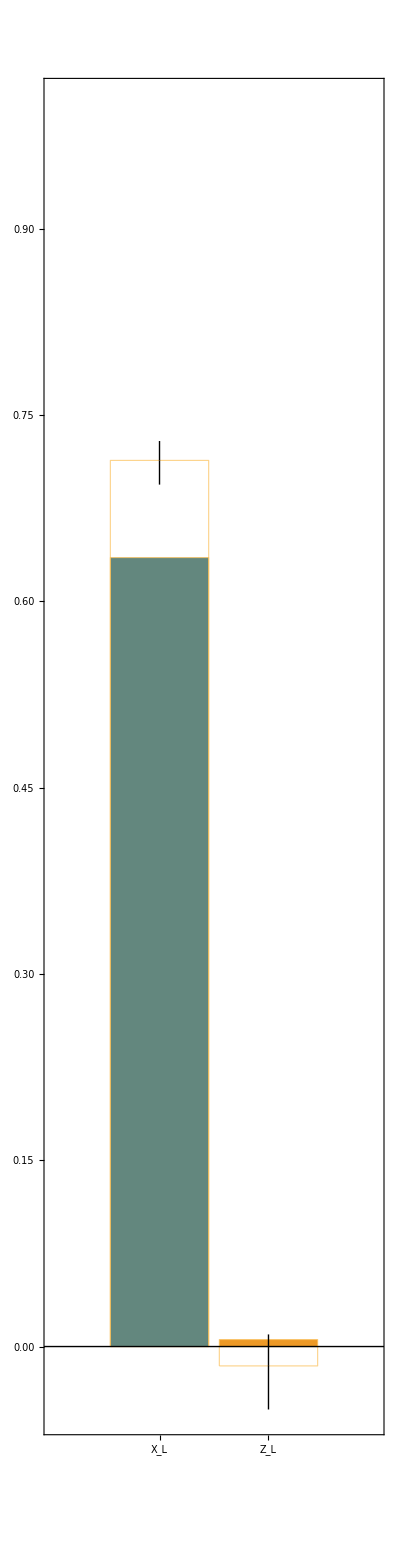
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 19: {ProbBFRot→<|10→0.2,1→0.001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→10}

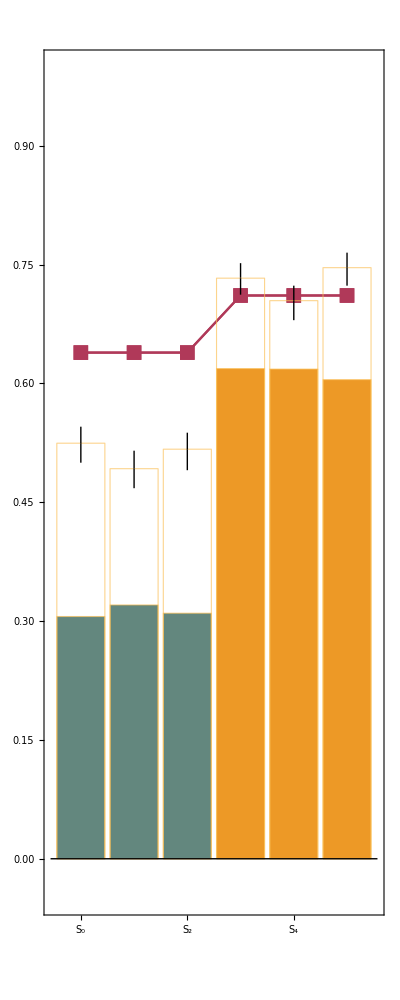
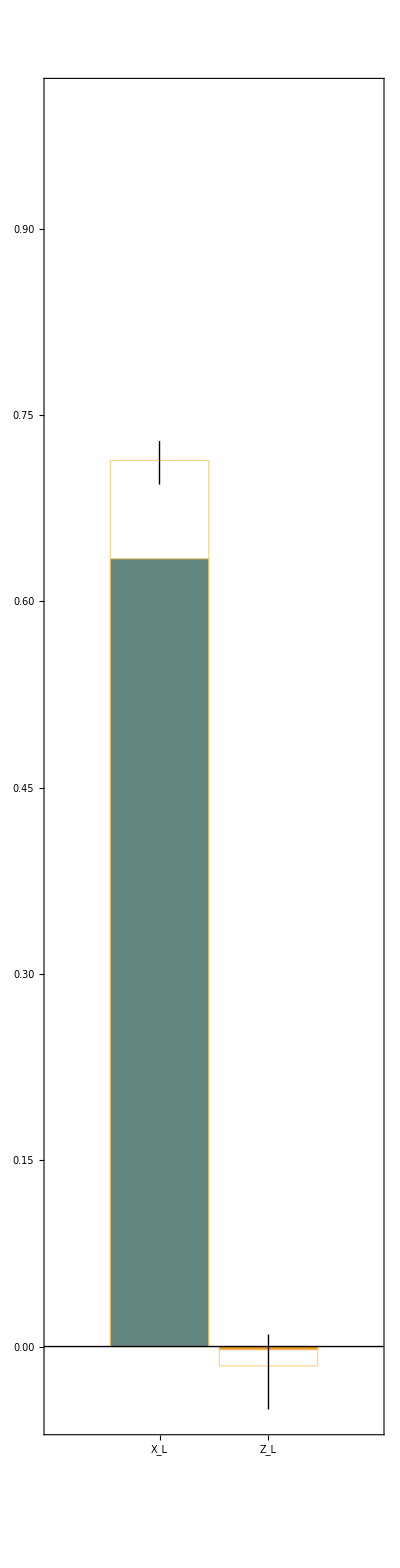
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 20: {ProbBFRot→<|10→0.2,1→0.001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→100}

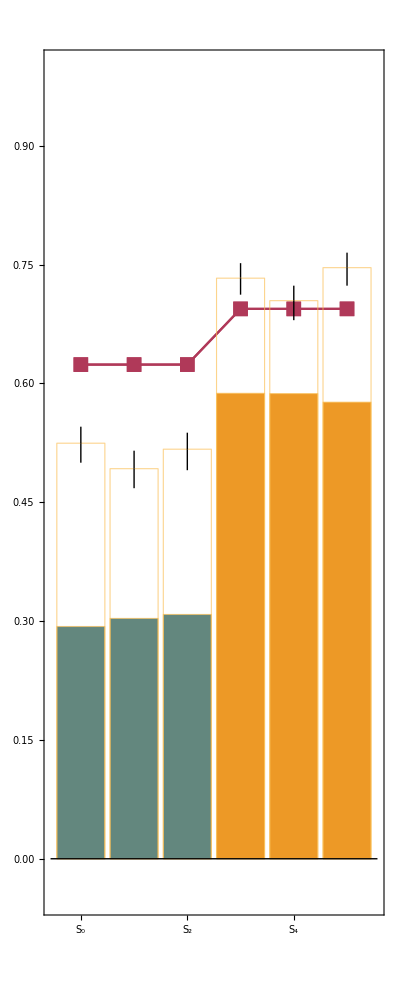
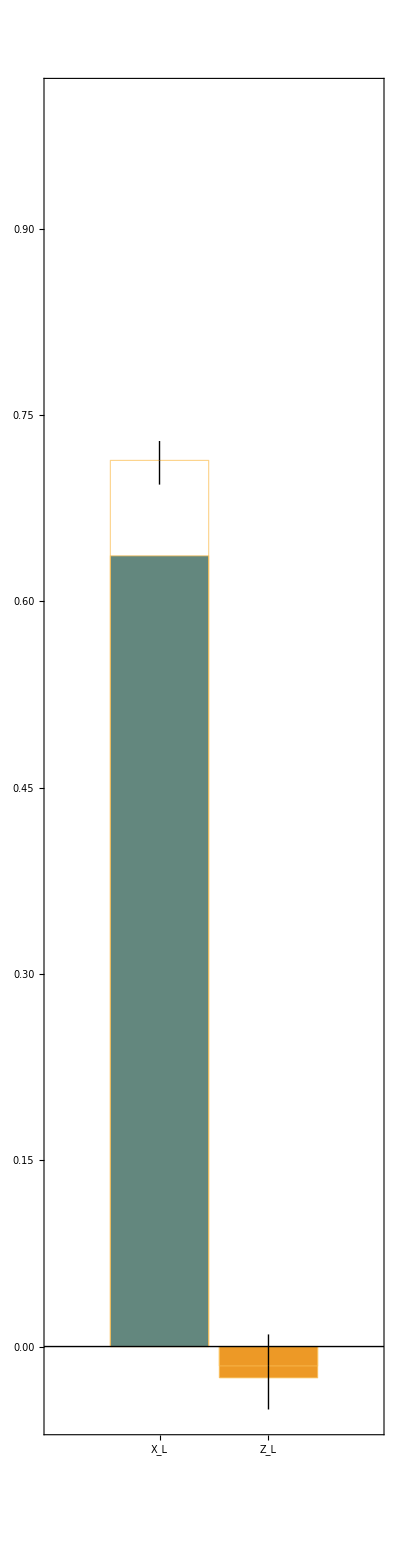
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 21: {ProbBFRot→<|10→0.2,1→0.0001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→10}

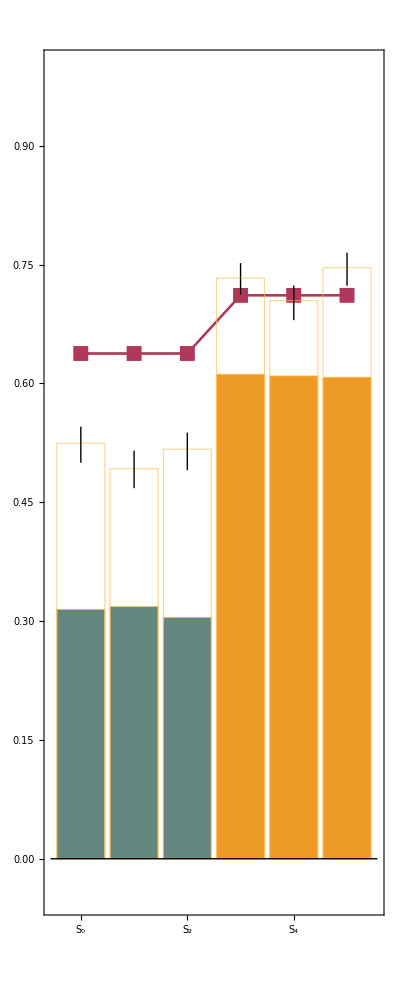
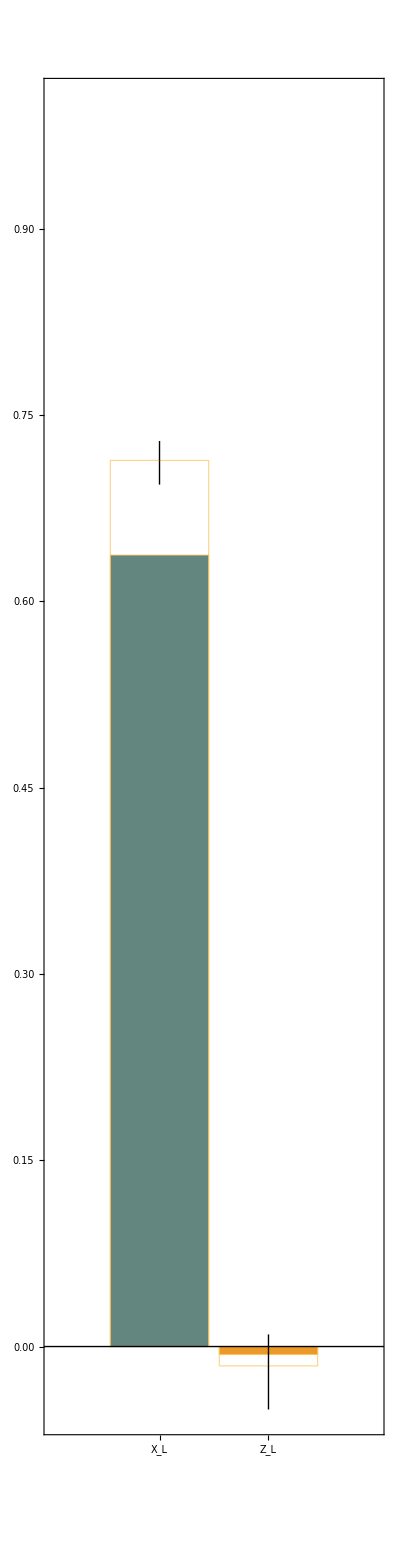
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 22: {ProbBFRot→<|10→0.2,1→0.0001|>,ProbLeakCZ→<|10→0.04,11→0.0001|>,HeatFactor→100}

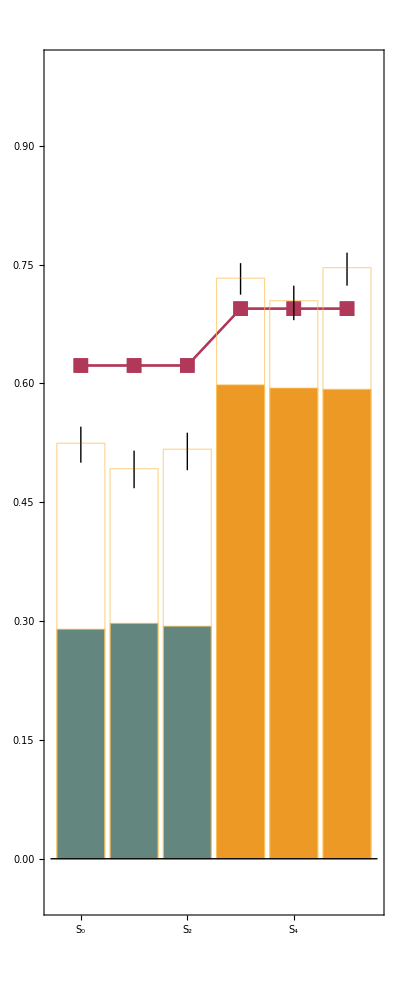
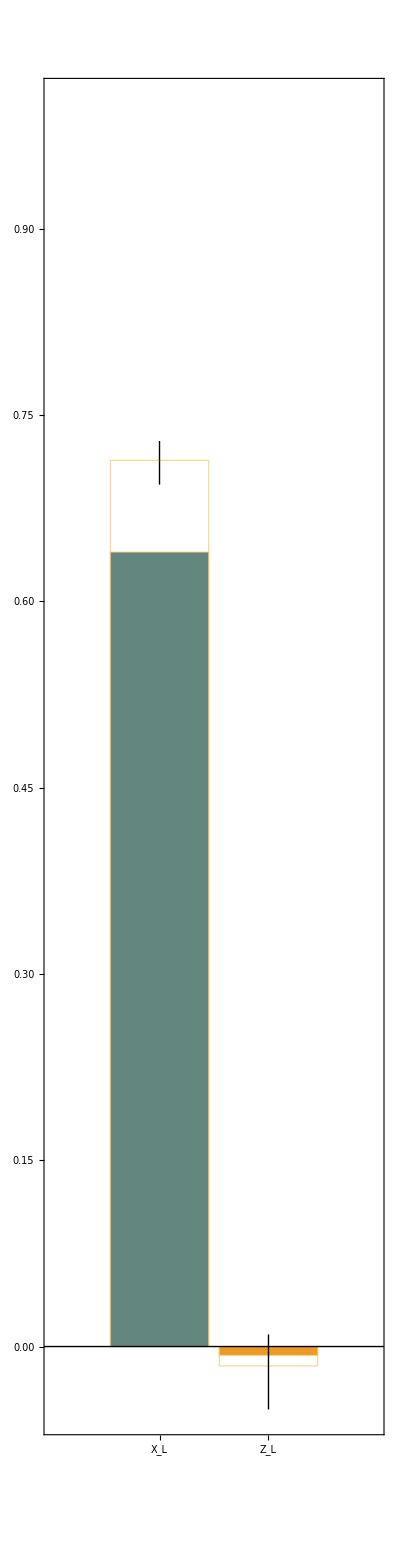
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 23: {ProbBFRot→<|10→0.2,1→0.0001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→10}

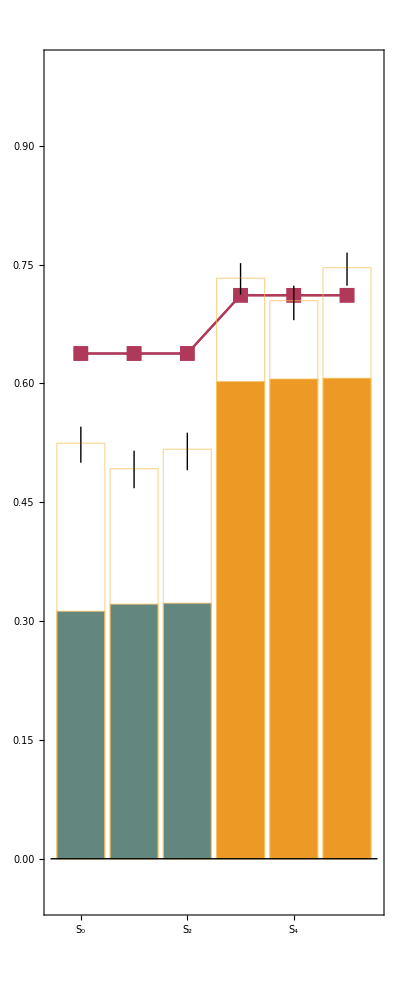
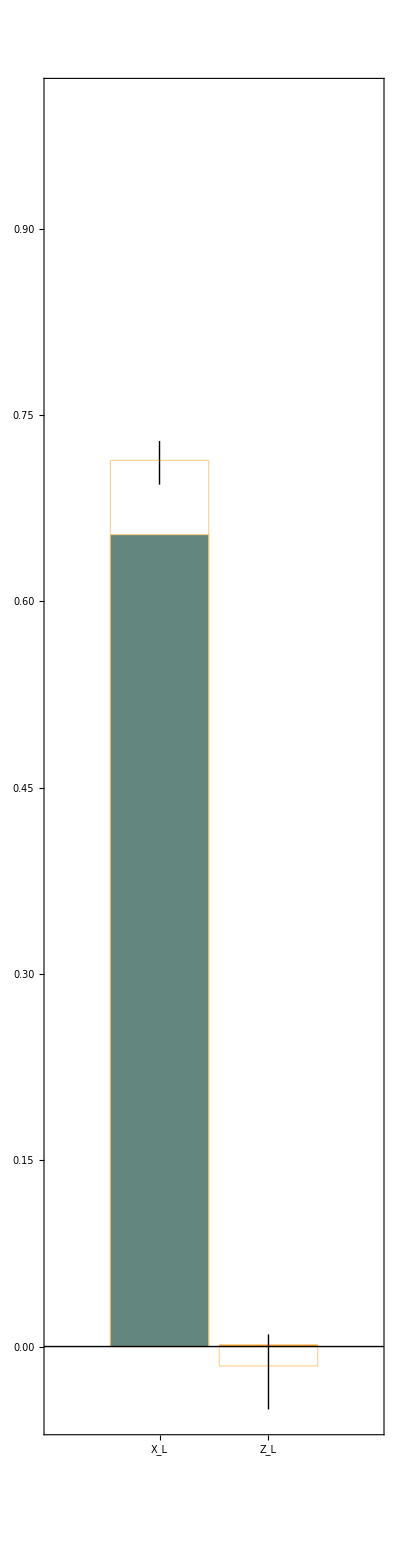
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 24: {ProbBFRot→<|10→0.2,1→0.0001|>,ProbLeakCZ→<|10→0.06,11→0.0001|>,HeatFactor→100}

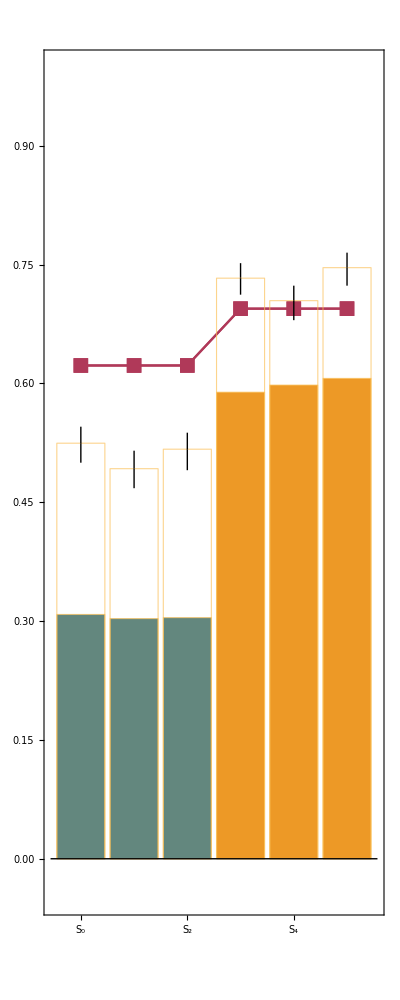
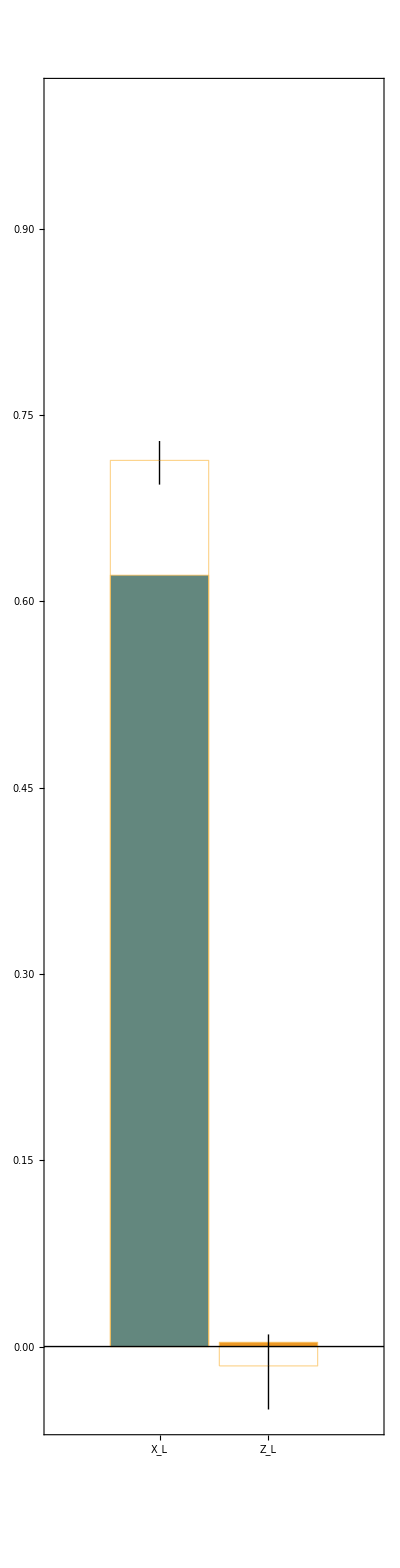
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

```mathematica
nshots=10000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[2]],Values@out[[3]]],Break[]]
]
```

```mathematica
(* try some combinations of error parameters *)
bfrot=Flatten@Table[<|10->i,01->j|>,{i,{0.1,0.11,0.08}},{j,{0.0004,0.0002,0.0001}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.1,0.11,0.08}},{j,{0.0001,0.0002,0.0004}}];
heat={10,100};
options=Flatten[Table[{ProbBFRot->i,ProbLeakCZ->k,HeatFactor->l},{i,bfrot},{k,probleakcz},{l,heat}],2];
Length@options
```

162

```mathematica
nshots=10000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[2]],Values@out[[3]]],Break[]]
];
```

```mathematica
(* try some combinations of error parameters *)
bfrot=Flatten@Table[<|10->i,01->j|>,{i,{0.11,0.12}},{j,{0.00008,0.0001}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.11,0.12}},{j,{0.0001,0.00008}}];
heat={2,8,64};
options=Flatten[Table[{ProbBFRot->i,ProbLeakCZ->k,HeatFactor->l},{i,bfrot},{k,probleakcz},{l,heat}],2];
Length@options
```

48

Trial 1: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

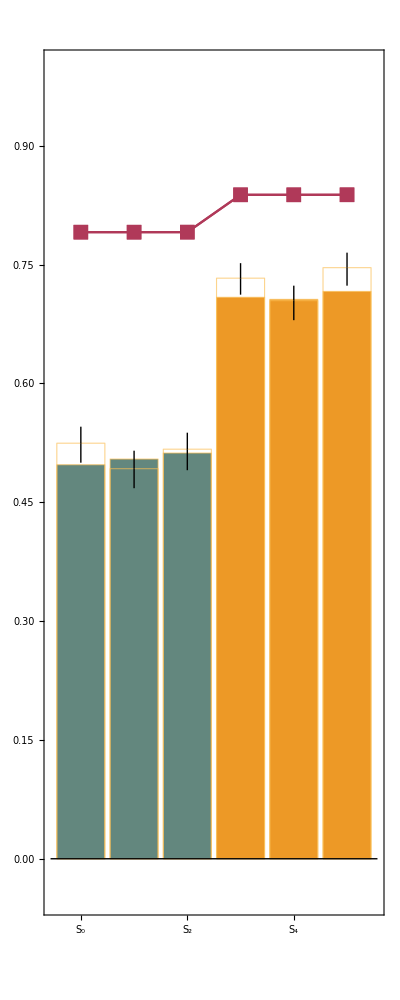
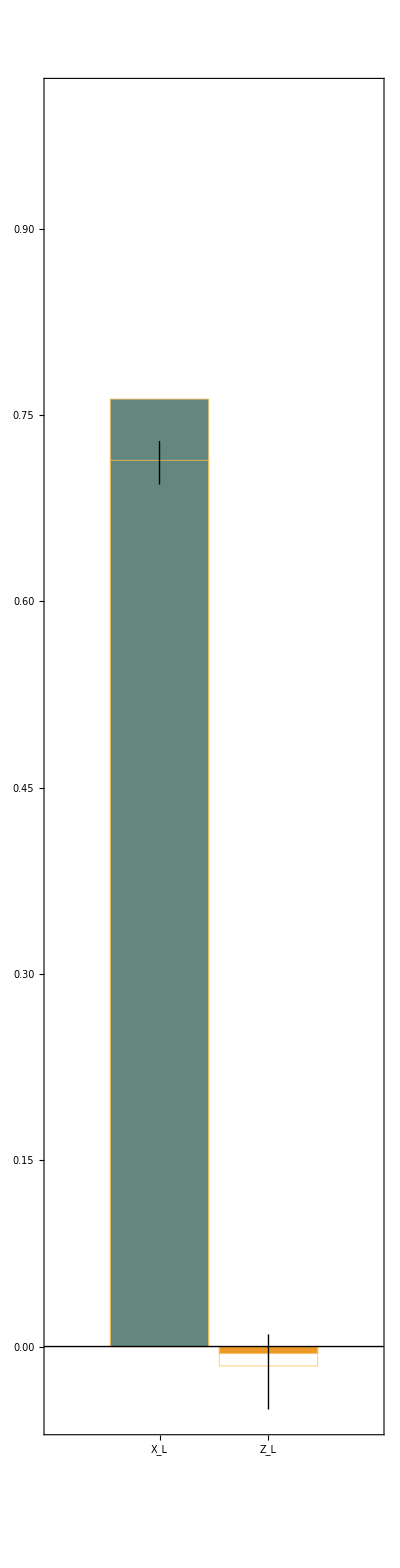
{-Graphics--Graphics-,<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 2: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

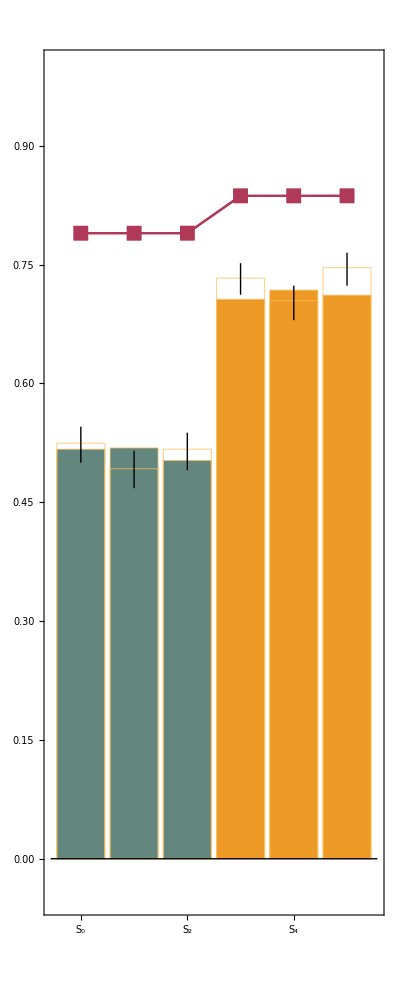
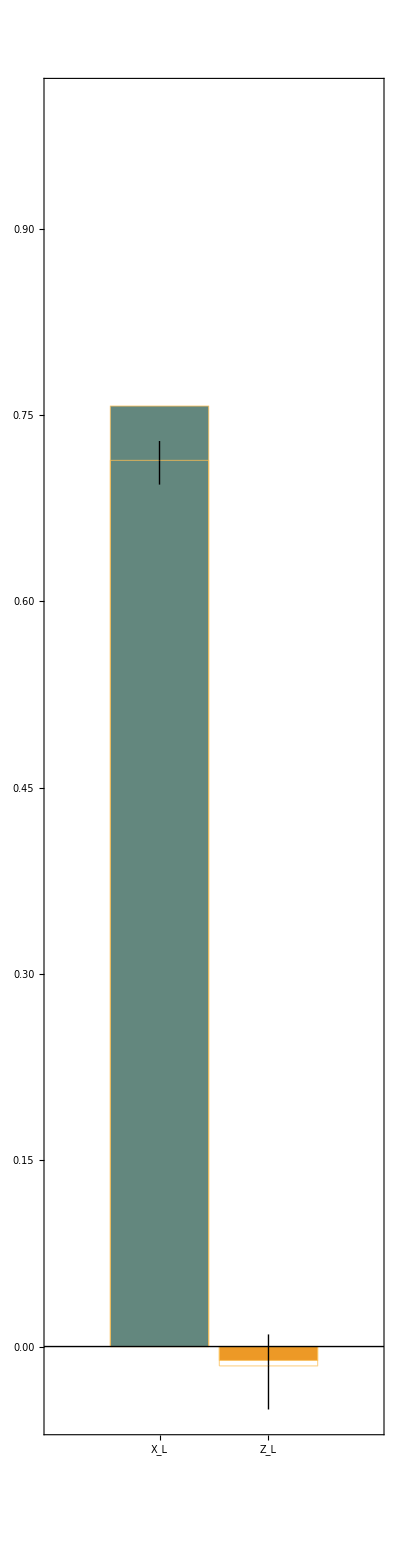
{-Graphics--Graphics-,<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 3: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

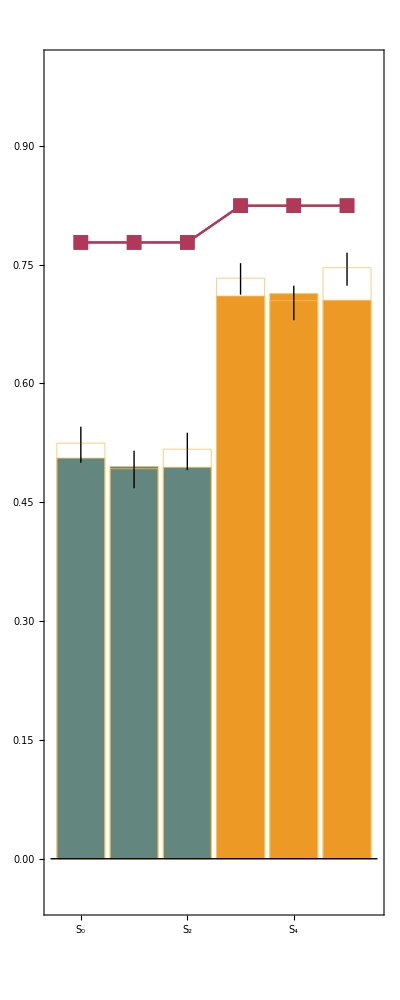
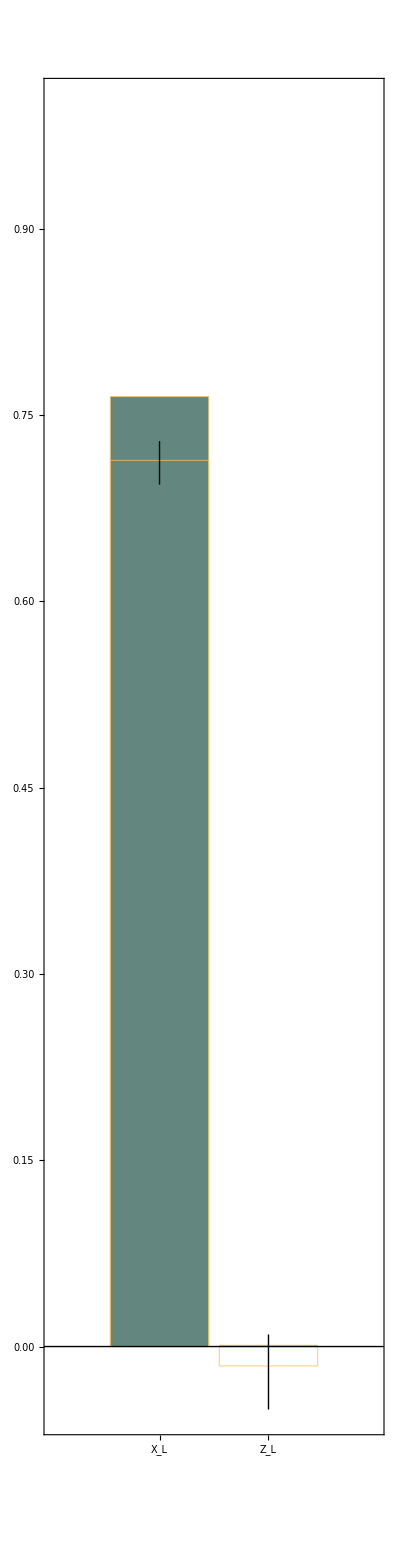
{-Graphics--Graphics-,<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 4: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

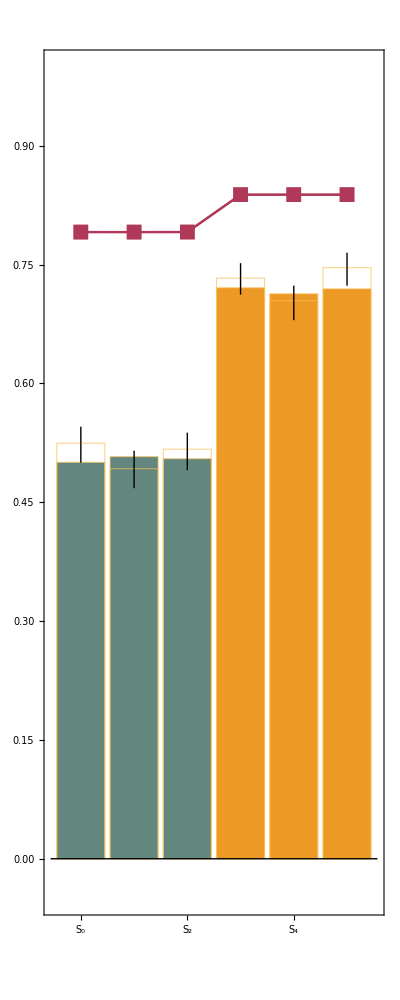
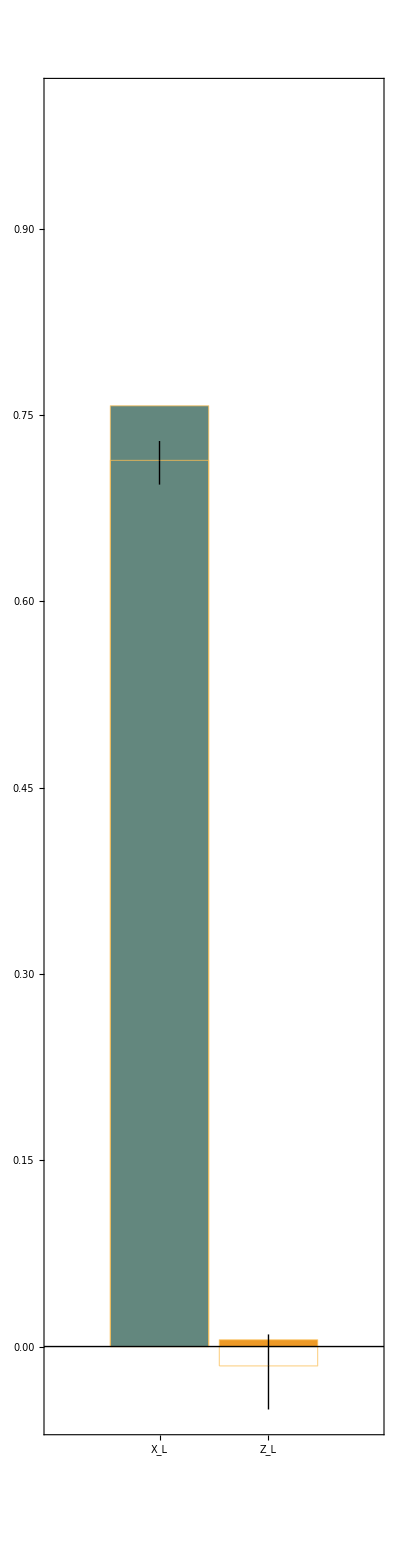
{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 5: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

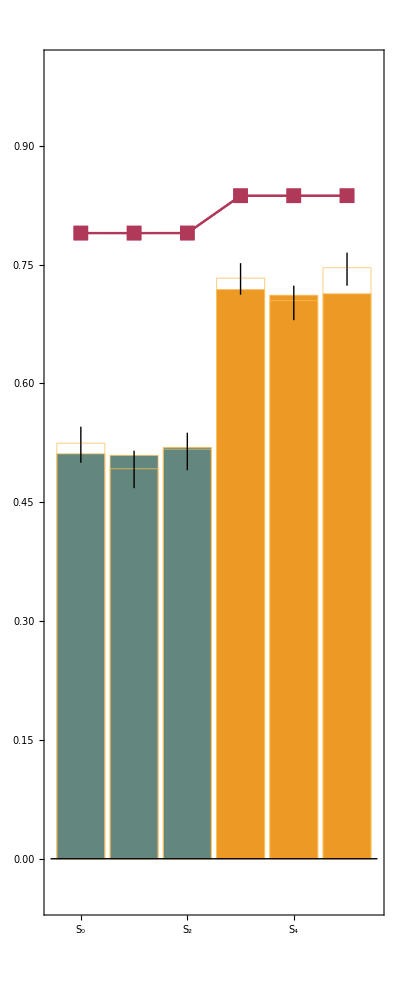
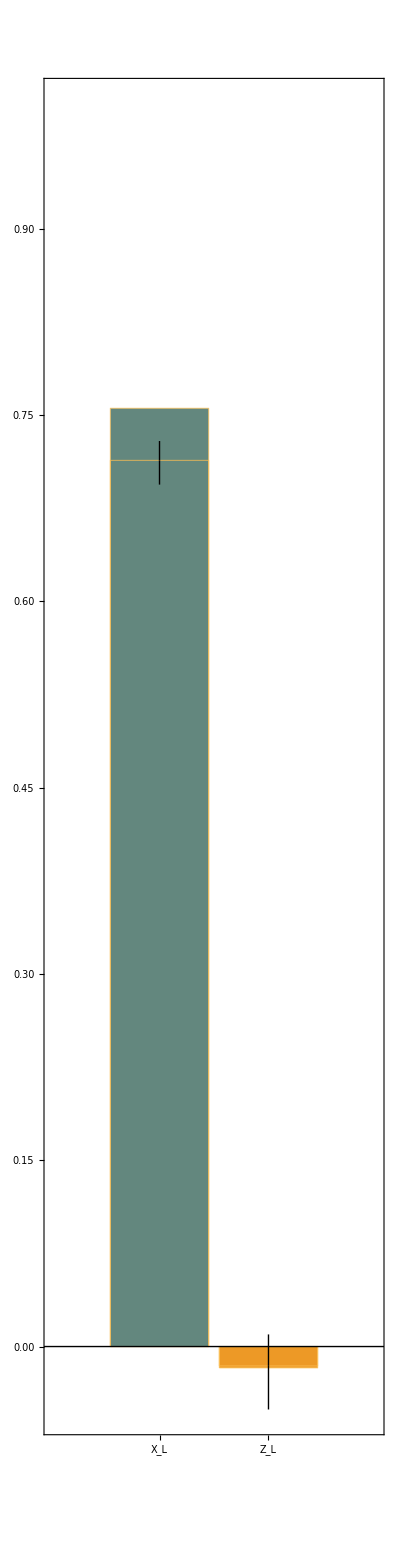
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 6: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

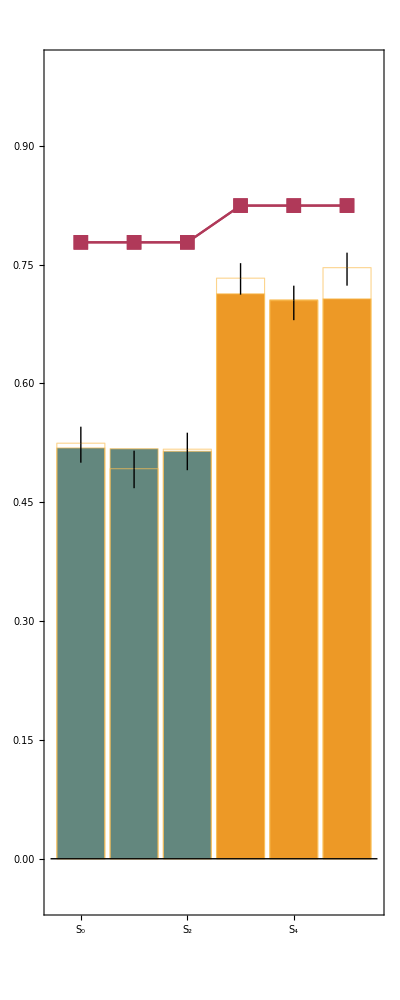
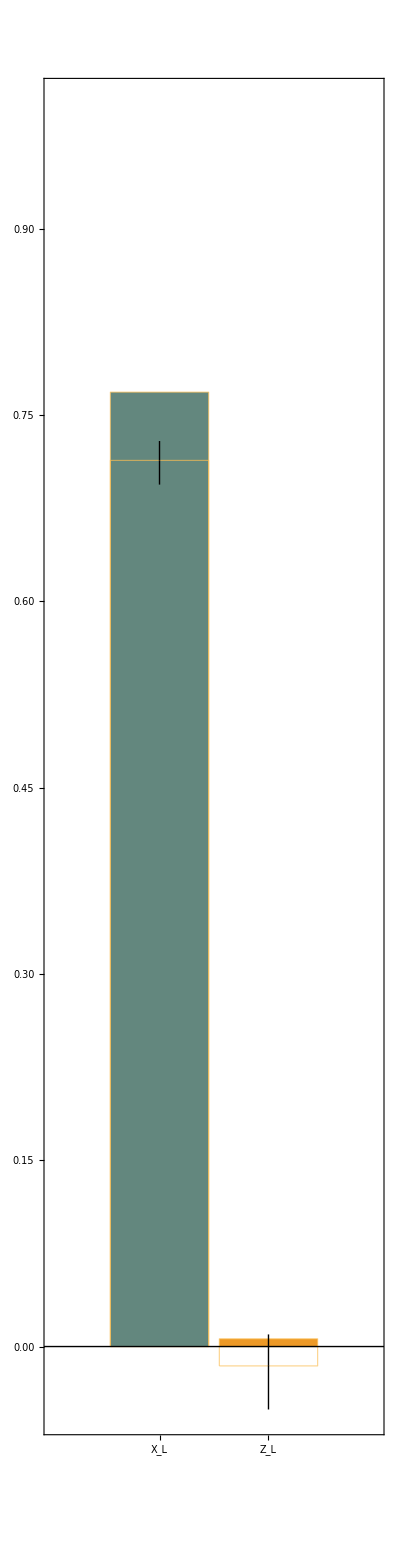
{-Graphics--Graphics-,<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 7: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

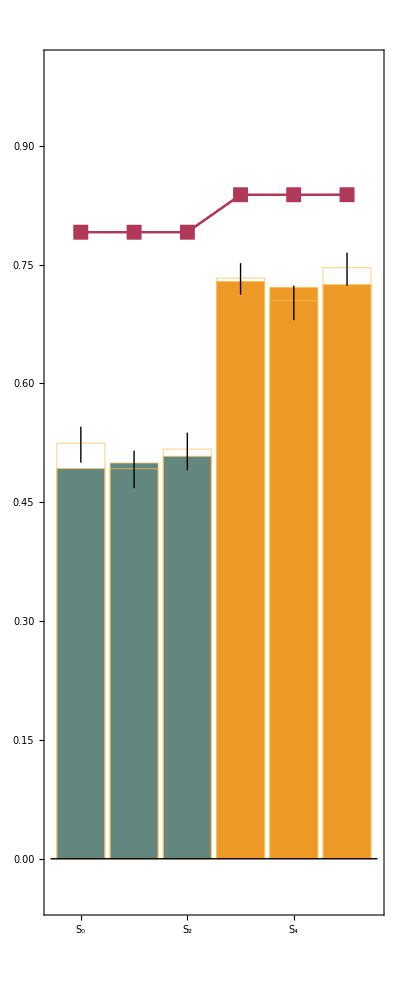
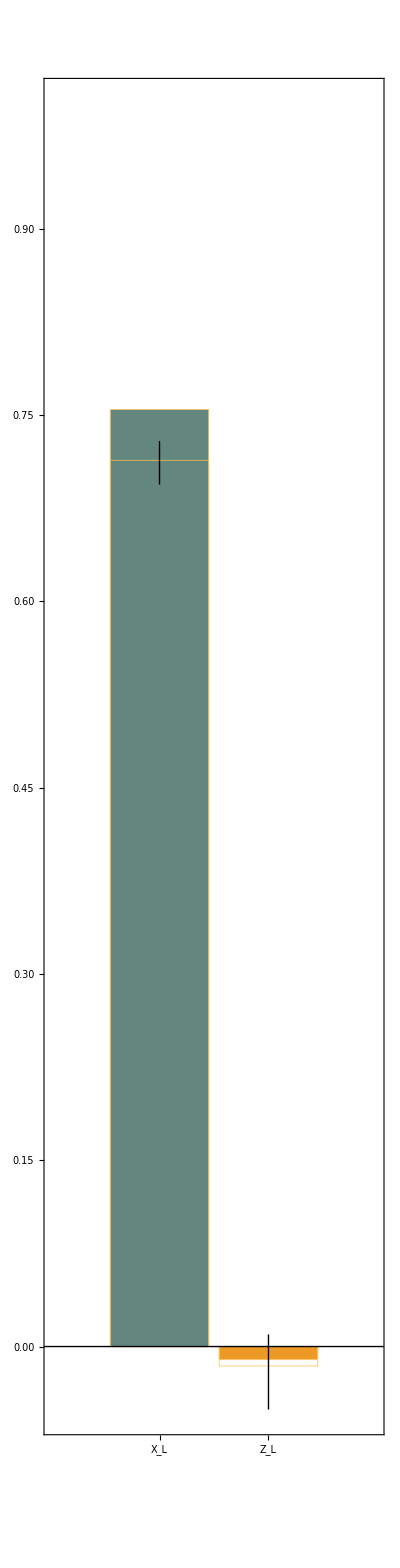
{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 8: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

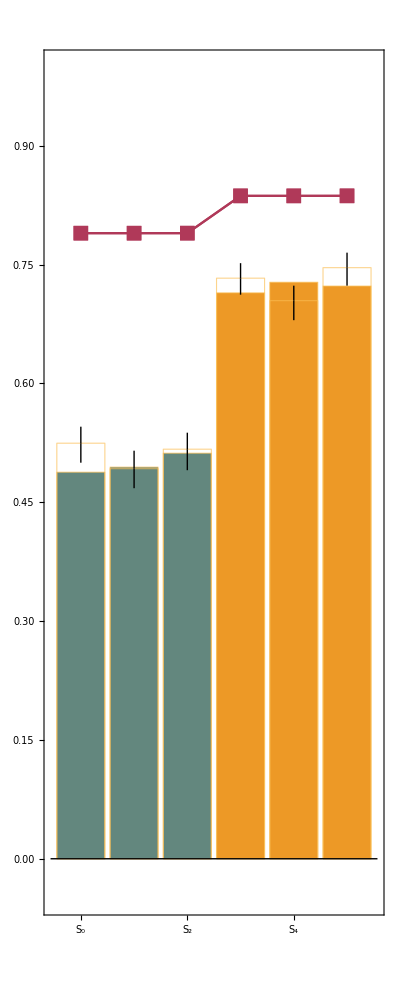
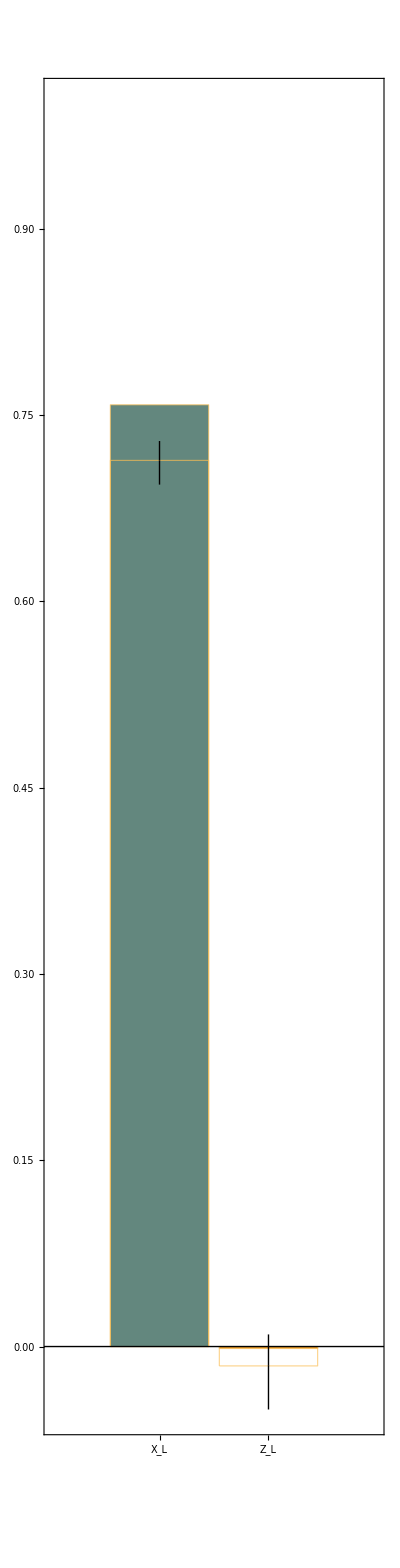
{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 9: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

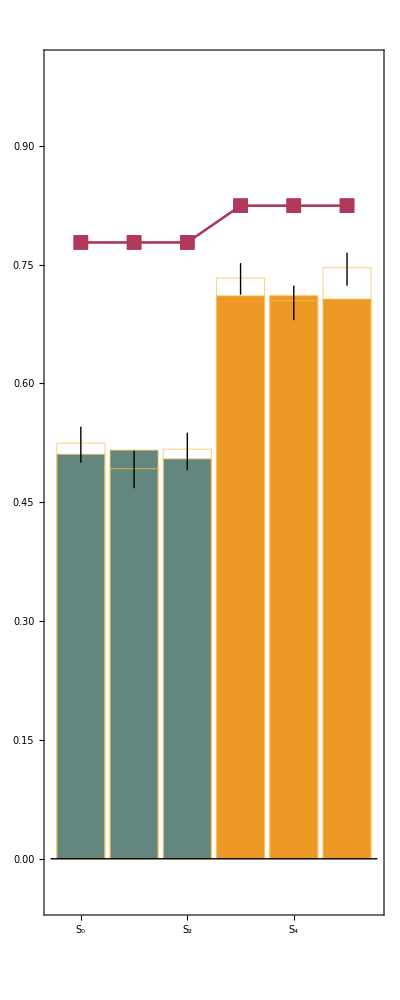
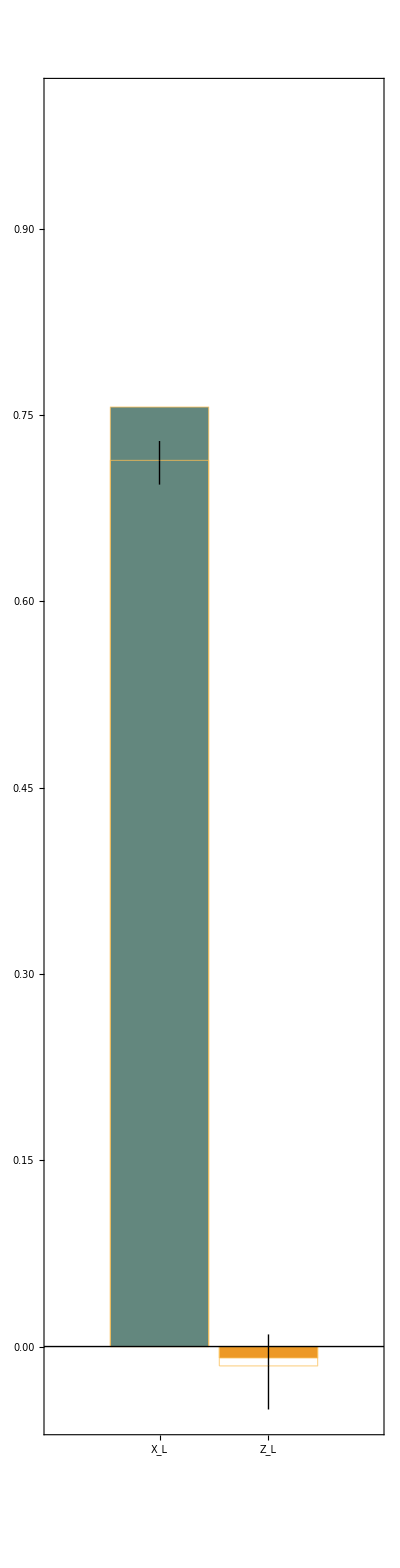
{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 10: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

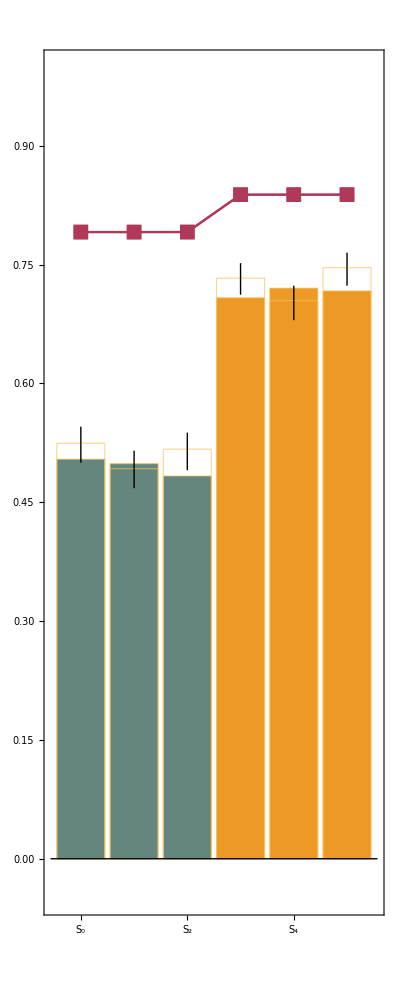
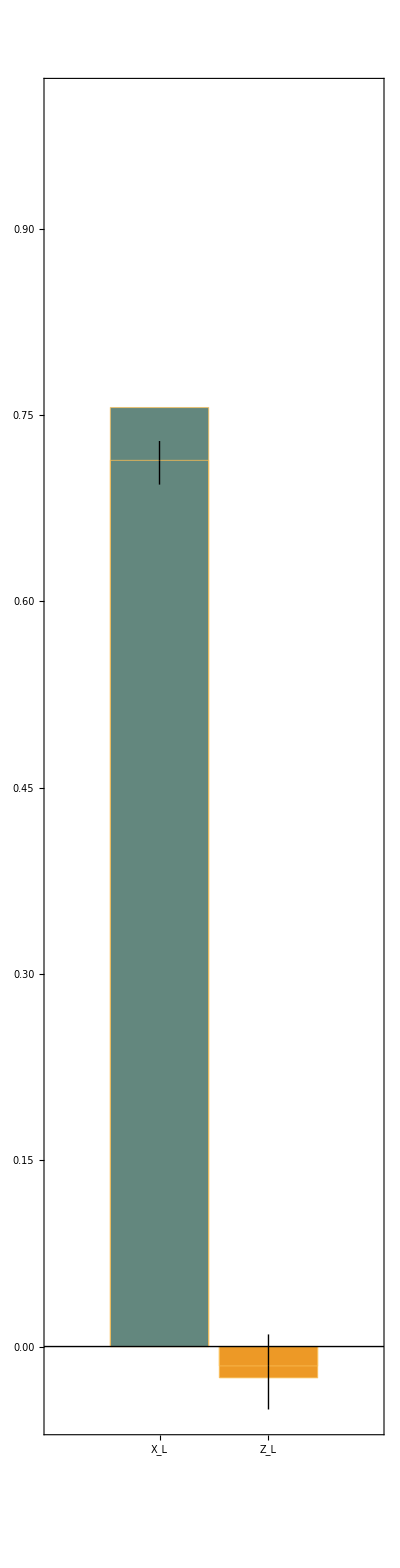
{-Graphics--Graphics-,<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 11: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

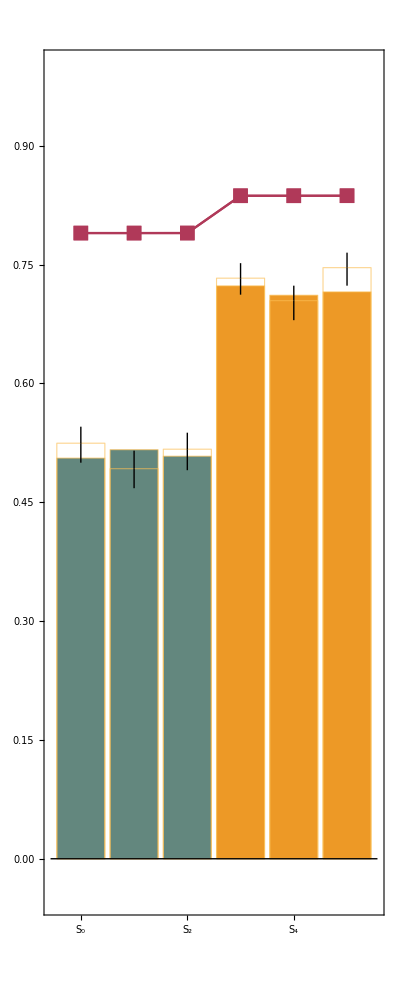
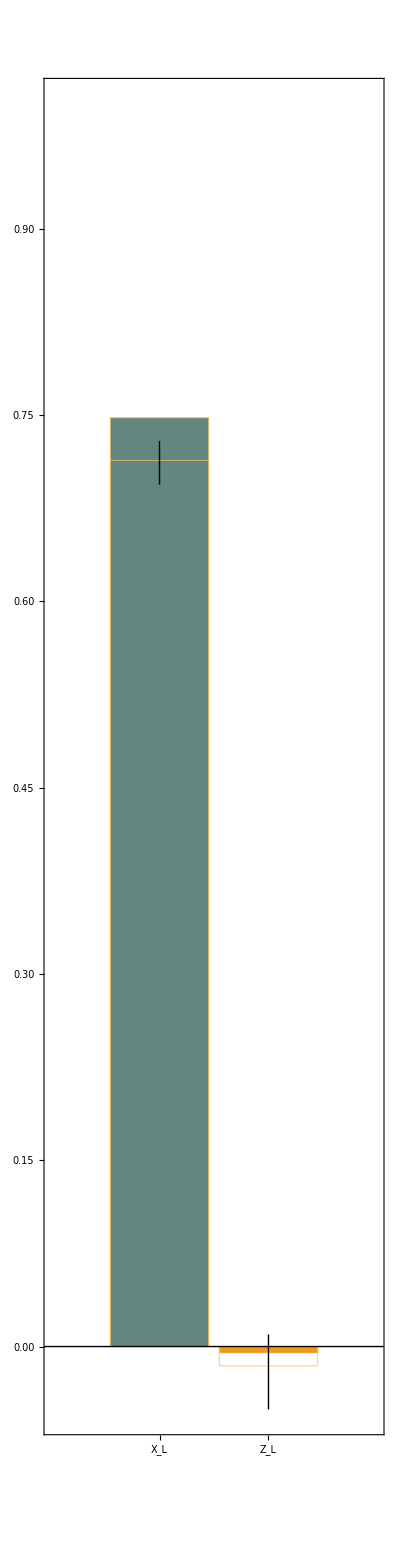
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 12: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

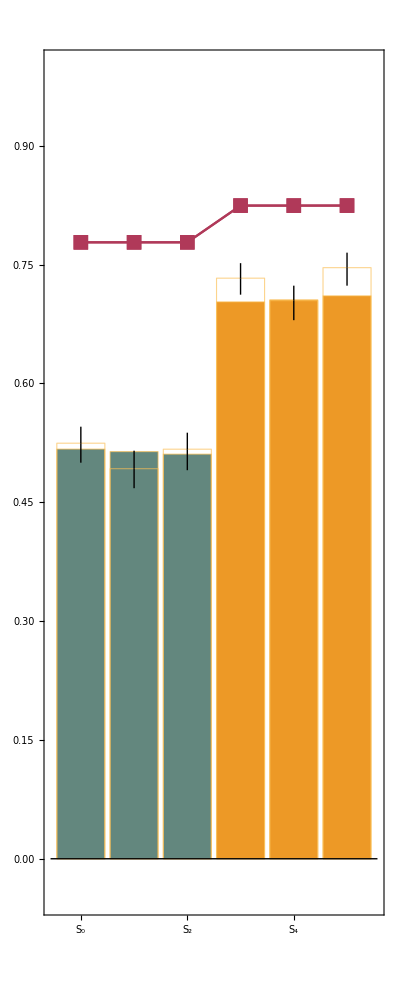
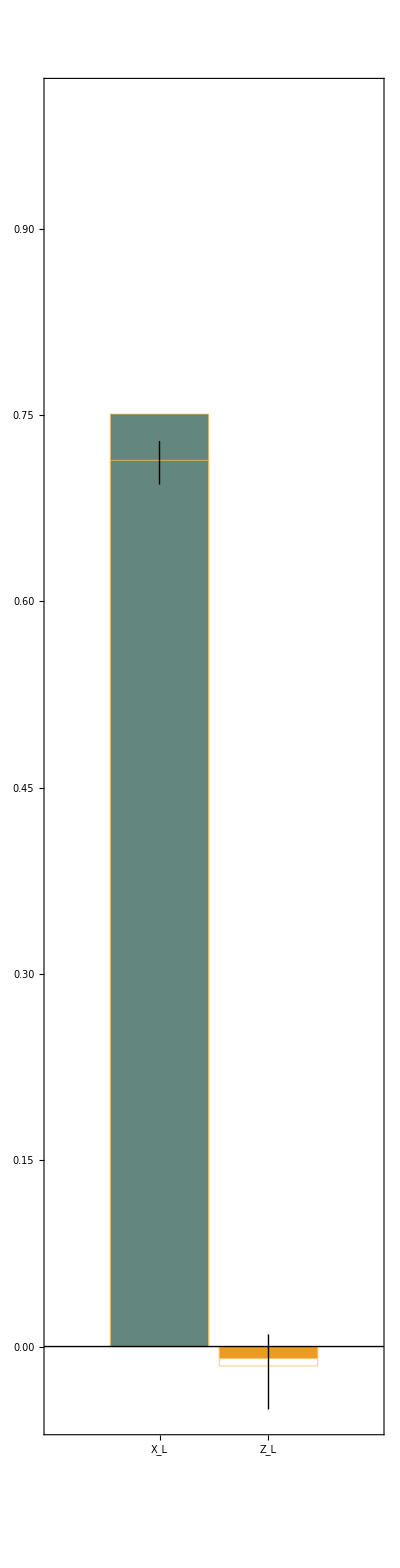
{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 13: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

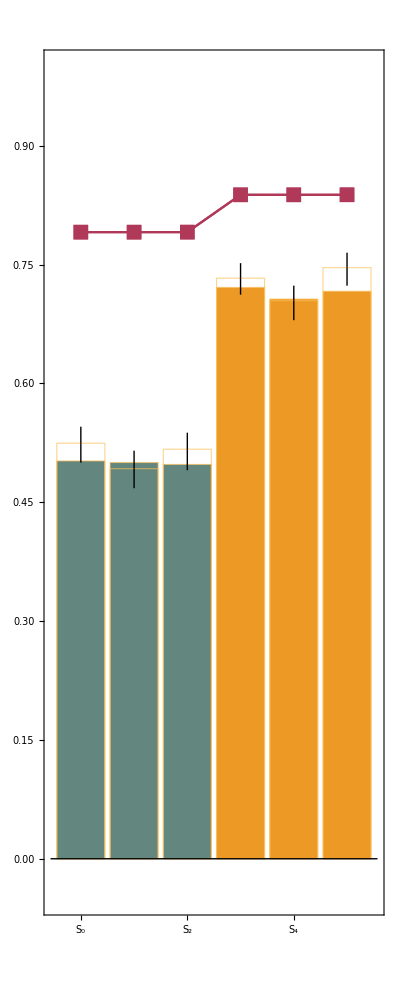
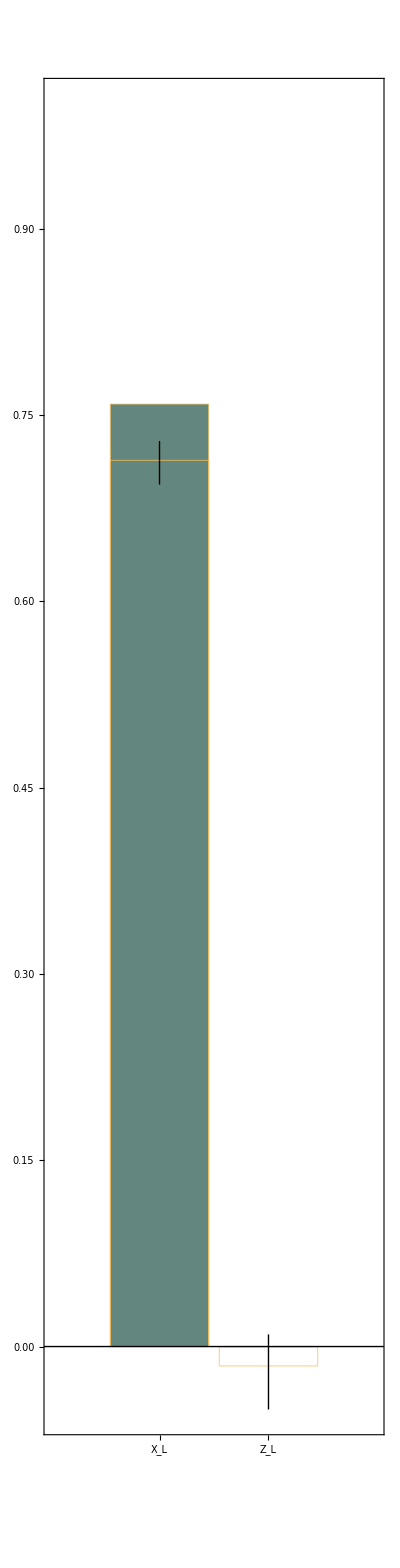
{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 14: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

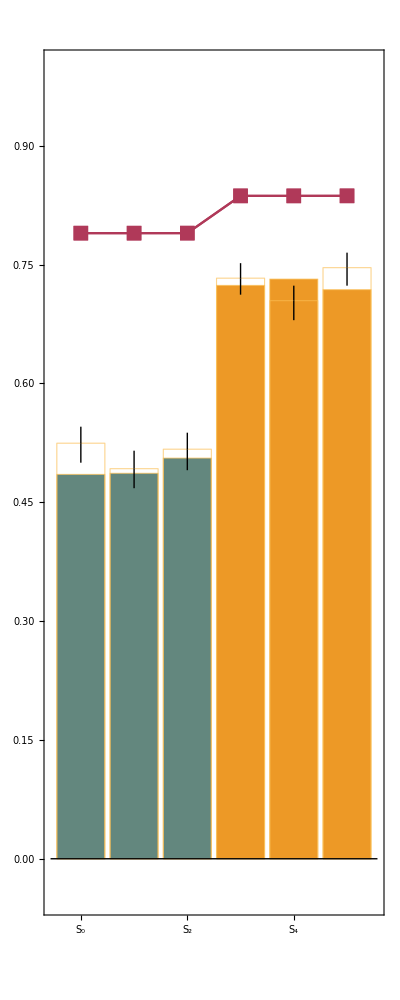
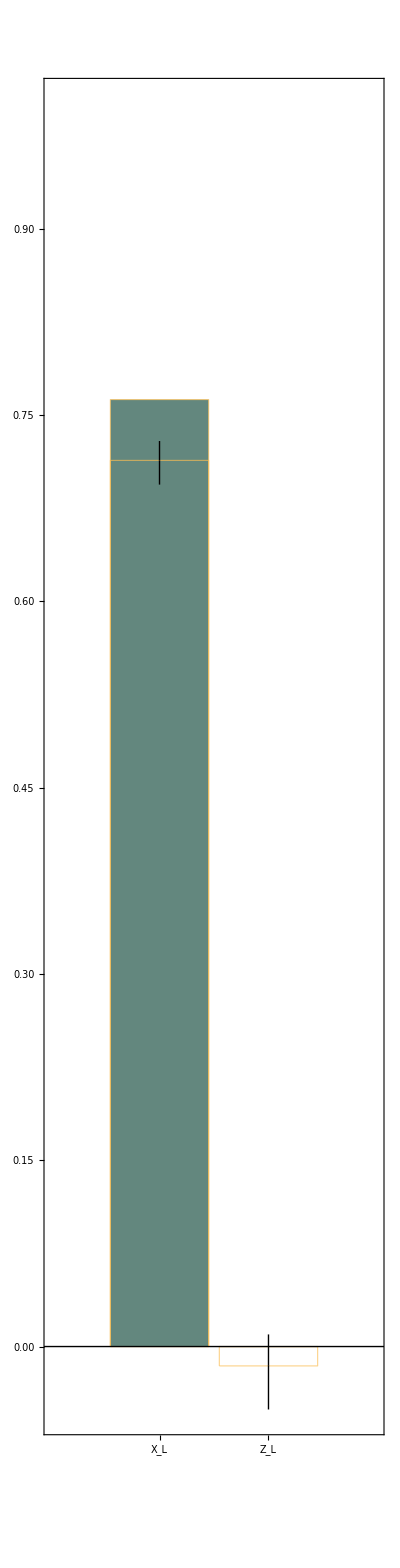
{-Graphics--Graphics-,<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 15: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

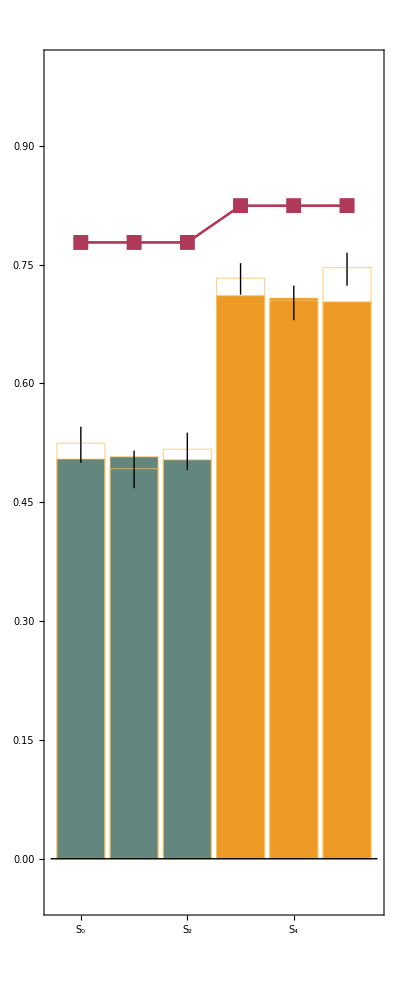
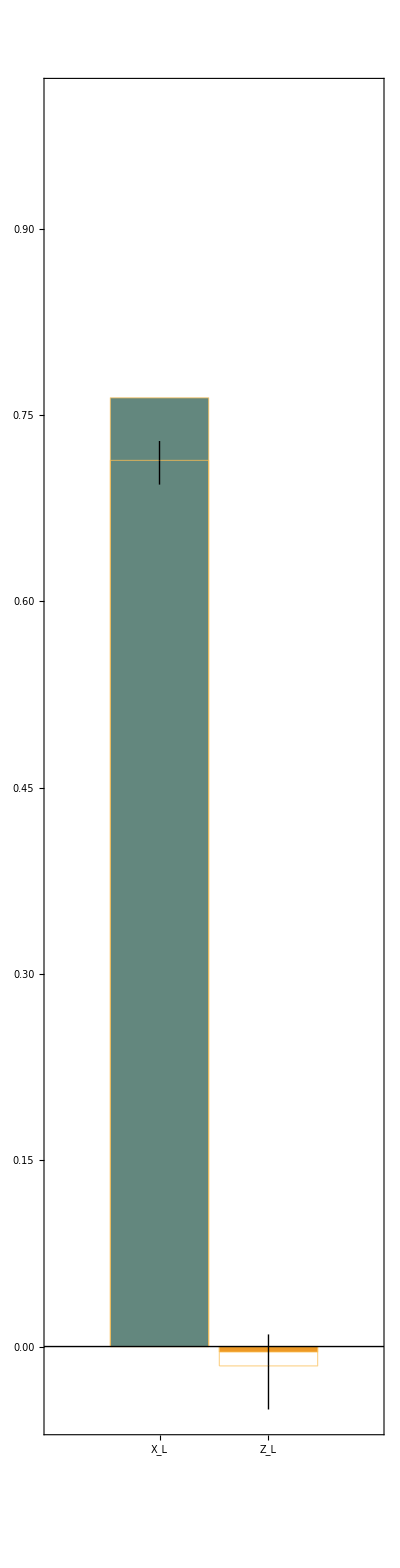
{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 16: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

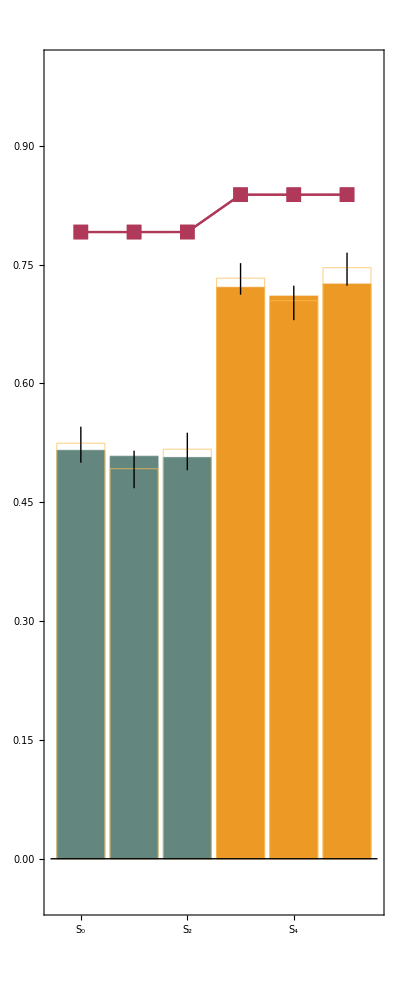
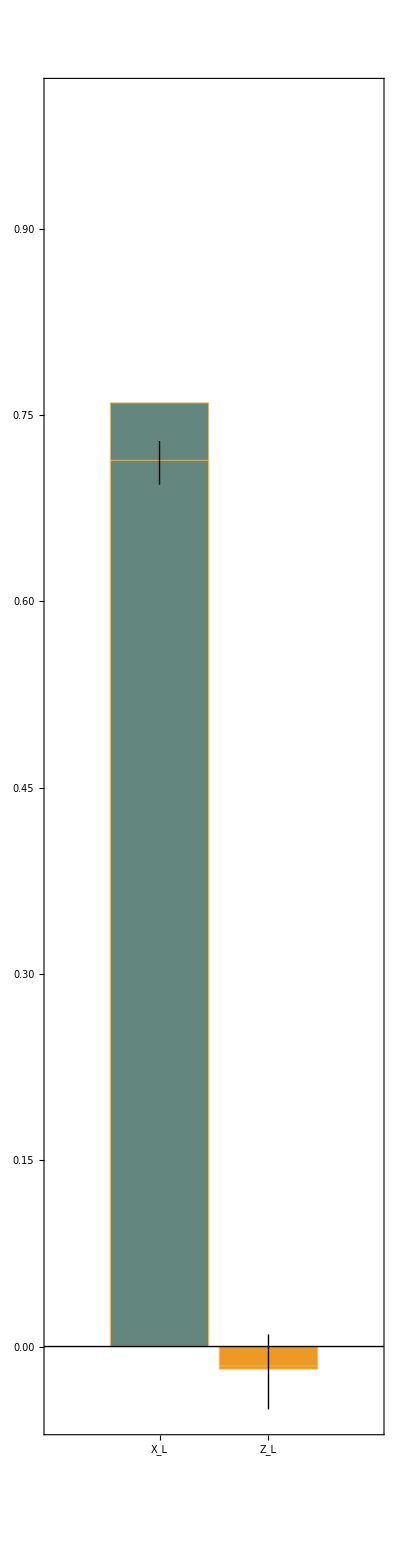
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 17: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

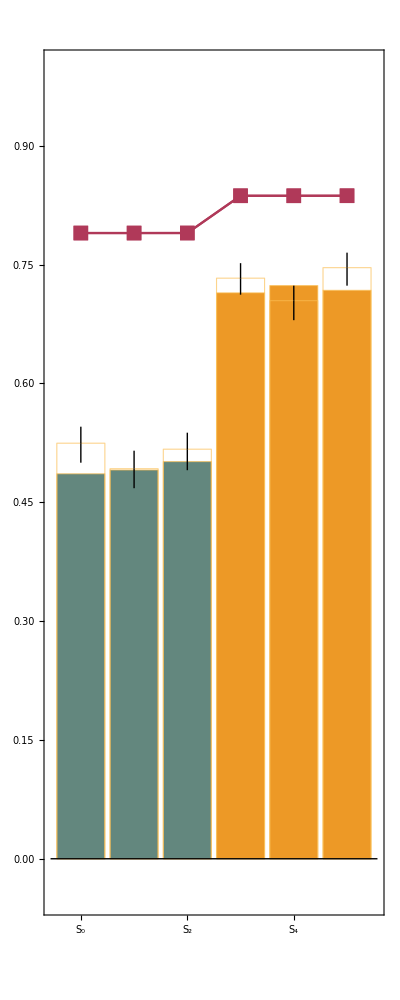
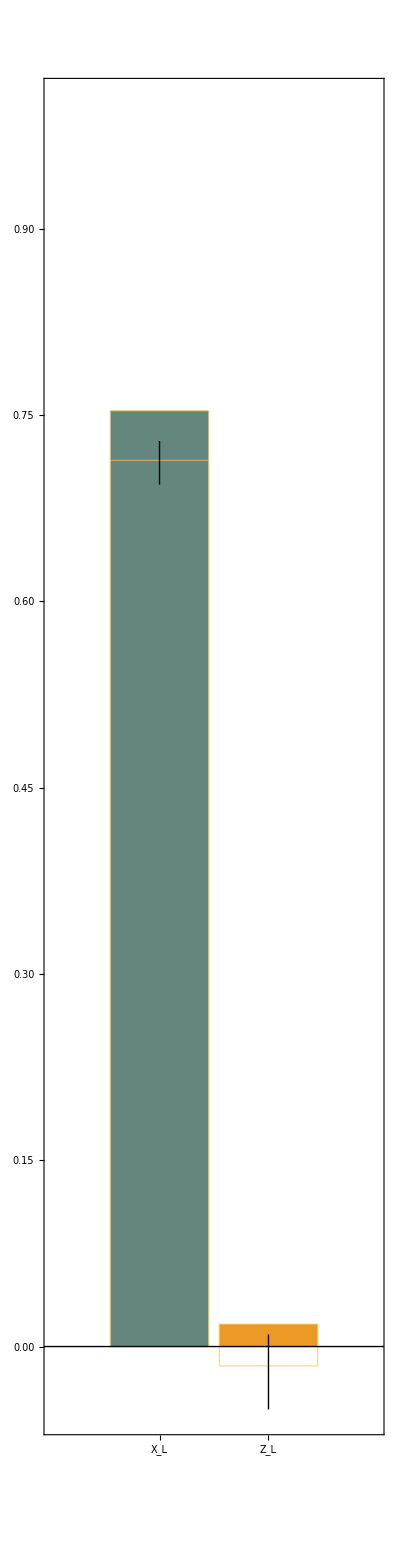
{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 18: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

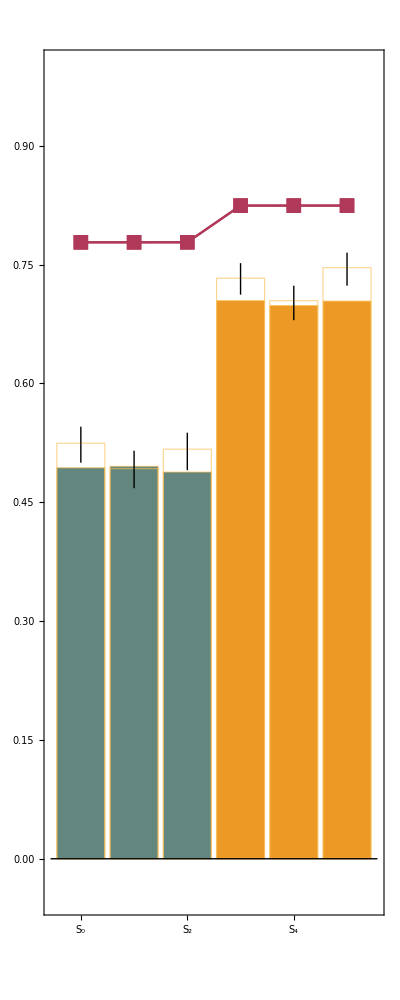
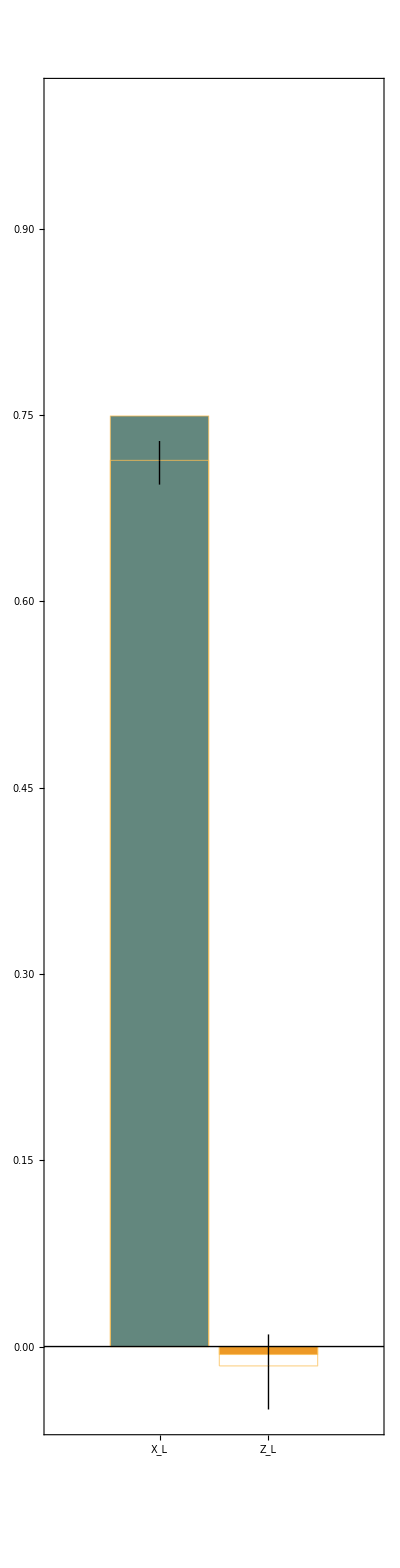
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 19: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

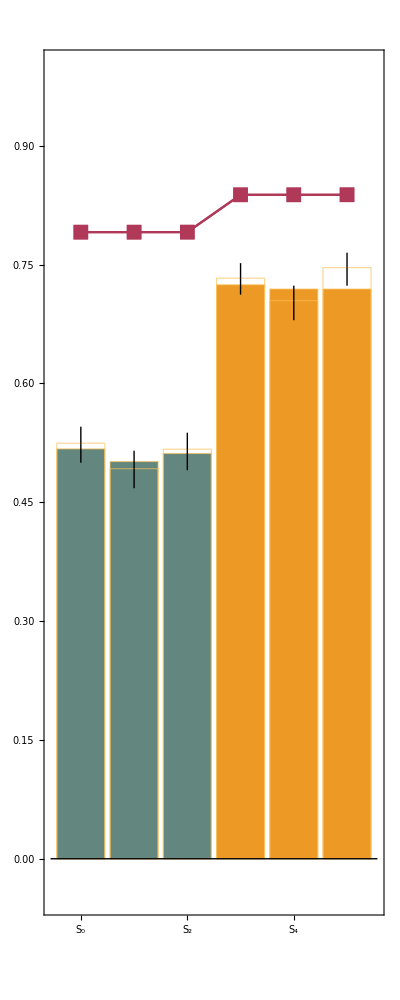
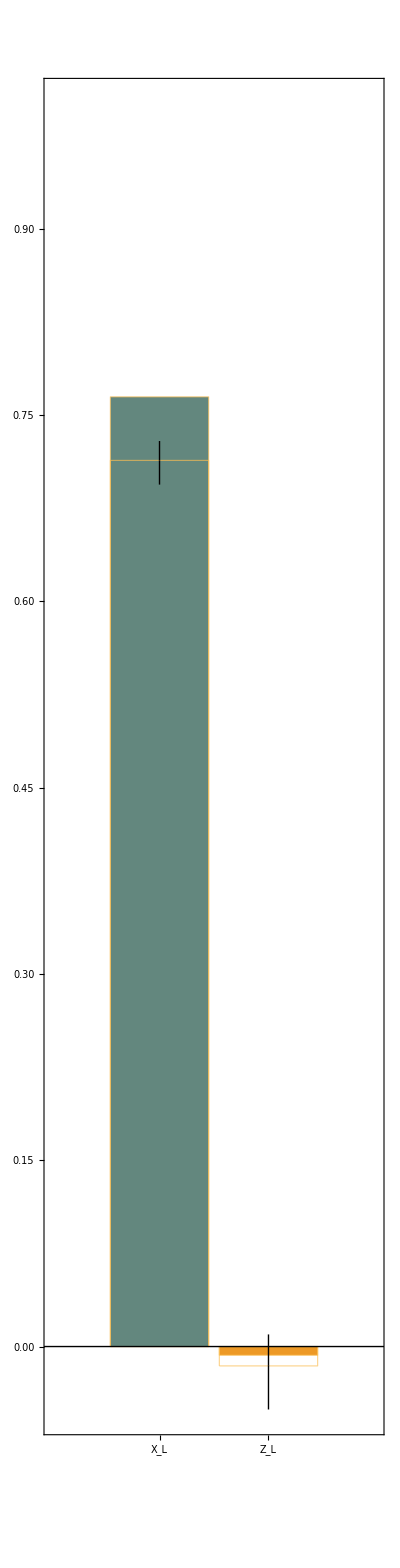
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 20: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

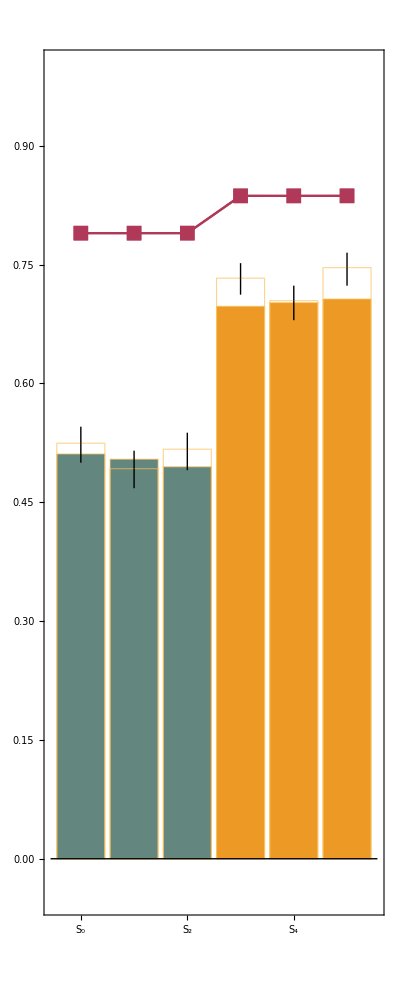
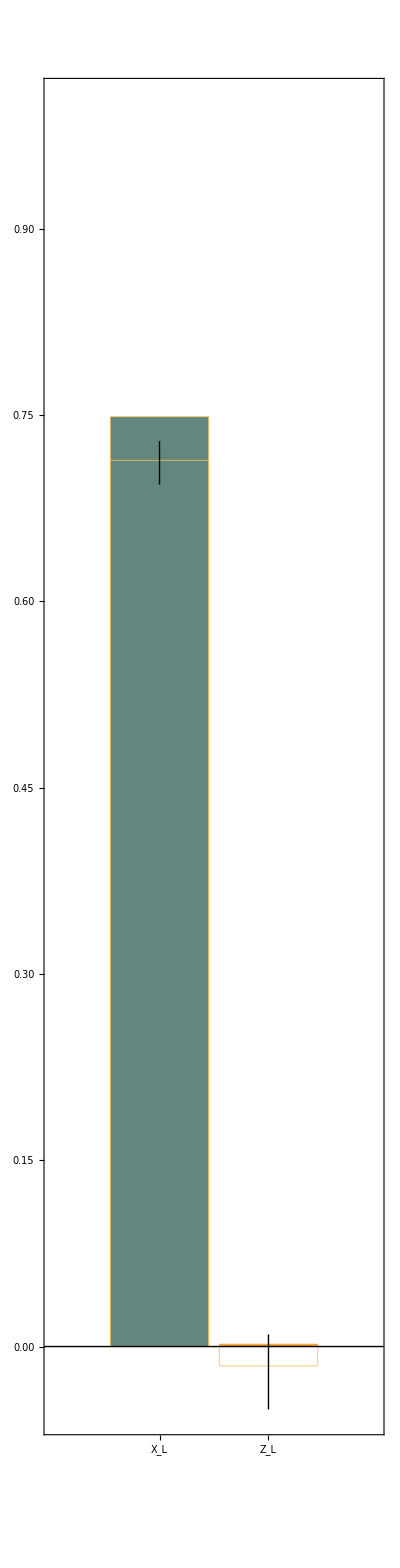
{-Graphics--Graphics-,<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 21: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

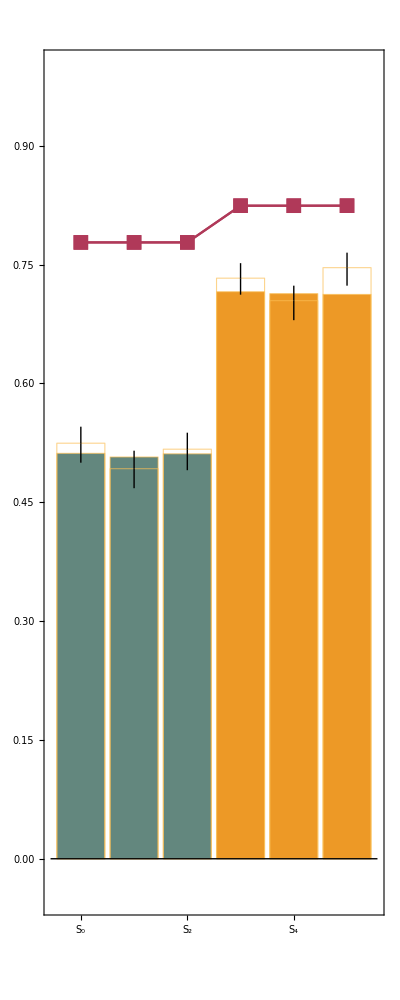
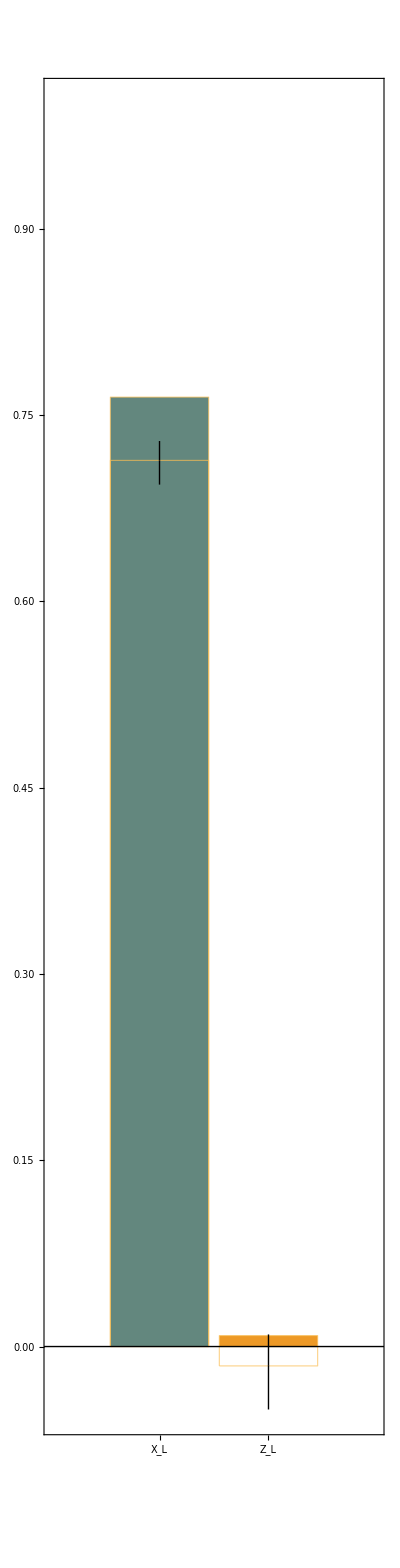
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 22: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

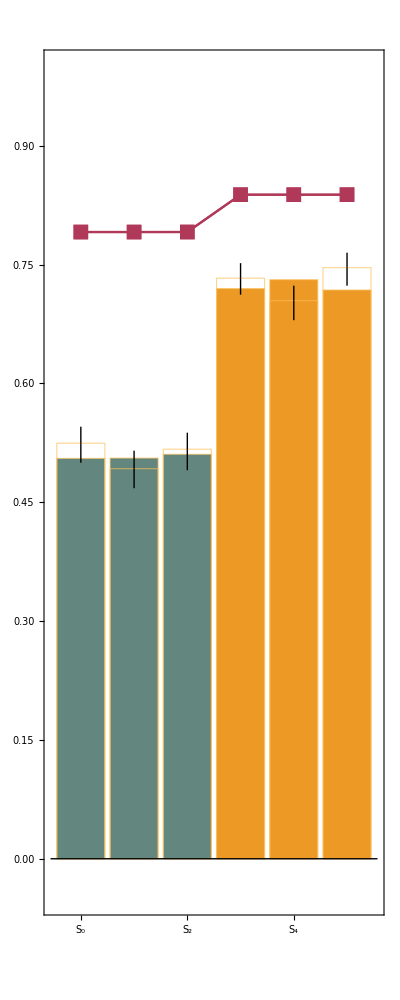
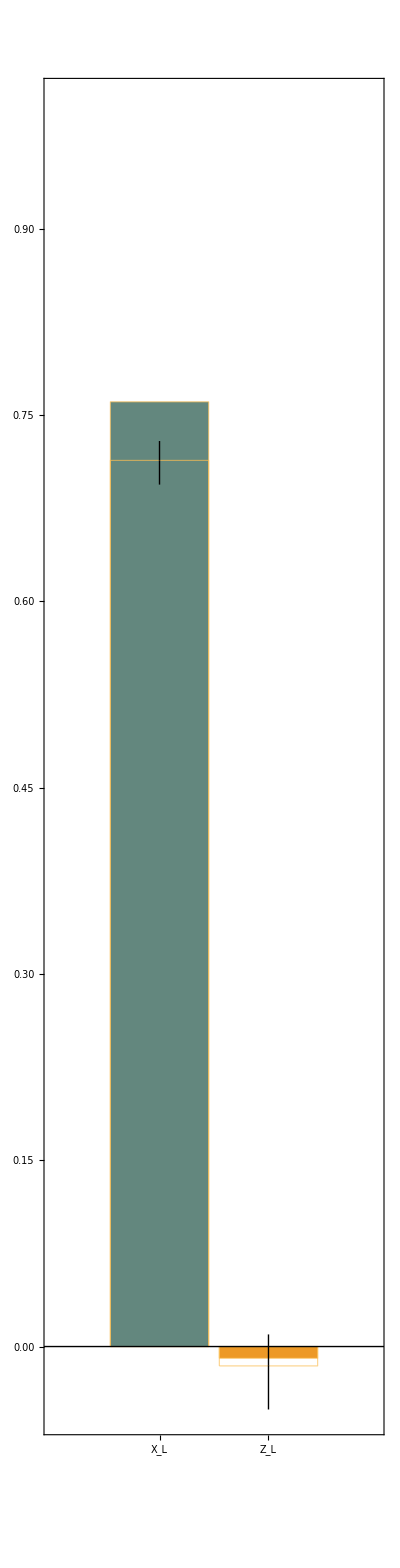
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 23: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

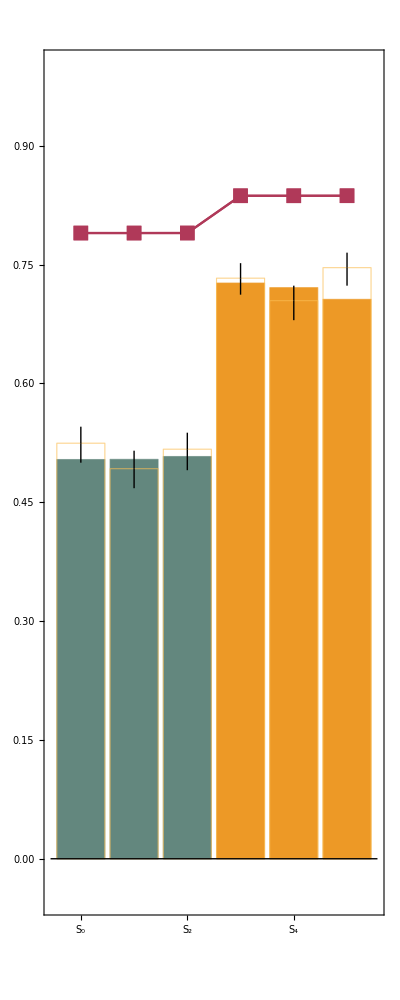
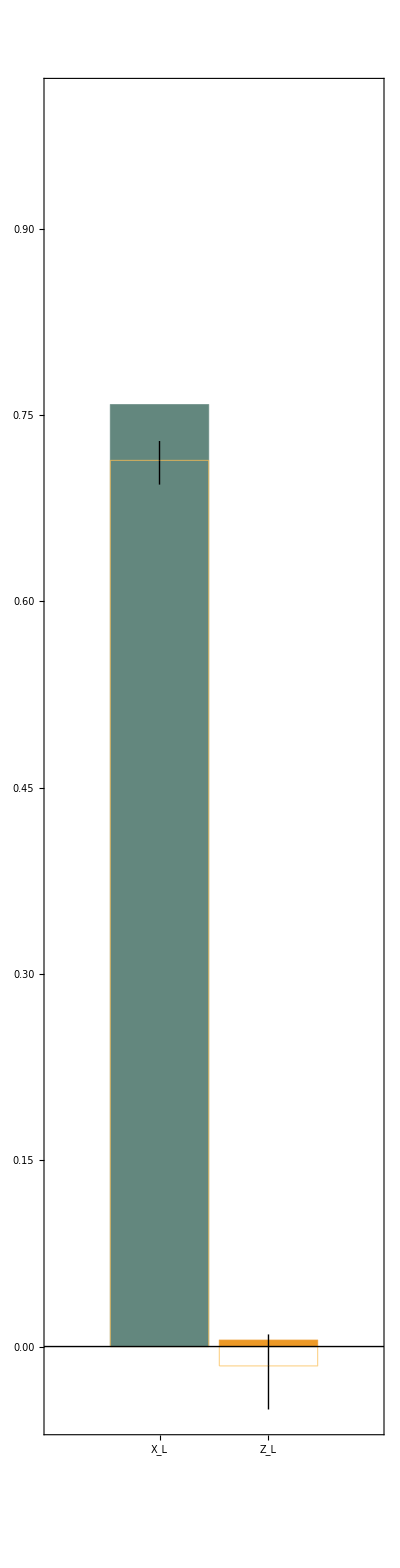
{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 24: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

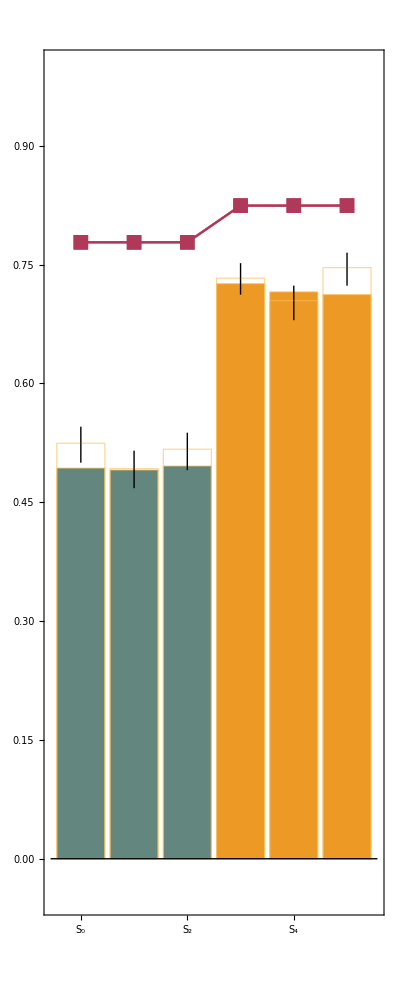
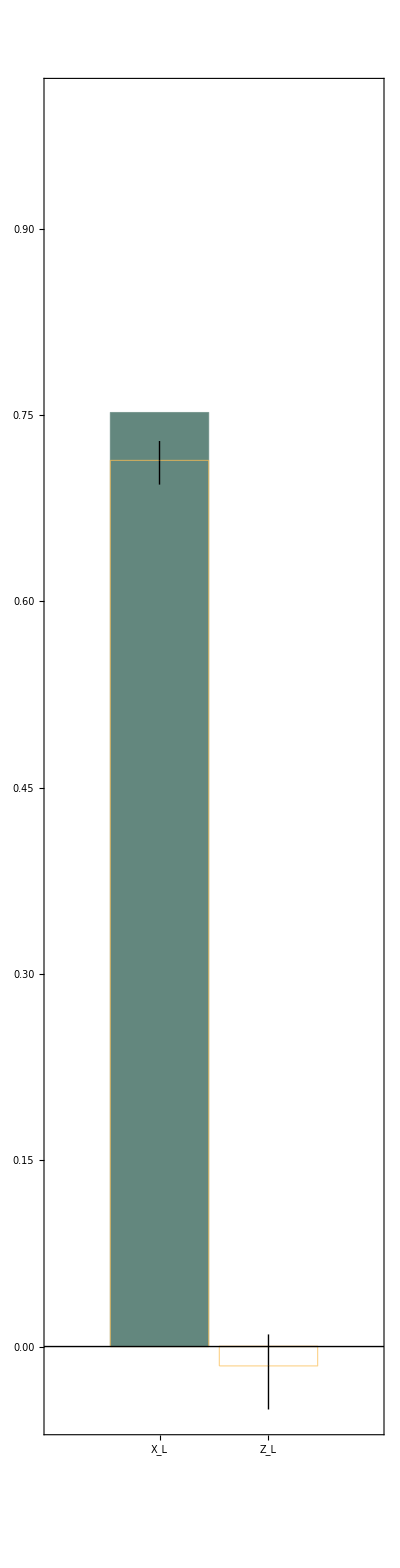
{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 25: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

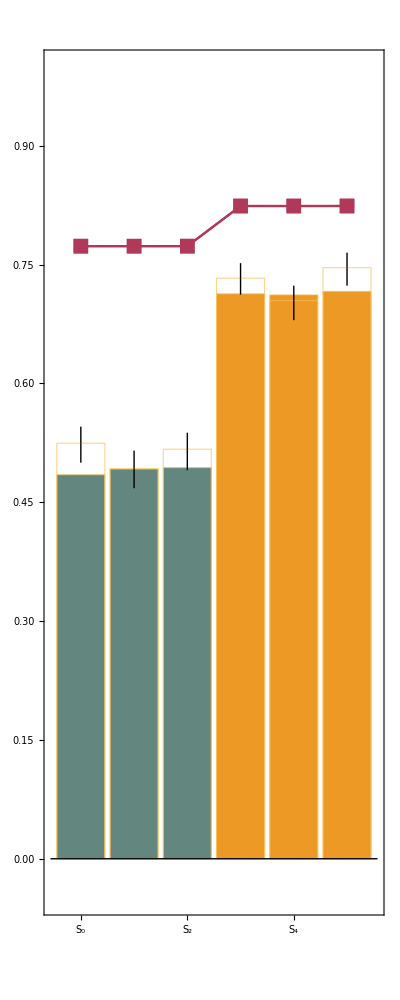
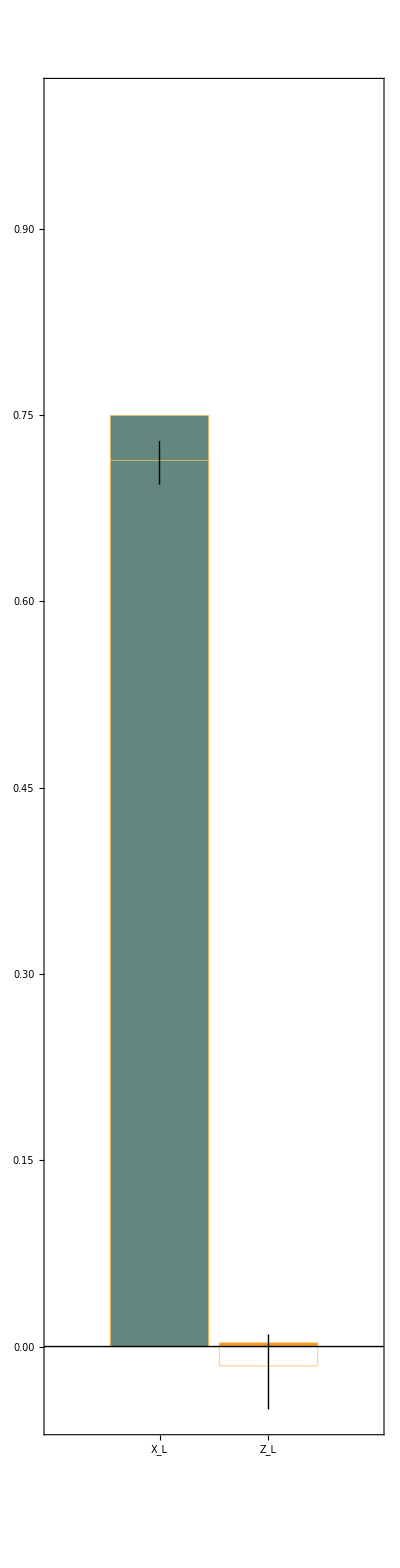
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 26: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

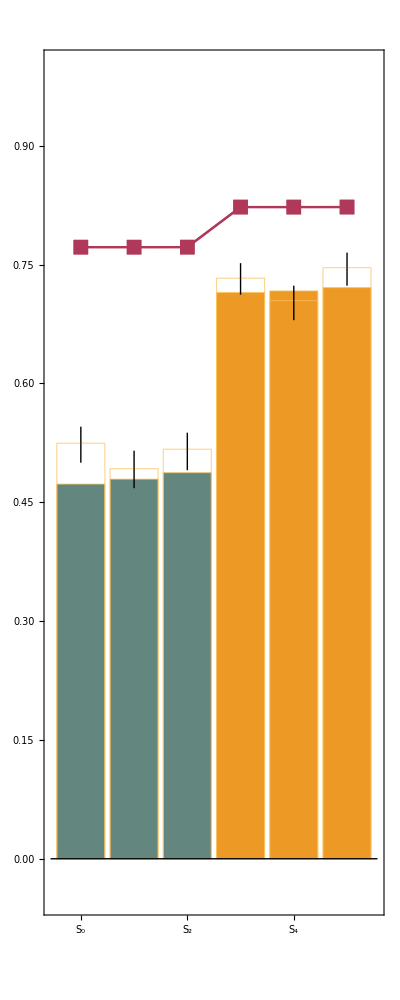
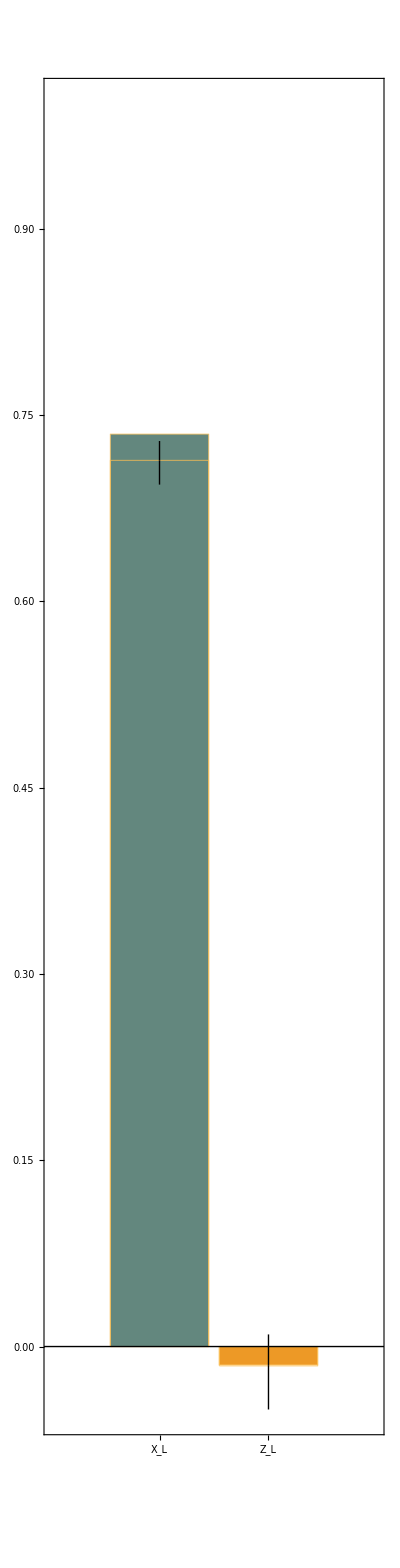
{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 27: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

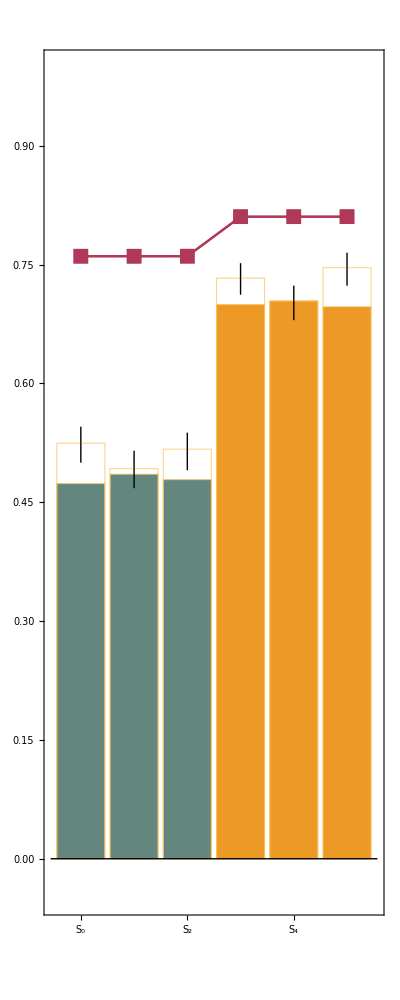
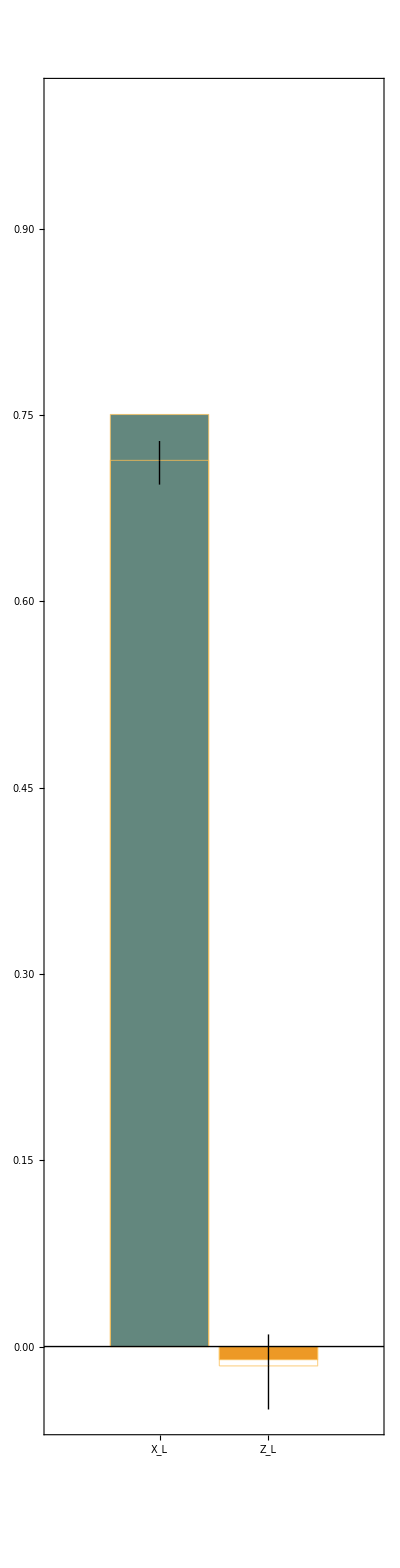
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 28: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

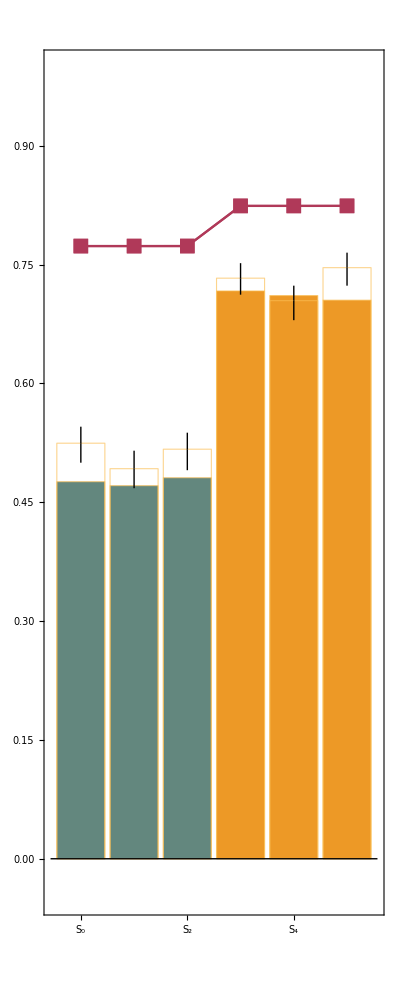
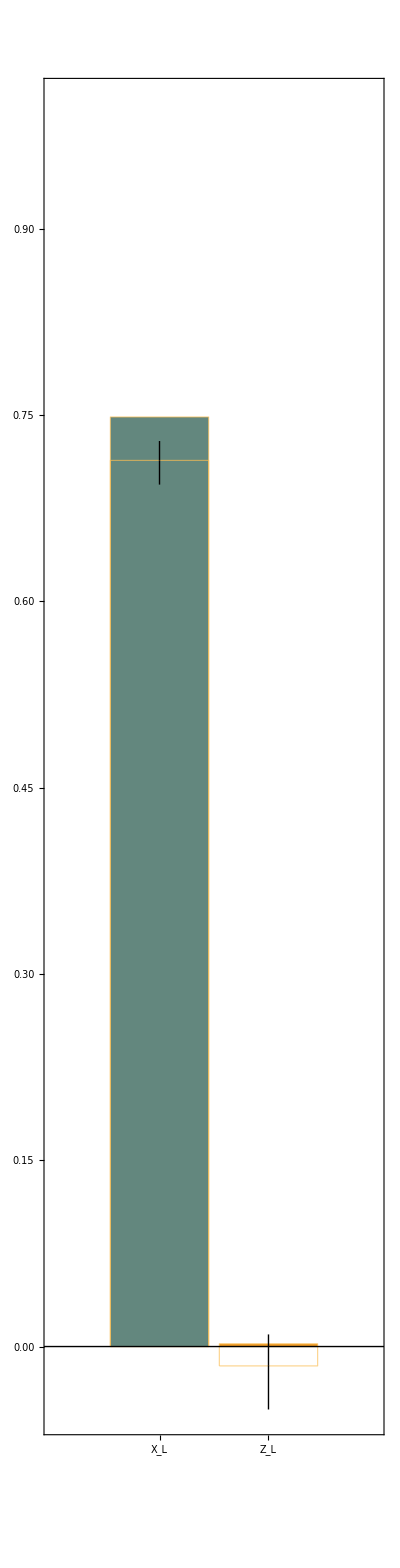
{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 29: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

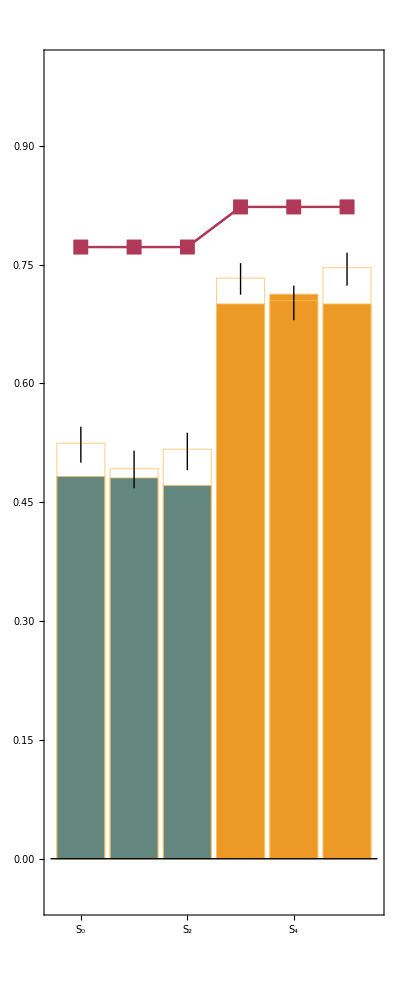
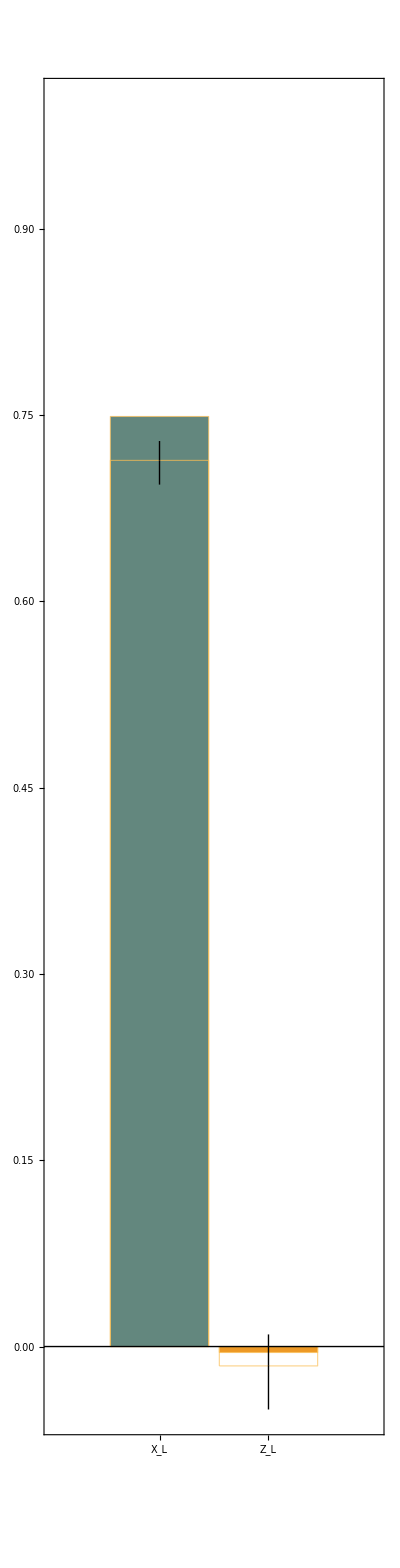
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 30: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

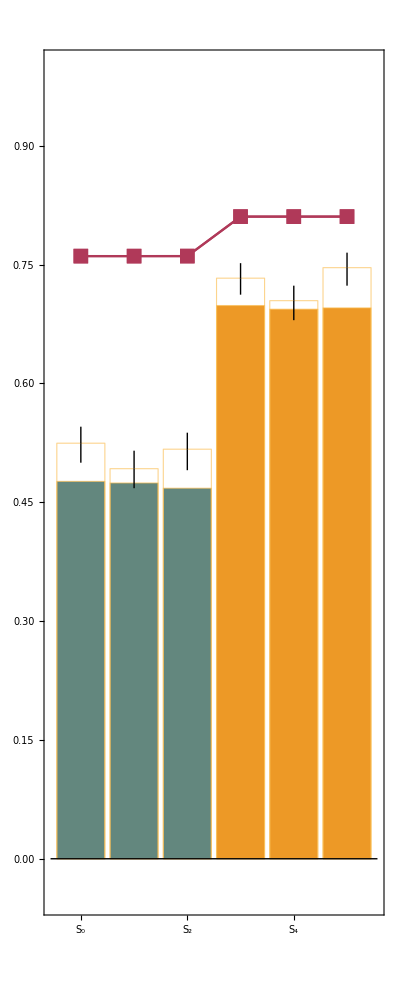
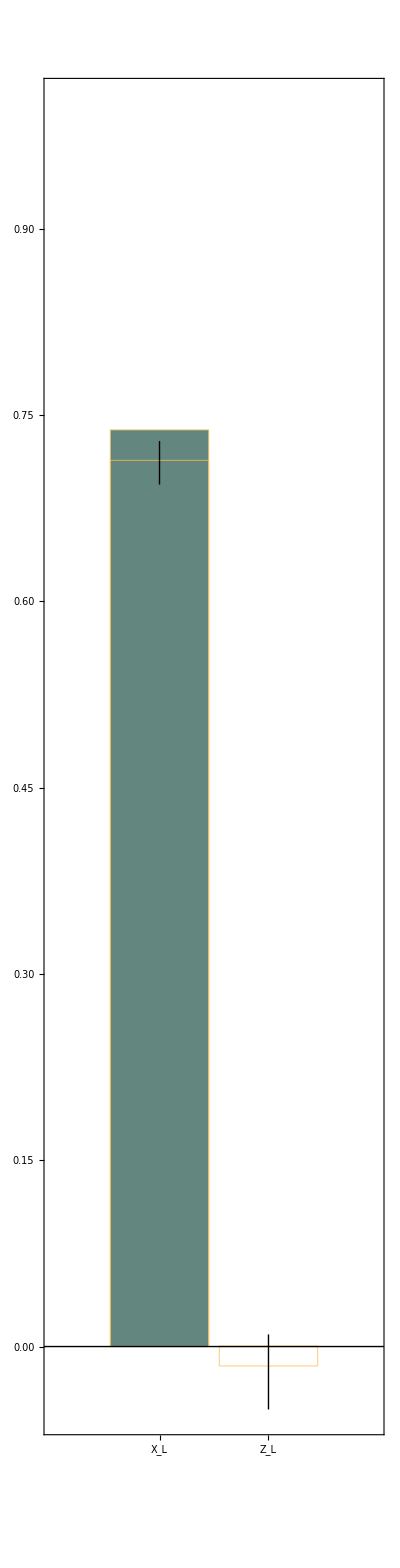
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 31: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

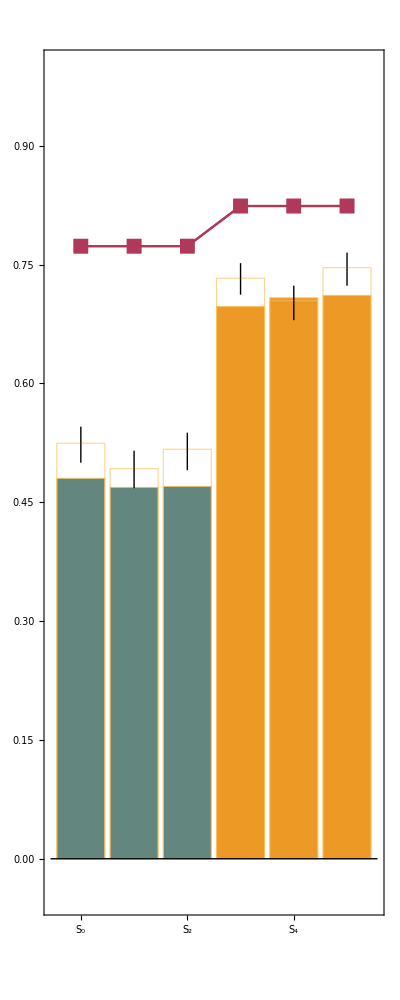
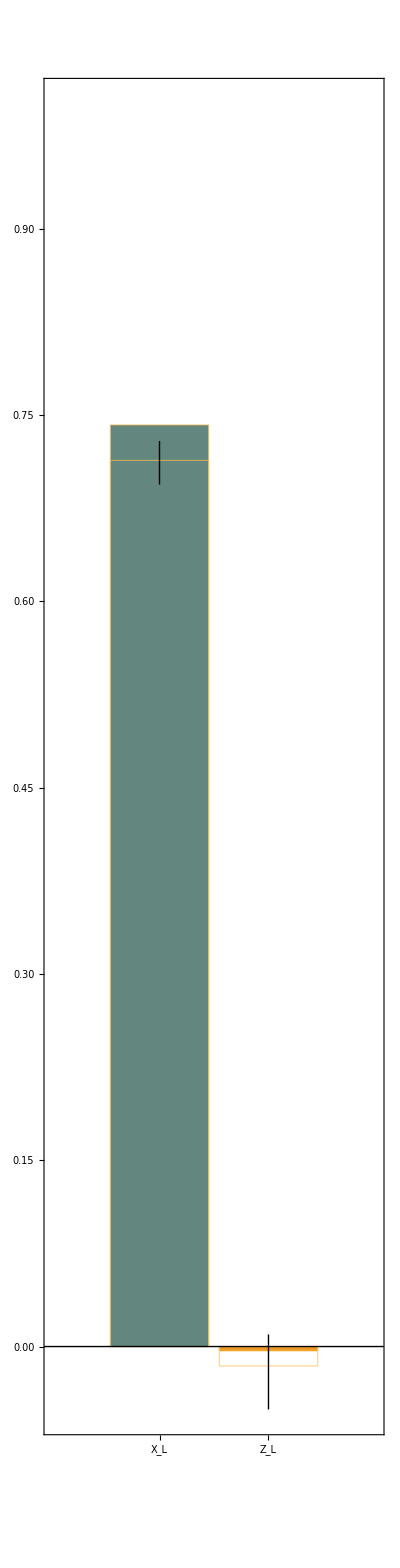
{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 32: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

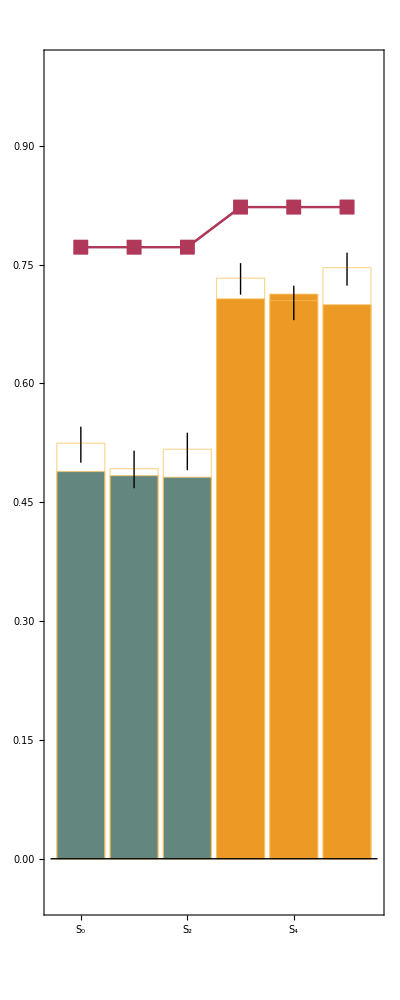
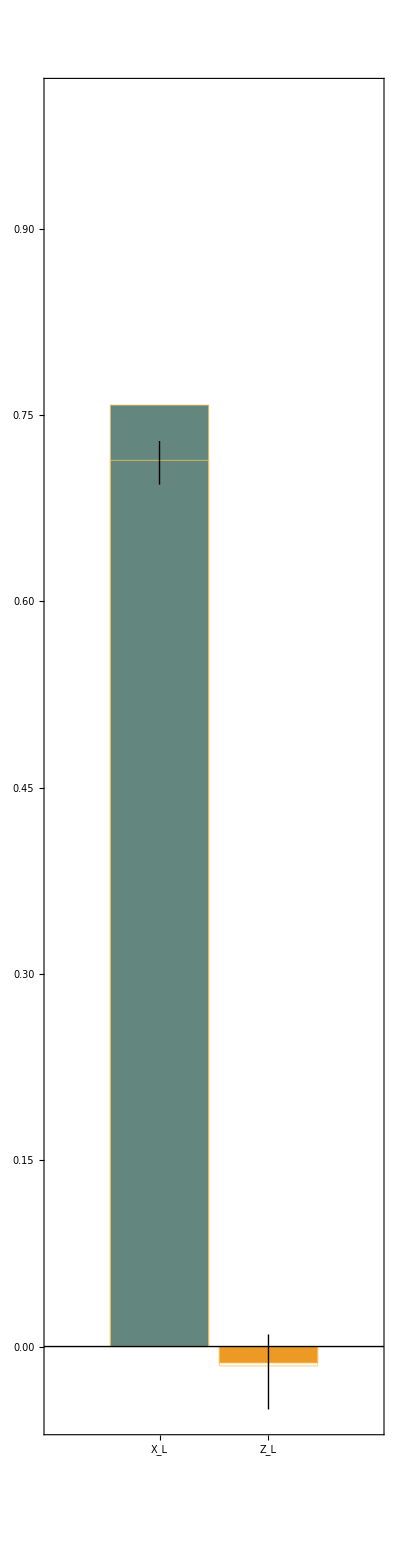
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 33: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

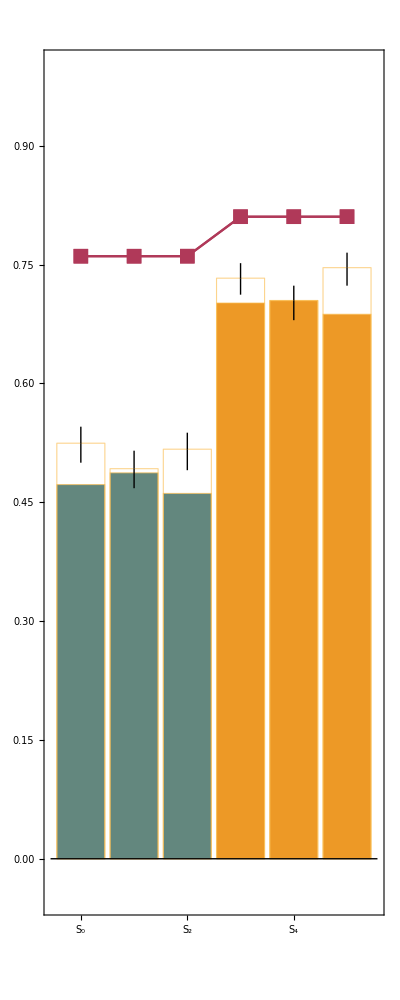
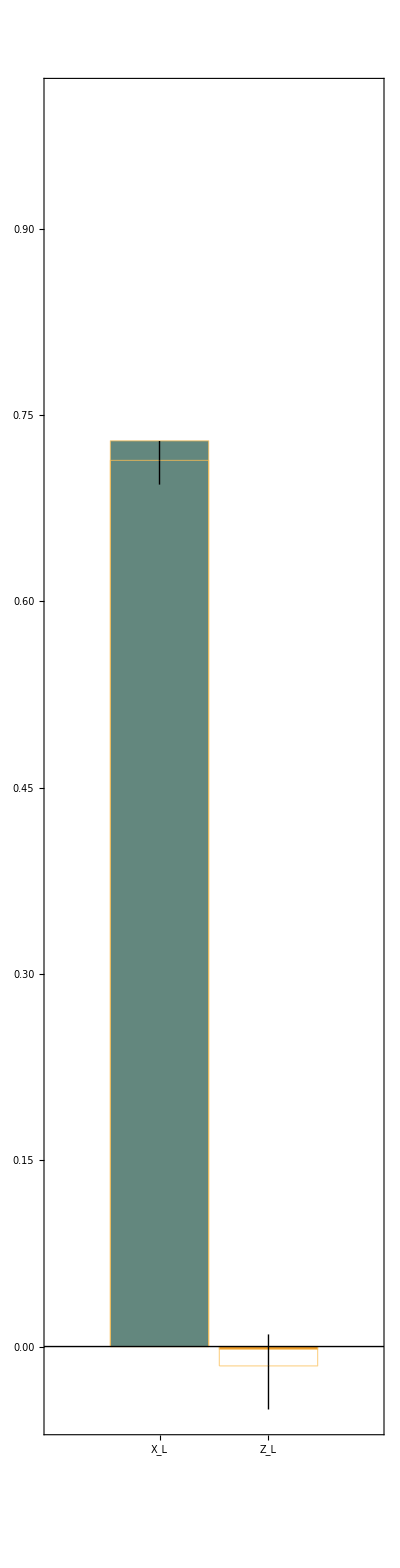
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 34: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

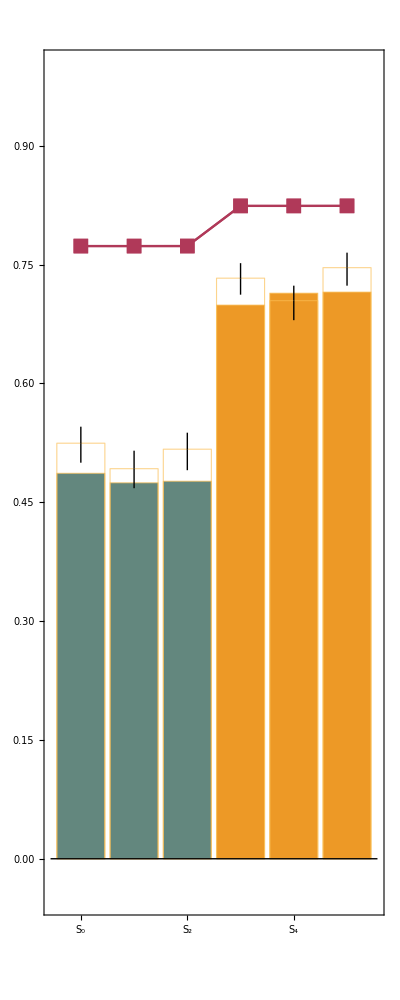
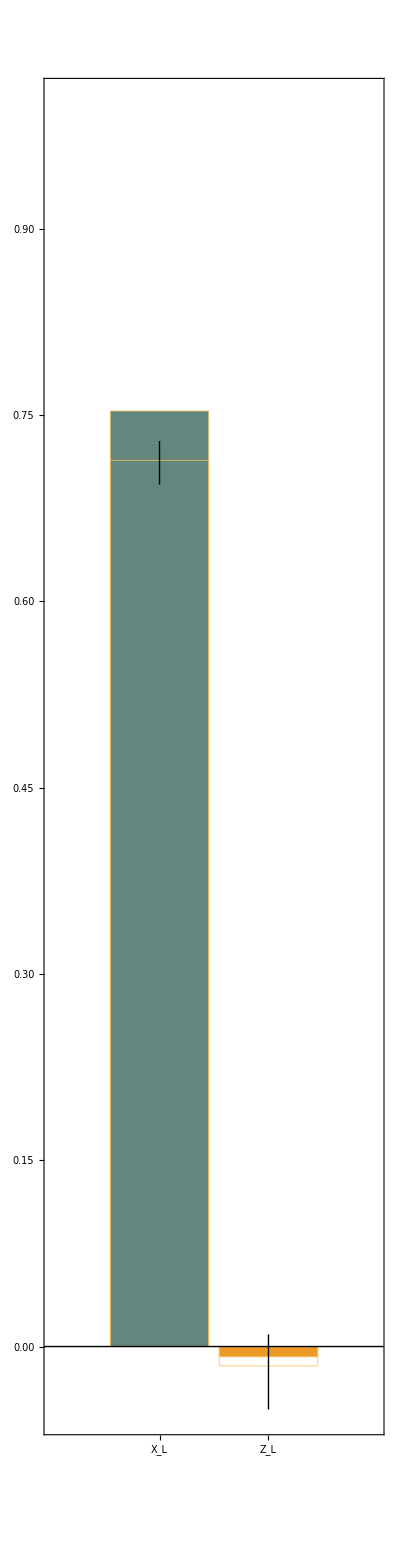
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 35: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

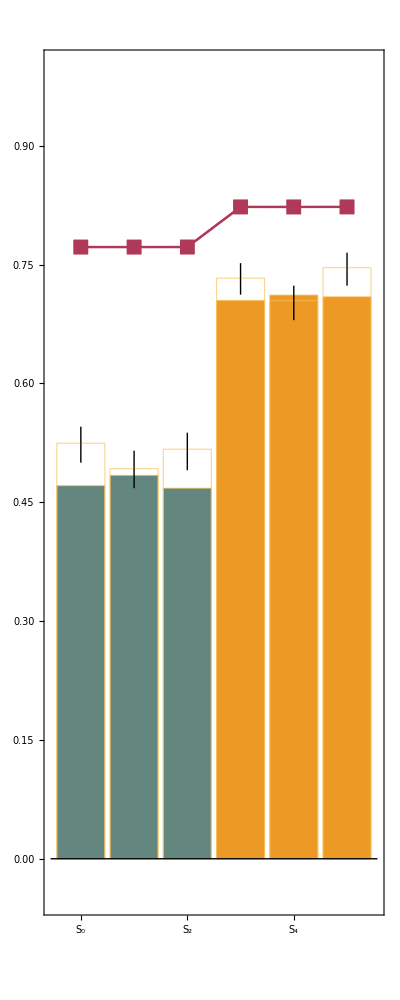
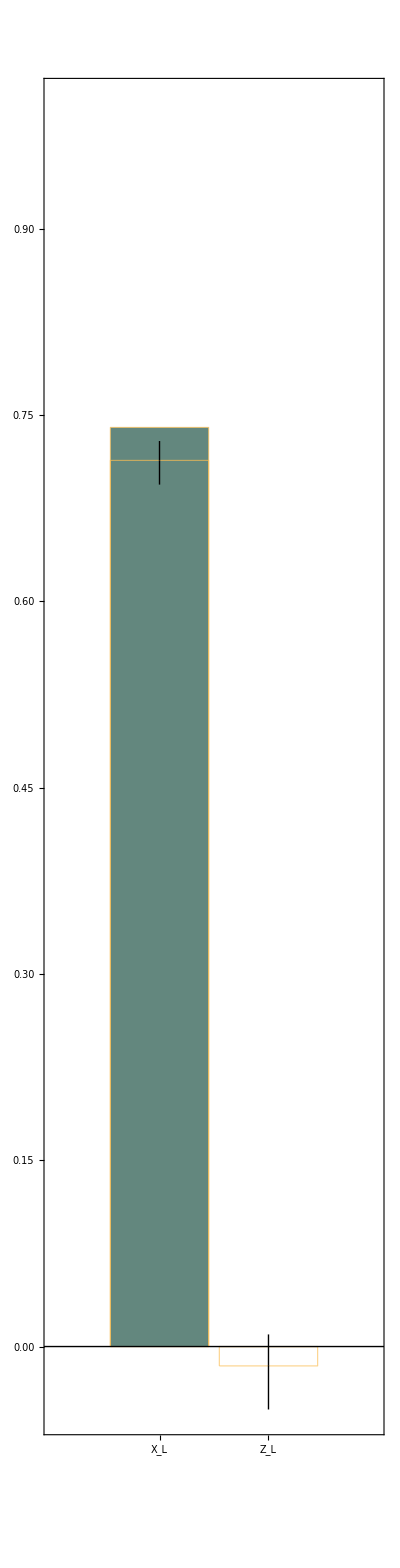
{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 36: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 37: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 38: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 39: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 40: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 41: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 42: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 43: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 44: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 45: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 46: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 47: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 48: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 1: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 2: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 3: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 4: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 5: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 6: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 7: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 8: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 9: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 10: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 11: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 12: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 13: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 14: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 15: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 16: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 17: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 18: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 19: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 20: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 21: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 22: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 23: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 24: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 25: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 26: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 27: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 28: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 29: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 30: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 31: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 32: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 33: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 34: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 35: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 36: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 37: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 38: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 39: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 40: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 41: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 42: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 43: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 44: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 45: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 46: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2}

{-Graphics--Graphics-,<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 47: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8}

{-Graphics--Graphics-,<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 48: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64}

{-Graphics--Graphics-,<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

```mathematica
nshots=10000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[2]],Values@out[[3]]],Break[]]
]

nshots=5000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[2]],Values@out[[3]]],Break[]]
]
```

```mathematica
(* try some combinations of error parameters *)
bfrot=Flatten@Table[<|10->i,01->j|>,{i,{0.1,0.12,0.11}},{j,{0.0001,0.00008,0.0001}}];
probleakcz=Flatten@Table[<|10->i,11->j|>,{i,{0.1,0.12,0.11}},{j,{0.0001,0.0005,0.00008}}];
heat={2,8,64};
fidmeas={0.975,0.97,0.98,0.965};
options=Flatten[Table[{ProbBFRot->i,ProbLeakCZ->k,HeatFactor->l,FidMeas->m},{i,bfrot},{k,probleakcz},{l,heat},{m,fidmeas}],3];
Length@options
```

972

```mathematica
nshots=10000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[2]],Values@out[[3]]],Break[]]
];
```

```mathematica
steane7<<steane7.mx;
```

```mathematica
truth=Table[
out=Values@steaneResults[res,steane,lsteane][[{"benchmarkstab","benchmarklogic"}]];
Flatten@{Values@out[[1]],Values@out[[2]]}
,{res,steane7}];
```

```mathematica
truth[[1]]
```

{True,False,True,False,True,False,False,True}

```mathematica
truecount=Count[#,True]&/@truth;
```

```mathematica
best=Flatten@Position[truecount, x_/; x>=7]
```

{323,1115,1191,1223,1235,1303,1315,1343,1347,1355,1419}

```mathematica
Table[
out=Values@steaneResults[steane7[[i]],steane,lsteane][[{"chart","benchmarkstab","benchmarklogic"}]];
out
,{i,best}]
```

{{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>},{-Graphics--Graphics-,<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}}

```mathematica
nshots=2000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[1]],Values@out[[2]]],Break[]]
]
```

Trial 1: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 2: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 3: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 4: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 5: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 6: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 7: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 8: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 9: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 10: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 11: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 12: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 13: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 14: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 15: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 16: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 17: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 18: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 19: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 20: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 21: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 22: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 23: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 24: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 25: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 26: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 27: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 28: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 29: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 30: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 31: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 32: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 33: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 34: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 35: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 36: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 37: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 38: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 39: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 40: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 41: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 42: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 43: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 44: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 45: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 46: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 47: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 48: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 49: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 50: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 51: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 52: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 53: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 54: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 55: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 56: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 57: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 58: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 59: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 60: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 61: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 62: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 63: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 64: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 65: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 66: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 67: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 68: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 69: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 70: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 71: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 72: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 73: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 74: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 75: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 76: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 77: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 78: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 79: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 80: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 81: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 82: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 83: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 84: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 85: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 86: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 87: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 88: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 89: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 90: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 91: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 92: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 93: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 94: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 95: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 96: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 97: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 98: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 99: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 100: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 101: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 102: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 103: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 104: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 105: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 106: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 107: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 108: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 109: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 110: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 111: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 112: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 113: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 114: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 115: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 116: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 117: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 118: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 119: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 120: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 121: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 122: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 123: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 124: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 125: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 126: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 127: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 128: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 129: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 130: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 131: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 132: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 133: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 134: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 135: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 136: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 137: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 138: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 139: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 140: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 141: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 142: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 143: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 144: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 145: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 146: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 147: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 148: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 149: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 150: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 151: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 152: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 153: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 154: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 155: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 156: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 157: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 158: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 159: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 160: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 161: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 162: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 163: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 164: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 165: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 166: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 167: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 168: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 169: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 170: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 171: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 172: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 173: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 174: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 175: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 176: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 177: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 178: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 179: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 180: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 181: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 182: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 183: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 184: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 185: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 186: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 187: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 188: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 189: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 190: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 191: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 192: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 193: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 194: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 195: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 196: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 197: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 198: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 199: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 200: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 201: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 202: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 203: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 204: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 205: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 206: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 207: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 208: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 209: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 210: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 211: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 212: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 213: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 214: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 215: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 216: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 217: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 218: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 219: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 220: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 221: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 222: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 223: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 224: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 225: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 226: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 227: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 228: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 229: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 230: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 231: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 232: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 233: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 234: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 235: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 236: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 237: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 238: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 239: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 240: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 241: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 242: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 243: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 244: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 245: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 246: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 247: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 248: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 249: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 250: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 251: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 252: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 253: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 254: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 255: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 256: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 257: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 258: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 259: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 260: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 261: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 262: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 263: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 264: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 265: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 266: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 267: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 268: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 269: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 270: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 271: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 272: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 273: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 274: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 275: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 276: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 277: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 278: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 279: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 280: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 281: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 282: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 283: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 284: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 285: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 286: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 287: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 288: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 289: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 290: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 291: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 292: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 293: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 294: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 295: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 296: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 297: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 298: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 299: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 300: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 301: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 302: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 303: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 304: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 305: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 306: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 307: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 308: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 309: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 310: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 311: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 312: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 313: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 314: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 315: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 316: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 317: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 318: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 319: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 320: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 321: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 322: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 323: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 324: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 325: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 326: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 327: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 328: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 329: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 330: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 331: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 332: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 333: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 334: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 335: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 336: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 337: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 338: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 339: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 340: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 341: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 342: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 343: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 344: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 345: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 346: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 347: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 348: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 349: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 350: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 351: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 352: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 353: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 354: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 355: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 356: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 357: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 358: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 359: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 360: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 361: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 362: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 363: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 364: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 365: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 366: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 367: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 368: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 369: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 370: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 371: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 372: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 373: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 374: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 375: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 376: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 377: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 378: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 379: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 380: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 381: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 382: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 383: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 384: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 385: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 386: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 387: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 388: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 389: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 390: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 391: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 392: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 393: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 394: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 395: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 396: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 397: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 398: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 399: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 400: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 401: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 402: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 403: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 404: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 405: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 406: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 407: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 408: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 409: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 410: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 411: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 412: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 413: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 414: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 415: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 416: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 417: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 418: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 419: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 420: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 421: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 422: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 423: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 424: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 425: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 426: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 427: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 428: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 429: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 430: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 431: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 432: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 433: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 434: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 435: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 436: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 437: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 438: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 439: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 440: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 441: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 442: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 443: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 444: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 445: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 446: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 447: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 448: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 449: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 450: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 451: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 452: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 453: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 454: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 455: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 456: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 457: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 458: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 459: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 460: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 461: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 462: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 463: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 464: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 465: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 466: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 467: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 468: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 469: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 470: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 471: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 472: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 473: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 474: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 475: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 476: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 477: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 478: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 479: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 480: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 481: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 482: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 483: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 484: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 485: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 486: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 487: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 488: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 489: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 490: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 491: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 492: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 493: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 494: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 495: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 496: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 497: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 498: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 499: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 500: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 501: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 502: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 503: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 504: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 505: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 506: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 507: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 508: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 509: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 510: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 511: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 512: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 513: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 514: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 515: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 516: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 517: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 518: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 519: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 520: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 521: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 522: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 523: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 524: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 525: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 526: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 527: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 528: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 529: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→True,z→True|>}

Trial 530: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 531: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 532: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 533: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 534: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 535: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 536: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 537: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 538: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 539: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 540: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 541: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 542: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 543: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 544: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 545: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 546: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 547: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 548: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 549: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 550: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 551: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 552: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 553: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 554: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 555: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 556: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 557: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 558: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 559: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 560: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 561: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 562: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 563: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 564: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 565: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 566: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 567: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 568: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 569: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 570: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 571: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 572: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 573: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 574: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 575: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 576: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 577: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 578: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 579: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 580: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 581: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 582: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 583: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 584: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 585: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 586: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 587: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 588: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 589: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 590: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 591: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 592: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 593: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 594: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 595: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 596: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 597: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 598: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 599: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 600: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 601: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 602: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 603: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 604: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 605: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 606: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 607: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 608: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 609: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 610: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 611: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 612: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 613: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 614: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 615: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 616: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 617: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 618: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 619: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 620: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 621: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 622: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 623: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 624: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 625: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 626: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 627: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 628: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 629: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 630: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 631: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 632: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 633: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 634: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 635: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 636: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 637: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 638: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 639: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 640: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 641: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 642: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 643: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 644: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 645: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 646: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 647: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 648: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 649: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 650: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 651: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 652: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 653: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 654: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 655: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 656: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 657: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 658: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 659: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 660: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 661: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 662: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 663: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 664: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 665: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 666: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 667: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 668: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 669: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 670: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 671: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 672: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 673: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 674: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 675: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 676: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 677: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 678: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 679: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 680: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 681: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 682: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 683: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 684: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 685: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 686: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 687: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 688: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 689: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 690: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 691: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 692: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 693: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 694: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 695: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 696: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 697: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 698: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 699: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 700: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 701: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 702: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 703: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 704: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 705: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 706: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 707: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 708: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 709: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 710: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 711: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 712: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 713: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 714: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 715: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 716: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 717: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 718: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 719: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 720: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 721: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 722: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 723: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 724: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 725: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 726: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 727: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 728: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 729: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 730: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 731: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 732: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 733: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 734: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 735: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 736: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 737: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 738: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 739: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 740: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 741: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 742: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 743: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 744: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 745: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→False|>}

Trial 746: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 747: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 748: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 749: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 750: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 751: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 752: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 753: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 754: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 755: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 756: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 757: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 758: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 759: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 760: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 761: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 762: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 763: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 764: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 765: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 766: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 767: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 768: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 769: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 770: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 771: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 772: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 773: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 774: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 775: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 776: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 777: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 778: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 779: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 780: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 781: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 782: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 783: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 784: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 785: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 786: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 787: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 788: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 789: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 790: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 791: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 792: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 793: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 794: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 795: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 796: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 797: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 798: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 799: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 800: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 801: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 802: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 803: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 804: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 805: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 806: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 807: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 808: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 809: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 810: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 811: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 812: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 813: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 814: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 815: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 816: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 817: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 818: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 819: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 820: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 821: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 822: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 823: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 824: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 825: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 826: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 827: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 828: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 829: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 830: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 831: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 832: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 833: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 834: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 835: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 836: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 837: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 838: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 839: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 840: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 841: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 842: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 843: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 844: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 845: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 846: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 847: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 848: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 849: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 850: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 851: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 852: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 853: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 854: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 855: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 856: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 857: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 858: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 859: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 860: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 861: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 862: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 863: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 864: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 865: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 866: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 867: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 868: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 869: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 870: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 871: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 872: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 873: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 874: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 875: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 876: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 877: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 878: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 879: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 880: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 881: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 882: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 883: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 884: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 885: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 886: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 887: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 888: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 889: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 890: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 891: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 892: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 893: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 894: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 895: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 896: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 897: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 898: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 899: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 900: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 901: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 902: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 903: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 904: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 905: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 906: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 907: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 908: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 909: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 910: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 911: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 912: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 913: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 914: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 915: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 916: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 917: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 918: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 919: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 920: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 921: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 922: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 923: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 924: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 925: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 926: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 927: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 928: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 929: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→True,z→False|>}

Trial 930: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 931: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 932: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 933: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 934: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 935: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 936: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 937: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 938: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 939: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 940: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 941: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 942: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 943: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 944: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 945: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 946: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 947: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 948: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 949: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 950: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 951: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 952: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 953: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 954: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 955: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 956: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 957: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 958: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 959: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 960: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 961: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 962: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 963: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 964: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 965: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 966: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 967: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 968: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 969: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 970: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 971: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 972: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

```mathematica
nshots=1000;
For[i=1,i<=Length@options,i++,
opt=options[[i]];
  Print["Trial ",i, ": ", opt];
res=SimulateSteane[ρ,ρinit,ρwork,ρstore,nshots,{steane,lsteane},opt];
  AppendTo[steane7, res];
  DumpSave["steane7.mx", steane7];
out=Values@steaneResults[res,steane,lsteane][[{"benchmarkstab","benchmarklogic"}]];
Print@out;
(*if the all true one is found, break*)
If[And@@Join[Flatten@Values@out[[1]],Values@out[[2]]],Break[]]
]
```

Trial 1: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 2: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 3: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 4: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 5: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→True,z→True|>}

Trial 6: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 7: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 8: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 9: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 10: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 11: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 12: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 13: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 14: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 15: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 16: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 17: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 18: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 19: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 20: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 21: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 22: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 23: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 24: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 25: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 26: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 27: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 28: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 29: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 30: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 31: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 32: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 33: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 34: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 35: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 36: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 37: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 38: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 39: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 40: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 41: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 42: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 43: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 44: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 45: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 46: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 47: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 48: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 49: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 50: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 51: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 52: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 53: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 54: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 55: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 56: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 57: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 58: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 59: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 60: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 61: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 62: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 63: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 64: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 65: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 66: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 67: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 68: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 69: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 70: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 71: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 72: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 73: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→True,z→False|>}

Trial 74: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 75: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 76: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 77: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 78: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 79: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 80: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 81: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 82: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 83: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 84: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 85: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 86: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 87: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 88: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 89: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 90: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 91: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 92: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 93: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 94: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→True,z→False|>}

Trial 95: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 96: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 97: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 98: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 99: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 100: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 101: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 102: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 103: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 104: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 105: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 106: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 107: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 108: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 109: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 110: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 111: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 112: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 113: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 114: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 115: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 116: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 117: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 118: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 119: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 120: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 121: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 122: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 123: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 124: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 125: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 126: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 127: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 128: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 129: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 130: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 131: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 132: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 133: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 134: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 135: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 136: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 137: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 138: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 139: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 140: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 141: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 142: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 143: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 144: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 145: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 146: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 147: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 148: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 149: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 150: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 151: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 152: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 153: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 154: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 155: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 156: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 157: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 158: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 159: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 160: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 161: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 162: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 163: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 164: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 165: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 166: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 167: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 168: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 169: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 170: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 171: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 172: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 173: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 174: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 175: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 176: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 177: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 178: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 179: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 180: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 181: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 182: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 183: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 184: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 185: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 186: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 187: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 188: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 189: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 190: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 191: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 192: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 193: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 194: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 195: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 196: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 197: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 198: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 199: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 200: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 201: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 202: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 203: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 204: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 205: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 206: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 207: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 208: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 209: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 210: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 211: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 212: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 213: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 214: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 215: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 216: {ProbBFRot→<|10→0.1,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 217: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 218: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 219: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 220: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 221: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 222: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 223: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 224: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 225: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 226: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 227: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 228: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 229: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 230: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 231: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 232: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 233: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 234: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 235: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 236: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 237: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 238: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 239: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 240: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 241: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 242: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 243: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 244: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 245: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 246: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 247: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 248: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 249: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 250: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 251: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 252: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 253: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 254: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 255: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 256: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 257: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 258: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 259: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 260: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 261: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 262: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 263: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 264: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 265: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 266: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 267: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 268: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 269: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 270: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 271: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 272: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 273: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 274: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 275: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 276: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 277: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 278: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 279: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 280: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 281: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 282: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 283: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 284: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 285: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 286: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 287: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 288: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 289: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 290: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 291: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 292: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 293: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 294: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 295: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 296: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 297: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 298: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 299: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 300: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 301: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 302: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 303: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 304: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 305: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 306: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 307: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 308: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 309: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 310: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 311: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 312: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 313: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 314: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 315: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 316: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 317: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 318: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 319: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 320: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 321: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 322: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 323: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 324: {ProbBFRot→<|10→0.1,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 325: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 326: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 327: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 328: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 329: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 330: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 331: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 332: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 333: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 334: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 335: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 336: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 337: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 338: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 339: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 340: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 341: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 342: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 343: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 344: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 345: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 346: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 347: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 348: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 349: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 350: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 351: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 352: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 353: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 354: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→True,z→True|>}

Trial 355: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 356: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 357: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 358: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 359: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 360: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 361: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 362: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 363: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 364: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 365: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 366: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 367: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 368: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 369: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 370: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 371: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 372: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 373: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 374: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 375: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 376: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 377: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 378: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 379: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 380: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 381: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 382: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 383: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 384: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 385: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 386: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 387: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 388: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 389: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 390: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 391: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 392: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 393: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 394: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 395: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 396: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 397: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 398: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 399: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 400: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 401: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 402: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 403: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 404: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 405: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 406: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 407: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 408: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 409: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 410: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 411: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 412: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 413: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 414: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 415: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 416: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 417: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 418: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 419: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 420: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 421: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 422: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 423: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 424: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 425: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 426: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 427: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 428: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 429: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 430: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 431: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 432: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 433: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 434: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 435: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 436: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 437: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 438: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 439: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 440: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 441: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 442: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 443: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 444: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 445: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 446: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→True,z→False|>}

Trial 447: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 448: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 449: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 450: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 451: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 452: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 453: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 454: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 455: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 456: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 457: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 458: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 459: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 460: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 461: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 462: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 463: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 464: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 465: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 466: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 467: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 468: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 469: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 470: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 471: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 472: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 473: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 474: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 475: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 476: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 477: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 478: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 479: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 480: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 481: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 482: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 483: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 484: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 485: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 486: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 487: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 488: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 489: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 490: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 491: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 492: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 493: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 494: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 495: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 496: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 497: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 498: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 499: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 500: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 501: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 502: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 503: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 504: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 505: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 506: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 507: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 508: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 509: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 510: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 511: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 512: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 513: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 514: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 515: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 516: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 517: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 518: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 519: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 520: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 521: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 522: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 523: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 524: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 525: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 526: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 527: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 528: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 529: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 530: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 531: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 532: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 533: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 534: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 535: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 536: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 537: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 538: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 539: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 540: {ProbBFRot→<|10→0.12,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 541: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 542: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 543: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 544: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 545: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→True,z→True|>}

Trial 546: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 547: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 548: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 549: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 550: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 551: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 552: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 553: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 554: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 555: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 556: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 557: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 558: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 559: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 560: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 561: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 562: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 563: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 564: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 565: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 566: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 567: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 568: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 569: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 570: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 571: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 572: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 573: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 574: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 575: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 576: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 577: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 578: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 579: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 580: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 581: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,False,True}|>,<|x→True,z→True|>}

Trial 582: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 583: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 584: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 585: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 586: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 587: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 588: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 589: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→True,z→True|>}

Trial 590: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 591: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 592: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 593: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 594: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 595: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 596: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 597: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 598: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 599: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 600: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 601: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 602: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 603: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 604: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 605: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 606: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 607: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 608: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 609: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 610: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 611: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 612: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 613: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 614: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 615: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 616: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 617: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 618: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 619: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 620: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 621: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 622: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 623: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 624: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 625: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 626: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 627: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 628: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 629: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 630: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 631: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 632: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 633: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 634: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 635: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 636: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 637: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 638: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 639: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 640: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 641: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 642: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 643: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→True,z→False|>}

Trial 644: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 645: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 646: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 647: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 648: {ProbBFRot→<|10→0.12,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 649: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 650: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 651: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 652: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 653: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 654: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 655: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 656: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 657: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 658: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 659: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 660: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 661: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 662: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 663: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 664: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 665: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 666: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 667: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 668: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 669: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 670: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 671: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 672: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 673: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 674: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 675: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 676: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 677: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 678: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→False|>}

Trial 679: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 680: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 681: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 682: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 683: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 684: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 685: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 686: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 687: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 688: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 689: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 690: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→True,z→True|>}

Trial 691: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 692: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 693: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 694: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 695: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 696: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 697: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 698: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 699: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 700: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 701: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 702: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 703: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 704: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 705: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 706: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 707: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 708: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 709: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 710: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 711: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 712: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 713: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 714: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 715: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 716: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 717: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 718: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 719: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 720: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 721: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 722: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 723: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 724: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 725: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 726: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 727: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 728: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 729: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 730: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 731: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 732: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 733: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 734: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 735: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 736: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 737: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 738: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 739: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 740: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 741: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 742: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 743: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 744: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 745: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 746: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 747: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 748: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 749: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 750: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 751: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 752: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 753: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 754: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 755: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 756: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 757: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 758: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 759: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 760: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 761: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 762: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 763: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 764: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 765: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 766: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 767: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 768: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 769: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 770: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 771: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 772: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 773: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 774: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 775: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 776: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 777: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 778: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 779: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 780: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 781: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 782: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 783: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 784: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 785: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 786: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 787: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 788: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 789: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 790: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 791: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 792: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 793: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 794: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 795: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 796: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 797: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 798: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 799: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 800: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 801: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 802: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 803: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 804: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 805: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 806: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 807: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 808: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 809: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 810: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 811: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 812: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 813: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 814: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 815: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 816: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 817: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,False,True}|>,<|x→False,z→False|>}

Trial 818: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 819: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 820: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 821: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 822: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 823: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 824: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 825: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 826: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 827: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 828: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 829: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 830: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 831: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 832: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 833: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 834: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 835: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 836: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 837: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 838: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 839: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 840: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 841: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 842: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 843: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 844: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 845: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 846: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 847: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 848: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 849: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 850: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 851: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 852: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 853: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 854: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 855: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 856: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 857: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 858: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 859: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 860: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 861: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 862: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 863: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 864: {ProbBFRot→<|10→0.11,1→0.00008|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 865: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 866: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 867: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 868: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 869: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 870: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 871: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{False,True,True}|>,<|x→False,z→False|>}

Trial 872: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 873: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 874: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 875: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 876: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 877: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 878: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 879: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 880: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 881: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 882: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 883: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 884: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 885: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 886: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 887: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,False},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 888: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 889: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 890: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 891: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,False,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 892: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 893: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 894: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{True,False,False}|>,<|x→True,z→False|>}

Trial 895: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 896: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 897: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 898: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 899: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 900: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.1,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 901: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 902: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 903: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 904: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 905: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→False|>}

Trial 906: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 907: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 908: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 909: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 910: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 911: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,False,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 912: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 913: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 914: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 915: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 916: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 917: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 918: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 919: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 920: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 921: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 922: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 923: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 924: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 925: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,False,False},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 926: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{True,False,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 927: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,True,True},z→{False,False,True}|>,<|x→False,z→True|>}

Trial 928: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 929: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 930: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,True},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 931: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 932: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→True|>}

Trial 933: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,True}|>,<|x→True,z→True|>}

Trial 934: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{True,True,True},z→{True,True,False}|>,<|x→True,z→False|>}

Trial 935: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,False,True}|>,<|x→False,z→True|>}

Trial 936: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.12,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 937: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 938: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 939: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,True},z→{False,False,True}|>,<|x→False,z→False|>}

Trial 940: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 941: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 942: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 943: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,False,False},z→{False,True,True}|>,<|x→False,z→True|>}

Trial 944: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 945: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.975}

{<|x→{True,False,True},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 946: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 947: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 948: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0001|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 949: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,False},z→{False,False,False}|>,<|x→False,z→False|>}

Trial 950: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 951: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.98}

{<|x→{False,False,False},z→{True,False,False}|>,<|x→False,z→True|>}

Trial 952: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,False,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 953: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.975}

{<|x→{False,True,False},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 954: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,False,True},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 955: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 956: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,False,True},z→{False,False,False}|>,<|x→True,z→True|>}

Trial 957: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,True},z→{True,True,False}|>,<|x→True,z→True|>}

Trial 958: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→True,z→False|>}

Trial 959: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,True,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 960: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.0005|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 961: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.975}

{<|x→{True,True,True},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 962: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.97}

{<|x→{False,True,True},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 963: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.98}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→True|>}

Trial 964: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→2,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→False|>}

Trial 965: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.975}

{<|x→{True,False,True},z→{True,True,True}|>,<|x→False,z→False|>}

Trial 966: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.97}

{<|x→{True,True,False},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 967: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.98}

{<|x→{True,True,True},z→{True,True,True}|>,<|x→False,z→True|>}

Trial 968: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→8,FidMeas→0.965}

{<|x→{False,True,False},z→{False,True,False}|>,<|x→False,z→True|>}

Trial 969: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.975}

{<|x→{False,True,False},z→{False,False,False}|>,<|x→False,z→True|>}

Trial 970: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.97}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

Trial 971: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.98}

{<|x→{False,False,True},z→{True,True,False}|>,<|x→False,z→False|>}

Trial 972: {ProbBFRot→<|10→0.11,1→0.0001|>,ProbLeakCZ→<|10→0.11,11→0.00008|>,HeatFactor→64,FidMeas→0.965}

{<|x→{False,False,False},z→{False,False,False}|>,<|x→True,z→False|>}

## Cut the bad results

#### Results from simulation

```mathematica
steane7<<"steane7.mx";
```

```mathematica
steane7//Length
```

3418

```mathematica
truth = Table[
      out = Values@showResultSteane[res, steane, lsteane][[{"benchmarkstab", "benchmarklogic"}]];
      Flatten@{Values@out[[1]], Values@out[[2]]}
      , {res, steane7}];
 
truecount = Count[#, True] & /@ truth;
```

```mathematica
(* cut the data *)
best6 = Flatten@Position[truecount, x_ /; x >= 6];
best6//Length
```

216

```mathematica
tmp=steane7[[#]]&/@best6;
```

```mathematica
steane7=tmp;
```

```mathematica
steane7//Length
```

216

```mathematica
DumpSave["steane7.mx",steane7];
```